# A mathematical model for universal semantics (Text mining in Korean)

### Weinan E and Yajun Zhou

## Introduction

Accompanying the topic extraction and word translation sections in [1], this Mathematica Notebook file is optimized for v11.0, and it will also run on v10.3 and v10.4. Earlier versions of Mathematica do not contain certain text analysis functionalities required for this program.

Unless explicitly stated otherwise, all the routines (word clustering, word cloud plotting and question answering) below are specifically designed for the current work [1], instead of being imported elsewhere.

[1] W. E and Y. Zhou, “A mathematical model for universal semantics,” 2020, arXiv:1907.12293v6 [cs.CL].

## Preparations

Text corpora mentioned below need to be stored in the following directory (or anywhere else that you redesignate)

```mathematica
SetDirectory["D:\\Documents"]
```

D:\Documents

This Mathematica Notebook file MUST BE executed AFTER all the cells in English.nb are evaluated.

### Pride and Prejudice

The full text for a Korean translation of Jane Austen’s Pride and Prejudice is commercially available from 
https://play.google.com/store/books/details/%EC%A0%9C%EC%9D%B8_%EC%98%A4%EC%8A%A4%ED%8B%B4_%EC%98%A4%EB%A7%8C%EA%B3%BC_%ED%8E%B8%EA%B2%AC?id=umMaCgAAQBAJ

After manual cleansing, we save the text as Pride and Prejudice (Korean).txt,  which begins with

제1장


재산이 많은 미혼 남성이라면 반드시 아내를 필요로 한다는 말은 널리 인정되는 진리이다.

그런 남성이 동네에 처음 들어서면, 그 사람이 어떤 기분이고 어떤 생각을 하고 있는지에는 상관 없이, 동네 사람들 마음속에 너무 깊이 박혀 있는 이 진리 때문에 그는 당연히 여러 집안의 딸들 가운데 하나가 차지해야 할 재산으로 간주된다.

「여보, 베넷 씨.

and ends with

숙부와 숙모 때문에 숲이 오염되었음에도 불구하고, 황송하옵게도 펨벌리로 그들을 방문하기까지 했다.

가디너 부부와 이들 부부는 항상 가장 친밀한 관계를 유지했다. 엘리자베스뿐 아니라 다시도 그들을 정말로 사랑했다. 그리고 두 사람 모두 그녀를 더비셔로 데려옴으로써 자신들을 맺어 주는 역할을 했던 사람들에게 더할 나위 없는 감사의 마음을 항상 잊지 않았다.

Making sure that all the cells in English.nb have been evaluated, you are ready to execute all the cells in this file.

## Korean

## Korean stop words

```mathematica
beKorean=Select[{"계시다","있다","없다","이다","아니다","계셔","계신","계실","계심","아녀","아닌","아닐","아님","없고","없기","없는","없다","없어","없을","없음","였기","였다","였어","였음","예요","이고","이기","이냐","이니","이다","이면","이셔","이신","이실","이심","이에","인데","있고","있기","있는","있다","있어","있을","있음","계세요","계셔서","계셔야","계셔요","계셨기","계셨다","계셨어","계셨음","계시고","계시기","계시는","계시니","계시면","계신다","아녀서","아녀야","아녀요","아녔기","아녔냐","아녔다","아녔어","아녔음","아니고","아니기","아니냐","아니니","아니다","아니면","아니셔","아니신","아니실","아니심","아닌데","없겠다","없겠어","없느냐","없는데","없더니","없어서","없어야","없어요","없었기","없었다","없었어","없었음","없으니","없으면","없으셔","없으신","없으실","없으심","없지만","였느냐","였어요","이겠다","이겠어","이니까","이더니","이세요","이셔서","이셔야","이셔요","이셨기","이셨냐","이셨다","이셨어","이셨음","이시고","이시기","이시냐","이시니","이시다","이시면","이신데","이어서","이어야","이었기","이었다","이었어","이었음","이에요","이지만","입니까","입니다","있겠다","있겠어","있느냐","있는데","있더니","있어서","있어야","있어요","있었기","있었다","있었어","있었음","있으니","있으면","있으셔","있으신","있으실","있으심","있지만","계셨느냐","계셨어요","계시겠다","계시겠어","계시느냐","계시는데","계시니까","계시더니","계시려고","계시지만","계십니까","계십니다","계십시오","아녔어요","아니겠다","아니겠어","아니니까","아니더니","아니세요","아니셔서","아니셔야","아니셔요","아니셨기","아니셨냐","아니셨다","아니셨어","아니셨음","아니시고","아니시기","아니시냐","아니시니","아니시다","아니시면","아니신데","아니어서","아니어야","아니어요","아니었기","아니었음","아니지만","아닙니까","아닙니다","없겠어요","없습니까","없습니다","없었느냐","없었어요","없으니까","없으세요","없으셔서","없으셔야","없으셔요","없으셨기","없으셨냐","없으셨다","없으셨어","없으셨음","없으시고","없으시기","없으시냐","없으시니","없으시다","없으시면","없으신데","였습니까","였습니다","이겠어요","이셨어요","이시겠다","이시겠어","이시니까","이시더니","이시지만","이십니까","이십니다","이었느냐","이었어요","있겠어요","있습니까","있습니다","있었느냐","있었어요","있으니까","있으세요","있으셔서","있으셔야","있으셔요","있으셨기","있으셨냐","있으셨다","있으셨어","있으셨음","있으시고","있으시기","있으시냐","있으시니","있으시다","있으시면","있으신데","계셨습니까","계셨습니다","계시겠어요","아녔습니까","아녔습니다","아니겠어요","아니셨어요","아니시겠다","아니시겠어","아니시니까","아니시더니","아니시지만","아니십니까","아니십니다","없겠습니다","없었습니까","없었습니다","없으셨어요","없으시겠다","없으시겠어","없으시니까","없으시더니","없으시지만","없으십니까","없으십니다","이겠습니다","이셨습니까","이셨습니다","이시겠어요","이었습니까","이었습니다","있겠습니다","있었습니까","있었습니다","있으셨어요","있으시겠다","있으시겠어","있으시니까","있으시더니","있으시지만","있으십니까","있으십니다","계시겠습니다","아니겠습니다","아니셨습니까","아니셨습니다","아니시겠어요","없으셨습니까","없으셨습니다","없으시겠어요","이시겠습니다","있으셨습니까","있으셨습니다","있으시겠어요","아니시겠습니다","없으시겠습니다","있으시겠습니다"},!StringMatchQ[#,"없"~~___]&]//Flatten;
```

```mathematica
notbeKorean=Select[{"계시다","있다","없다","이다","아니다","계셔","계신","계실","계심","아녀","아닌","아닐","아님","없고","없기","없는","없다","없어","없을","없음","였기","였다","였어","였음","예요","이고","이기","이냐","이니","이다","이면","이셔","이신","이실","이심","이에","인데","있고","있기","있는","있다","있어","있을","있음","계세요","계셔서","계셔야","계셔요","계셨기","계셨다","계셨어","계셨음","계시고","계시기","계시는","계시니","계시면","계신다","아녀서","아녀야","아녀요","아녔기","아녔냐","아녔다","아녔어","아녔음","아니고","아니기","아니냐","아니니","아니다","아니면","아니셔","아니신","아니실","아니심","아닌데","없겠다","없겠어","없느냐","없는데","없더니","없어서","없어야","없어요","없었기","없었다","없었어","없었음","없으니","없으면","없으셔","없으신","없으실","없으심","없지만","였느냐","였어요","이겠다","이겠어","이니까","이더니","이세요","이셔서","이셔야","이셔요","이셨기","이셨냐","이셨다","이셨어","이셨음","이시고","이시기","이시냐","이시니","이시다","이시면","이신데","이어서","이어야","이었기","이었다","이었어","이었음","이에요","이지만","입니까","입니다","있겠다","있겠어","있느냐","있는데","있더니","있어서","있어야","있어요","있었기","있었다","있었어","있었음","있으니","있으면","있으셔","있으신","있으실","있으심","있지만","계셨느냐","계셨어요","계시겠다","계시겠어","계시느냐","계시는데","계시니까","계시더니","계시려고","계시지만","계십니까","계십니다","계십시오","아녔어요","아니겠다","아니겠어","아니니까","아니더니","아니세요","아니셔서","아니셔야","아니셔요","아니셨기","아니셨냐","아니셨다","아니셨어","아니셨음","아니시고","아니시기","아니시냐","아니시니","아니시다","아니시면","아니신데","아니어서","아니어야","아니어요","아니었기","아니었음","아니지만","아닙니까","아닙니다","없겠어요","없습니까","없습니다","없었느냐","없었어요","없으니까","없으세요","없으셔서","없으셔야","없으셔요","없으셨기","없으셨냐","없으셨다","없으셨어","없으셨음","없으시고","없으시기","없으시냐","없으시니","없으시다","없으시면","없으신데","였습니까","였습니다","이겠어요","이셨어요","이시겠다","이시겠어","이시니까","이시더니","이시지만","이십니까","이십니다","이었느냐","이었어요","있겠어요","있습니까","있습니다","있었느냐","있었어요","있으니까","있으세요","있으셔서","있으셔야","있으셔요","있으셨기","있으셨냐","있으셨다","있으셨어","있으셨음","있으시고","있으시기","있으시냐","있으시니","있으시다","있으시면","있으신데","계셨습니까","계셨습니다","계시겠어요","아녔습니까","아녔습니다","아니겠어요","아니셨어요","아니시겠다","아니시겠어","아니시니까","아니시더니","아니시지만","아니십니까","아니십니다","없겠습니다","없었습니까","없었습니다","없으셨어요","없으시겠다","없으시겠어","없으시니까","없으시더니","없으시지만","없으십니까","없으십니다","이겠습니다","이셨습니까","이셨습니다","이시겠어요","이었습니까","이었습니다","있겠습니다","있었습니까","있었습니다","있으셨어요","있으시겠다","있으시겠어","있으시니까","있으시더니","있으시지만","있으십니까","있으십니다","계시겠습니다","아니겠습니다","아니셨습니까","아니셨습니다","아니시겠어요","없으셨습니까","없으셨습니다","없으시겠어요","이시겠습니다","있으셨습니까","있으셨습니다","있으시겠어요","아니시겠습니다","없으시겠습니다","있으시겠습니다"},StringMatchQ[#,"없"~~___]&]//Flatten;
```

```mathematica
haveKorean={"가지다","가진","가질","가짐","갖고","갖기","갖는","갖아","갖은","갖을","갖음","갖자","가져라","가져서","가져야","가져요","가졌기","가졌다","가졌어","가졌음","가지고","가지기","가지는","가지니","가지면","가지셔","가지신","가지실","가지심","가지자","가진다","갖겠다","갖겠어","갖느냐","갖는다","갖는데","갖더니","갖아라","갖아서","갖아야","갖아요","갖았기","갖았다","갖았어","갖았음","갖으니","갖으면","갖으셔","갖으신","갖으실","갖으심","갖지만","가졌느냐","가졌어요","가지겠다","가지겠어","가지느냐","가지는데","가지니까","가지더니","가지려고","가지세요","가지셔서","가지셔야","가지셔요","가지셨기","가지셨다","가지셨어","가지셨음","가지시고","가지시기","가지시는","가지시니","가지시라","가지시면","가지신다","가지어라","가지어서","가지어야","가지어요","가지었기","가지었음","가지지만","가집니까","가집니다","가집시다","가집시오","갖겠어요","갖습니까","갖습니다","갖았느냐","갖았어요","갖으니까","갖으려고","갖으세요","갖으셔서","갖으셔야","갖으셔요","갖으셨기","갖으셨다","갖으셨어","갖으셨음","갖으시고","갖으시기","갖으시는","갖으시니","갖으시라","갖으시면","갖으신다","갖읍시다","갖읍시오","가졌습니까","가졌습니다","가지겠어요","가지셨느냐","가지셨어요","가지시겠다","가지시겠어","가지시느냐","가지시는데","가지시니까","가지시더니","가지시려고","가지시지만","가지십니까","가지십니다","가지십시오","갖겠습니다","갖았습니까","갖았습니다","갖으셨느냐","갖으셨어요","갖으시겠다","갖으시겠어","갖으시느냐","갖으시는데","갖으시니까","갖으시더니","갖으시려고","갖으시지만","갖으십니까","갖으십니다","갖으십시오","가지겠습니다","가지셨습니까","가지셨습니다","가지시겠어요","갖으셨습니까","갖으셨습니다","갖으시겠어요","가지시겠습니다","갖으시겠습니다"};
```

```mathematica
becomeKorean={"되","돼","된","됨","될","되어","되니","되다","돼라","돼서","돼야","돼요","됐기","됐다","됐어","됐음","되고","되기","되는","되니","되면","되셔","되신","되실","되심","되자","된다","됐느냐","됐어요","되겠다","되겠어","되느냐","되는데","되니까","되더니","되려고","되세요","되셔서","되셔야","되셔요","되셨기","되셨다","되셨어","되셨음","되시고","되시기","되시는","되시니","되시라","되시면","되신다","되어라","되어서","되어야","되어요","되었기","되었음","되지만","됩니까","됩니다","됩시다","됩시오","됐습니까","됐습니다","되겠어요","되셨느냐","되셨어요","되시겠다","되시겠어","되시느냐","되시는데","되시니까","되시더니","되시려고","되시지만","되십니까","되십니다","되십시오","되겠습니다","되셨습니까","되셨습니다","되시겠어요","되시겠습니다"};
```

```mathematica
doKorean=Alternatives@@({"했","하","함","한","할","해","하다","하고","하기","하는","하니","하면","하셔","하신","하실","하심","하자","한다","해라","해서","해야","해요","했기","했다","했어","했음","하겠다","하겠어","하느냐","하는데","하니까","하더니","하려고","하세요","하셔서","하셔야","하셔요","하셨기","하셨다","하셨어","하셨음","하시고","하시기","하시는","하시니","하시라","하시면","하신다","하여라","하여서","하여야","하였기","하였음","하지만","합니까","합니다","합시다","합시오","했느냐","했어요","하겠어요","하셨느냐","하셨어요","하시겠다","하시겠어","하시느냐","하시는데","하시니까","하시더니","하시려고","하시지만","하십니까","하십니다","하십시오","했습니까","했습니다","하겠습니다","하셨습니까","하셨습니다","하시겠어요","하시겠습니다"}∪{"하게","하거","하려","하기","하든","하긴","하곤","하던","하시"})~~(""|"요"|"까"|"만")..;
```

```mathematica
dempronKorean=("그"~~Except["림"|"리"|"립"|"려"|"렸"|"만"|"치"|"침"|"친"|"칠"|"칩"|"쳐"|"쳤"])|(WordBoundary~~"이"|"저"~~"건"|"때"|"게"|"걸"|"거"|"들"|"번")|(WordBoundary~~""|"이"|"저"~~Alternatives@@{"것","쪽","곳","보다"})~~___;
```

```mathematica
{"렇"}
```

{렇}

```mathematica
KoreanStopWords=Complement[{"없","앞으로","옆에","듯","듯도","또"}∪{"안","못","겸","대로","데","데서","데가","듯","때","리","리가","뿐","수","적이","적","줄","지","쪽","채","채로"}∪{"적이","전","전에","전의","해","했어","해라","해요","하지만","되어","따라"}∪{"저","저의","제","나","내가","나의","내","나는","너","너는","네가","너의","네","댁","댁은","그대","이","저","그","지","지가","지는","서로","서로서로","누가","왜","어떻게","어떤","무슨","하여금","밖에","대로","잘"}∪{"늘","항상","언제나","가끔","이미","벌써","곧","먼저","아주","매우","더","덜","좀","조금","아마","너무","자주","도로"}∪{"라도","하고","얼마나","그","한","가장","이들","이는","이로","이를","이번"}∪{"거예요","거에요","것입니다","겁니다","거야","것이다","거다","거","거고","거나","거는","거닌","거면","거요","다","다들","나와","나에","그리고","그리","그리도","저기","저는","저도","저를","만","난","후","후로","해도","된","예","결코","통해","단지","따라서","오히려","다소","대체로","기껏해야","간에","미리","역시","금방","종종","수가","수는","얘","걔","쟤","내게","더욱","좀처럼","나기","나긴","나면","나요","나자","나지","나중","내로"}∪{"널","남","제대로","자","내내","어차피","그리","이리","이상","이상에","이상으로","이상은","이상는","이상을","이상의","이상이","건","걸","걸로","게","일","한","좀체","좀처럼"}∪{"만","말","맒","마는","마니","마셔","마신","마실","마심","말고","말기","말면","말아","말자","무릇","수도","게다가","갖게","바람에","말락","어따"}∪{"다른","딴","웬","각","모든","온","온갗","맨","갗은","전","어느","어떤","무슨","늘","항상","언제나","가끔","이미","벌써","바로","즉시","곧","만저","아주","매우","퍽","더","덜","좀","조금","아마","아마도","지금","여기","저기"}∪{"그리고","그러나","그런데","그렇지만","그러니까","그래서","그러면","그러므로","고로","따라서","드럼에도","불두하고","즉","아니면","혹은","오히려","더구나","왜냐하면"}∪{"한번","한번도","종종","곧잘","흔히","빈번히","자주","내내","관하여","의하면","따라","짝이","마","해달라고","통에","봤자","자넨","자넬","지만","지말","지맒","지마는","지마니","지마셔","지마신","지마실","지마심","지말고","지말기","지말면","지말아","지말자","적에","보면","마나","동안","사이","동안에","사이에","둥","그만큼","그만","번째"}∪{"꼮나","꼮난","꼮난다","꼮날","꼮남","꼮나고","꼮나기","꼮나는","꼮나니","꼮나라","꼮나면","꼮나서","꼮나셔","꼮나신","꼮나실","꼮나심","꼮나야","꼮나요","꼮나자","그리하여"}∪{"같이","따름","땴씣","이래"}∪{"그리","저나"},{"통해","종종","지금","통에","항상","혹은","즉시","적에","역시","마는","마셔","마신","마실","마심","만저","말고","말기","말락","말면","말아","말자","단지","각","관하여","나기","나긴","나면","나요","나자","말","맒","그러니까","그러므로","그렇지만","그리하여","드럼에도","불두하고","왜냐하면","해달라고","봤자","수도","보면","바로","나중","나지","다른","동안에","빈번히","의하면","제대로","그런데"}];
```

```mathematica
{"남","적이","별로","건","걸","마나","이상","이상으로","이상는","이상에","이상은","이상을","이상의","이상이","좀처럼"}∪{"이야"}
```

{건,걸,남,마나,별로,이상,이야,적이,이상는,이상에,이상은,이상을,이상의,이상이,좀처럼,이상으로}

```mathematica
KoreanStopStems=Complement[{"가져","별로","거예","거야","곳","덕분","때문","무렵","바에","중에","도중","않","못하","때문","십상이","위하","위한","위해","일쑤","하세","하네","되었"}∪{"우리","저희","너희","자네","당신","자기","귀하","걔","자신","자체","누구","어디","얼마","뭐","무엇","언제","어느","아무","많","하나","대한","대하여","대해","대했","거였","겁니","있","아니","거의","거라","거기","거니","해왔","했","다해","다했","다음","될","되겠","되어","되리","되려","되나","되던","함께","하지","할지","무척","모두","모든","났","없겠","없었","없으","없이","없지","없게","하다","하더","하겠","하는","하셨","여기","거기","저기","어디","여겼","냈","전혀","난다","또","제가","제게","후에","마찬가지","이제","몇","정도","너무","너만","이런","훨씬","텐데","앞","대하","가운데","너도","너를","너에","너와","너만큼","너한","어쩌","어쩔","어쩜","만큼","못했","최소","뿐이","뿐입","여전","불과","당장","뭔","하면서","혼자","되지","아직","왜냐","현재","뭘","뭣","스스로","여부","본인","하더","하며","이후","혹은","혹시","하나","지금","이전","이외","이래","이렇","이랬","이러","이럼","이런","이럴","들끼리","나를","나도","나로"}∪{"말거","말게","말겠","말고","말까","말아","말았","나겠","나네","나는","나니","나더","나라면","나만","나보다","사람","오로지","하고","하거","하려","하기","하든","하긴","하곤","하던","하시","듯","남들","남에","남는","남에","남은","남을","남의","내게","아니요","전까","전에","전으로","전부터","전보다","전과","전쯤","여러","테니","적겠","적고","적기","적다","적더","적습","적어","적었","적으","적은","적을","적음","적지","적게","안에","안으로","안은","안을","직전","저지","저와","저한","저만큼","나처","나한테","속에","속으로","위까","위로","위부터","위에","위를","위의","예가","예를","차라리","얘야","얘들","어때","어땠","어떠","어떤","어떨","어떰","어떻","지난","뒤에","이듬","곁","옆","녘","앞","처음","절대","때로","때때로","수시로","자주","때는","때까","때부터","때보다","때면","때마다","때만큼"}∪{"해준","해주","해줄","하니","하면","하여","한데","해서","한다","한번","일이","일을","일도","일은","일들","일하"}∪{"마라","마요"}∪{"마느","마는","마니","말겠","말더","말려","말아","말았","말지","맙니","맙시","수만","대신","나중","거지","건지","분이","한쪽","일인","내겐","였","남게","남들","남에","남한테","때도","때만","때에","때조차","외치곤","누군가","심지","외에","외면","저희","지마느","지마세","지마셨","지마시","지마십","지말겠","지말더","지말려","지말았","지말지","지맙니","지맙시","라고","서로","어딜","어딘","이라고","이쯤","이리","대개","중이","해야","건너편","불구","건가"}∪{"꼮났","꼮납니","꼮납시","꼮나겠","꼮나느","꼮나는","꼮나니","꼮나더","꼮나려","꼮나세","꼮나셔","꼮나셨","꼮나시","꼮나신","꼮나십","꼮나자","꼮나지"}∪{"꼮봐","꼮봤","꼮봅","꼮보","꼮봄","꼮본","꼮볼","그러나"}∪{"이분","이쯤","이만","이로","이와"}∪{"심지어","저로","저한테","저까","저처럼"},{"다해",
"다했","당장","말거","말게","말겠","말고","말까","말더","말려","말아","말았","말지","불구","여겼","여기","예를","위하","위한","위해","적게",
"적겠","적고","적기","적다","적더","적습","적어","적었","적으","적은","적을","적음","적지","마느","마는","마니","마라","마요","외면","외에"}∪{"이듬","자주","저와","저지","저한","직전","처음","테니","한번","한쪽","곁","녘","나겠","나는","나니","나더","니","맙시","분이","서로","속에","수만","심지","거지","건가","건지","맙니"}∪{"대했","대하","대한","대해","사람","일들"}∪{"났","냈","앞","옆","되","돼","되","된","될","됨","듯","또"}]∪haveKorean∪beKorean∪notbeKorean∪becomeKorean;
```

```mathematica
{"귀하","하거","하고","하곤","하기","하긴","하니","하던","하든","지난","불과","이래","해서","해야","해주","해준","해줄","일은","일을","일이","일인","일도","일쑤","이쯤","이리","하려","하면","하시","하여","한다","한데","얘들","얘야","일하"}
```

{귀하,하거,하고,하곤,하기,하긴,하니,하던,하든,지난,불과,이래,해서,해야,해주,해준,해줄,일은,일을,일이,일인,일도,일쑤,이쯤,이리,하려,하면,하시,하여,한다,한데,얘들,얘야,일하}

```mathematica
KoreanCounters=Alternatives@@{"개","잔","장","대","채","마리","명","분","번","사람","가지"}~~""|"이"|"가"|"의"|"와"|"과";
```

### Sample words

```mathematica
tallKorean={"높고","높기","높다","높아","높은","높을","높음","높겠다","높겠어","높더니","높아서","높아야","높아요","높았기","높았냐","높았다","높았어","높았음","높으냐","높으니","높으면","높으셔","높으신","높으실","높으심","높은데","높지만","높겠어요","높습니까","높습니다","높았어요","높으니까","높으세요","높으셔서","높으셔야","높으셔요","높으셨기","높으셨냐","높으셨다","높으셨어","높으셨음","높으시고","높으시기","높으시냐","높으시니","높으시다","높으시면","높으신데","높겠습니다","높았습니까","높았습니다","높으셨어요","높으시겠다","높으시겠어","높으시니까","높으시더니","높으시지만","높으십니까","높으십니다","높으셨습니까","높으셨습니다","높으시겠어요","높으시겠습니다"};
```

```mathematica
wideKorean={"넓고","넓기","넓다","넓어","넓은","넓을","넓음","넓겠다","넓겠어","넓더니","넓어서","넓어야","넓어요","넓었기","넓었냐","넓었다","넓었어","넓었음","넓으냐","넓으니","넓으면","넓으셔","넓으신","넓으실","넓으심","넓은데","넓지만","넓겠어요","넓습니까","넓습니다","넓었어요","넓으니까","넓으세요","넓으셔서","넓으셔야","넓으셔요","넓으셨기","넓으셨냐","넓으셨다","넓으셨어","넓으셨음","넓으시고","넓으시기","넓으시냐","넓으시니","넓으시다","넓으시면","넓으신데","넓겠습니다","넓었습니까","넓었습니다","넓으셨어요","넓으시겠다","넓으시겠어","넓으시니까","넓으시더니","넓으시지만","넓으십니까","넓으십니다","넓으셨습니까","넓으셨습니다","넓으시겠어요","넓으시겠습니다"};
```

```mathematica
comeKorean={"오겠다","오겠습니다","오겠어","오겠어요","오고","오기","오너라","오느냐","오는","오는데","오니","오니까","오더니","오려고","오면","오세요","오셔","오셔서","오셔야","오셔요","오셨기","오셨느냐","오셨다","오셨습니까","오셨습니다","오셨어","오셨어요","오셨음","오시겠다","오시겠습니다","오시겠어","오시겠어요","오시고","오시기","오시느냐","오시는","오시는데","오시니","오시니까","오시더니","오시라","오시려고","오시면","오시지만","오신","오신다","오실","오심","오십니까","오십니다","오십시오","오자","오지만","온","온다","올","옴","옵니까","옵니다","옵시다","옵시오","와","와라","와서","와야","와요","왔기","왔느냐","왔다","왔습니까","왔습니다","왔어","왔어요","왔음"};
```

```mathematica
goKorean={"가","간","감","갈","가고","가기","가는","가니","가라","가면","가서","가셔","가신","가실","가심","가야","가요","가자","간다","갔기","갔다","갔어","갔음","가거라","가겠다","가겠어","가느냐","가는데","가니까","가더니","가려고","가세요","가셔서","가셔야","가셔요","가셨기","가셨다","가셨어","가셨음","가시고","가시기","가시는","가시니","가시라","가시면","가신다","가지만","갑니까","갑니다","갑시다","갑시오","갔느냐","갔어요","가겠어요","가셨느냐","가셨어요","가시겠다","가시겠어","가시느냐","가시는데","가시니까","가시더니","가시려고","가시지만","가십니까","가십니다","가십시오","갔습니까","갔습니다","가겠습니다","가셨습니까","가셨습니다","가시겠어요","가시겠습니다"};
```

```mathematica
combKorean={"빗고","빗기","빗는","빗어","빗은","빗을","빗음","빗자","빗겠다","빗겠어","빗느냐","빗는다","빗는데","빗더니","빗어라","빗어서","빗어야","빗어요","빗었기","빗었다","빗었어","빗었음","빗으니","빗으면","빗으셔","빗으신","빗으실","빗으심","빗지만","빗겠어요","빗습니까","빗습니다","빗었느냐","빗었어요","빗으니까","빗으려고","빗으세요","빗으셔서","빗으셔야","빗으셔요","빗으셨기","빗으셨다","빗으셨어","빗으셨음","빗으시고","빗으시기","빗으시는","빗으시니","빗으시라","빗으시면","빗으신다","빗읍시다","빗읍시오","빗겠습니다","빗었습니까","빗었습니다","빗으셨느냐","빗으셨어요","빗으시겠다","빗으시겠어","빗으시느냐","빗으시는데","빗으시니까","빗으시더니","빗으시려고","빗으시지만","빗으십니까","빗으십니다","빗으십시오","빗으셨습니까","빗으셨습니다","빗으시겠어요","빗으시겠습니다"};
```

```mathematica
walkKorean={"걷고","걷기","걷는","걷자","걸어","걸은","걸을","걸음","걷겠다","걷겠어","걷느냐","걷는다","걷는데","걷더니","걷지만","걸어라","걸어서","걸어야","걸어요","걸었기","걸었다","걸었어","걸었음","걸으니","걸으면","걸으셔","걸으신","걸으실","걸으심","걷겠어요","걷습니까","걷습니다","걸었느냐","걸었어요","걸으니까","걸으려고","걸으세요","걸으셔서","걸으셔야","걸으셔요","걸으셨기","걸으셨다","걸으셨어","걸으셨음","걸으시고","걸으시기","걸으시는","걸으시니","걸으시라","걸으시면","걸으신다","걸읍시다","걸읍시오","걷겠습니다","걸었습니까","걸었습니다","걸으셨느냐","걸으셨어요","걸으시겠다","걸으시겠어","걸으시느냐","걸으시는데","걸으시니까","걸으시더니","걸으시려고","걸으시지만","걸으십니까","걸으십니다","걸으십시오","걸으셨습니까","걸으셨습니다","걸으시겠어요","걸으시겠습니다"};
```

```mathematica
recoverKorean={"나아","나은","나을","나음","낫고","낫기","낫는","낫자","나아라","나아서","나아야","나아요","나았기","나았다","나았어","나았음","나으니","나으면","나으셔","나으신","나으실","나으심","낫겠다","낫겠어","낫느냐","낫는다","낫는데","낫더니","낫지만","나았느냐","나았어요","나으니까","나으려고","나으세요","나으셔서","나으셔야","나으셔요","나으셨기","나으셨다","나으셨어","나으셨음","나으시고","나으시기","나으시는","나으시니","나으시라","나으시면","나으신다","나읍시다","나읍시오","낫겠어요","낫습니까","낫습니다","나았습니까","나았습니다","나으셨느냐","나으셨어요","나으시겠다","나으시겠어","나으시느냐","나으시는데","나으시니까","나으시더니","나으시려고","나으시지만","나으십니까","나으십니다","나으십시오","낫겠습니다","나으셨습니까","나으셨습니다","나으시겠어요","나으시겠습니다"};
```

```mathematica
flowKorean={"흐른","흐를","흐름","흘러","흐르고","흐르기","흐르는","흐르니","흐르면","흐르셔","흐르신","흐르실","흐르심","흐르자","흐른다","흘러라","흘러서","흘러야","흘러요","흘렀기","흘렀다","흘렀어","흘렀음","흐르겠다","흐르겠어","흐르느냐","흐르는데","흐르니까","흐르더니","흐르려고","흐르세요","흐르셔서","흐르셔야","흐르셔요","흐르셨기","흐르셨다","흐르셨어","흐르셨음","흐르시고","흐르시기","흐르시는","흐르시니","흐르시라","흐르시면","흐르신다","흐르지만","흐릅니까","흐릅니다","흐릅시다","흐릅시오","흘렀느냐","흘렀어요","흐르겠어요","흐르셨느냐","흐르셨어요","흐르시겠다","흐르시겠어","흐르시느냐","흐르시는데","흐르시니까","흐르시더니","흐르시려고","흐르시지만","흐르십니까","흐르십니다","흐르십시오","흘렀습니까","흘렀습니다","흐르겠습니다","흐르셨습니까","흐르셨습니다","흐르시겠어요","흐르시겠습니다"};
```

## Approximate clustering of Korean words

The clustering routine is described below.

### Effective spelling and essential root

```mathematica
KoreanEffVowels="a"|"e"|"i"|"o"|"u"|"y";
```

```mathematica
KoreanNumerals[s_]:=If[StringMatchQ[s,WordBoundary~~"제"|""~~("하나"|"한"|"일"|"둘"|"두"|"이"|"세"|"셋"|"삼"|"넷"|"다섯"|"어섯"|"육"|"일곱"|"칠"|"여덟"|"팔"|"아홉"|"구"|"열"|"십"|DigitCharacter)..~~""|"째"|"시"|KoreanCounters~~WordBoundary],"쑸"<>StringReplace[StringReplace[StringReplace[StringReplace[s,{WordBoundary~~"제":>"","째"|"시"|KoreanCounters~~WordBoundary:>""}],{"하나"|"한"~~WordBoundary:>"'1","둘"|"두"~~WordBoundary:>"'2","세"|"셋"|"삼"~~WordBoundary:>"'3","넷"~~WordBoundary:>"'4","다섯"~~WordBoundary:>"'5","어섯"|"육"~~WordBoundary:>"'6","일곱"|"칠"~~WordBoundary:>"'7","여덟"|"팔"~~WordBoundary:>"'8","아홉"|"구"~~WordBoundary:>"'9","열"|"십"~~WordBoundary:>"'0"}],{"하나"|"한"~~WordBoundary:>"'1","둘"|"두"~~WordBoundary:>"'2","세"|"셋"|"삼"~~WordBoundary:>"'3","넷"~~WordBoundary:>"'4","다섯"~~WordBoundary:>"'5","어섯"|"육"~~WordBoundary:>"'6","일곱"|"칠"~~WordBoundary:>"'7","여덟"|"팔"~~WordBoundary:>"'8","아홉"|"구"~~WordBoundary:>"'9","열"|"십"~~WordBoundary:>"'0"}],{"'":>""}],s]
```

```mathematica
KoreanNumerals["삼십"]
```

쑸30

```mathematica
KoreanNumerals["열하나"]
```

쑸01

```mathematica
KoreanNounSuffixes=""|"것"|"게"|"걸"|"건"|"쪽"~~""|"들"|"뿐"|"뿐만"~~""|"이"|"가"|"을"|"를"|"의"|"에"|"에다"|"에다가"|"에서"|"에게"|"에게서"|"로부터"|"으로부터"|"로"|"으로"|"로서"|"으로서"|"로써"|"으로써"|"과"|"와"|"하고"|"랑"|"이랑"|"아"|"보다"~~""|"은"|"는"|"야"|"야마로"|"만"|"부터"|"까지"|"도"|"조차"|"조차도"|"마저"|"마다"|"씩"|"쯤"|"나"|"이나"|"처럼"|"같이"|"만큼"|"보다"|"보다도"|"따라"|"대로"|"까지";
```

```mathematica
HangulToRom[s_]:=StringReplace[StringJoin[Riffle[Transliterate[StringCases[s,WordCharacter]],"Q"]],{x_~~x_:>ToUpperCase[x]}]
```

```mathematica
RomToHangul[s_]:=StringJoin[Transliterate[StringSplit[StringReplace[s,c:(CharacterRange["A","P"]|CharacterRange["R","W"]):>ToLowerCase[c]<>ToLowerCase[c]],"Q"],"Hangul"]]
```

```mathematica
KoreanRegVerb[v_]:=StringReplace[StringReplace[If[StringContainsQ[v,"없"]&&(StringTake[v,1]≠"없"),"롒"<>v,v],{WordBoundary~~"이름"~~""|"을"|"은"~~WordBoundary:>"성함",WordBoundary~~"만"~~"나"|"난"|"남"|"날"|"납"|"났"~~___:>"믩",WordBoundary~~"엶"|"연다"~~WordBoundary:>"엽",WordBoundary~~"여"~~"느"|"니"|"는"|"는데"|"시"|"심"|"십"|"실"|"세"|"셔"|"셨":>"엽",WordBoundary~~"열"~~"고"|"지만"|"면"|"겠"|"더니"|"어"|"기"|"었":>"엽",WordBoundary~~"일"~~"은"|"을":>"일하다",WordBoundary~~"허영심":>"허용씸",WordBoundary~~"건"~~""|"다"~~WordBoundary:>"걸다",WordBoundary~~"노래"~~"가"|"를"|"의"|"는"|"와"|"로"|"에"|doKorean~~___:>"노럒",WordBoundary~~"그만":>"그맍",WordBoundary~~"그"~~"치"|"침"|"친"|"칠"|"칩"|"쳐"|"쳤":>"그칯",WordBoundary~~(s:("빗"|"솟"|"빼앗"|"씻")):>s<>"씆",WordBoundary~~(d:("얻"|"쏟"|"닫"|"돋")):>d<>"띁",WordBoundary~~(p:("뽑"|"입"|"접"|"잡"|"씹"|"좁"|"수줍"|"곱")):>p<>"쁲",WordBoundary~~(h:("낳"|"넣"|"닿"|"찧")):>h<>"흻",WordBoundary~~"하"|"허"~~"야"|"여"|"얀"|"연"|"얘"|"예"|"얬"|"옜"|"양"|"영"|"얗"|"옇"~~___:>"하얗",WordBoundary~~"까"|"꺼"|"거"|"꺼"~~"마"|"머"|"만"|"먼"|"매"|"메"|"맸"|"멨"|"맣"|"멓"~~___:>"까맣",WordBoundary~~"검정"|"깜장"|"검":>"까맣",WordBoundary~~"노"|"누"~~"라"|"러"|"란"|"런"|"래"|"레"|"랬"|"렜"|"랑"|"렁"|"랗"|"렇"~~___:>"노랗",WordBoundary~~"붉":>"발갛",WordBoundary~~"발"|"빨"|"벌"|"뻘"~~"가"|"거"|"간"|"건"|"개"|"게"|"갰"|"겠"|"갛"|"겋":>"발갛",WordBoundary~~""|"새"|"시"~~"파"|"퍼"~~"라"|"러"|"란"|"런"|"래"|"레"|"랬"|"렜"|"랗"|"렇"~~___:>"파랗",WordBoundary~~"보"|"뽀"~~"야"|"얀"|"얘"|"얬"|"얗"~~___:>"뽀얗",WordBoundary~~"부"|"뿌"~~"여"|"연"|"예"|"옜"|"옇"~~___:>"뽀얗",WordBoundary~~"돌아"~~"봐"|"봤"|"봅"|"보"|"봄"|"본"|"볼"~~___:>"롃뽚다"}],{WordBoundary~~(h:WordCharacter)~~"어"~~"봐"|"봤"|"봅"|"보"|"봄"|"본"|"볼"~~___:>RomToHangul[StringReplace[HangulToRom[h],"l"~~WordBoundary:>"d"]]<>"다",WordBoundary~~(m:"마")~~"시"|"심"|"신"|"실"|"십"|"셨"|"셔":>m<>"씎"}]
```

```mathematica
KoreanSpec[s_]:=StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[KoreanRegVerb[s],WordBoundary~~(hj:("거실"|"소리"|"시시"|"시집"|"일시"|"가구"|"가게"|"포도"|"포함"|"구실")):>hj<>"핝"],{WordBoundary~~"늘어"~~"놓"|"서"|"선"|"섬"|"설"|"섭":>"뇛늟",WordBoundary~~"떨어뜨"~~___:>"뙲",WordBoundary~~"떨어"~~"지"|"져"|"졌"|"집"|"짐"|"진"|"질"~~___:>"뽩뙲",WordBoundary~~"친"~~doKorean~~___:>"친구",WordBoundary~~"벼"|"빔"|"비"|"빈"|"빌"~~WordBoundary:>"옒틽",WordBoundary~~"벼서"|"벼야"|"벼요"|"볐기"|"볐냐"|"볐다"|"볐습"|"볐어"|"볐음"|"빈데"|"빕니"~~___:>"옒틽",WordBoundary~~"비"~~"겠"|"고"|"기"|"냐"|"니"|"다"|"더"|"면"|"세"|"셔"|"셨"|"시"|"신"|"실"|"심"|"십"|"어"|"었"|"우"|"운"|"울"|"움"|"웁"|"워"|"웠"|"지":>"옒틽",WordBoundary~~"다"~~"르"|"름"|"른"|"를"|"릅"~~___:>"띒폝",WordBoundary~~"일이"~~___:>"일하다",WordBoundary~~"매일"|"하루":>"날",WordBoundary~~"이르"|"일러"|"일렀"|"이름"|"이른"|"이릅"|"이를"~~___:>"릜읉",WordBoundary~~"일으"~~"키"|"킴"|"킨"|"킬"|"킵"|"켜"|"켰"~~___:>"쾾",WordBoundary~~"그리워":>"",WordBoundary~~"하녀장":>"하녀쩅",WordBoundary~~"쓸데":>"씙똁",WordBoundary~~"쓸쓸"~~doKorean~~___:>"푍뢵",WordBoundary~~"뵈"|"뵘"|"뵙"|"뵌"|"뵐"|"봬"|"뵀":>"보",WordBoundary~~"물려받":>"읺혩",WordBoundary~~"맏"|""~~"아들"|"아드님":>"얷쏊",WordBoundary~~"묻"|"물었"|"물으":>"몯띁",WordBoundary~~"다"|"아"|"어"~~("봐"|("봤"~~Except["자"])|"봅"|("보"~~Except["이"])|"봄"|"본"|"볼")~~___:>"틡뙹",WordBoundary~~"갈":>"가다",WordBoundary~~"침":>"첌",WordBoundary~~"햄":>"햶",WordBoundary~~"배우자":>"배웩짳",WordBoundary~~"어리석":>"어리썪",WordBoundary~~"결혼식":>"결혼썪",WordBoundary~~"목사관":>"목사꽍",WordBoundary~~"가르"|"가른"|"가를"|"가름"|"가릅"|"갈라"|"갈랐":>"컽톹",WordBoundary~~"가"~~"리"|"림"|"린"|"릴"|("려"~~Except["고"])|"립"|"렸":>"픸윝",WordBoundary~~"어"~~"렵"|("려"~~"우"|"워"|"웠"|"움"|"운"|"울"):>"어럞",WordBoundary~~"경"~~doKorean~~___:>"경쪙",WordBoundary~~"부인"~~doKorean~~___:>"뿗잁",WordBoundary~~"메리턴":>"메릝턙",WordBoundary~~"달"~~"라고"|"래"|"라셔"~~WordBoundary:>"주다",WordBoundary~~"조지아나":>"조찣앉"}],WordBoundary~~(hj:("성함"|"위대"|"대기"|"지체"|"직접"|"확보"|"확고"|"역할"|"장담"|"장면"|"장군"|"지참"|"친구"|"런던"|"물건"|"방자"|"요리"|"요구"|"존재"|"존중"|"군대"|"상대"|"아래"|"미래"|"부대"|"구입"|"중재"|"중대"|"중심"|"배신"|"관리"|"관대"|"수입"|"고문"|"고민"|"마치"|"대지"|"대면"|"대가"|"대기"|"이치"|"임대"|"이자"|"천재"|"시도"|"연대"|"강요"|"오래"|"원래"|"경련"|"서재"|"초과"|"초래"|"초대"|"노출"|"날아"|"방도"|"방어"|"지출"|"지시"|"지인"|"유리"|"유일"|"적당"|"외출"|"조건"|"겨우"|"조지"|"의자"|"의도"|"의지"|"당당"|"비중"|"변심"|"도도"|"도리"|"도구"|"도서"|"우울"|"속도"|"과거"|"과시"|"연인"|"연기"|"연구"|"연출"|"부여"|"부자"|"부러"|"차지"|"거만"|"구름"|"견해"|"식구"|"신중"|"신랑"|"기혼"|"목숨"|"시선"|"정당"|"정보"|"동요"|"동네"|"추구"|"분개"|"용서"|"의미"|"의무"|"원인"|"화랑"|"마디"|"바보"|"배려"|"입구"|"기만"|"기운"|"기울"|"기질"|"기여"|"경쟁"|"열심"|"열중"|"중요"|"소심"|"소중"|"소개"|"섬세"|"노골"|"합치"|"합의"|"여보"|"여인"|"염려"|"사고"|"사건"|"자립"|"자만"|"자세"|"자질"|"두려"|"오만"|"여성"|"방치"|"방심"|"방임"|"물러"|"물리"|"물려"|"물론"|"얼굴"|"집중"|"한가"|"일치"|"일어"|"한심"|"둘러"|"양도"|"세심"|"세련"|"세대"|"가치"|"고기"|"고개"|"끝내"|"의문"|"일반"|"게임"|"떠올"|"맞이"|"분들"|"달리"|"주인"|"대담"|"드러"|"확신"|"확실"|"이해"|"지나"|"사라"|"마련"|"정리"|"정오"|"화해"|"화려"|"정신"|"정중"|"조치"|"관련"|"자연"|"편안"|"모습"|"대단"|"자리"|"나름"|"점심"|"제인"|"하인"|"확인"|"단언"|"오해"|"유지"|"유감"|"진지"|"수치"|"의아"|"축하"|"비참"|"몹시"|"고의"|"고집"|"곰곰"|"경고"|"시골"|"호감"|"차이"|"처신"|"처리"|"처치"|"불리"|"신분"|"머리"|"손님"|"책임"|"시기"|"사치"|"압니"|"압시"|"부분"|"이유"|"주의"|"주요"|"주로"|"기대"|"전이"|"사이"|"나이"|"질녀"|"연주"|"태도"|"피로"|"하녀"|"나무"|"점잖"|"권리"|"가문"|"겨울"|"연습"|"여름"|"고려"|"바람"|"충고"|"메리"|"장교"|"예의"|"동기"|"동의"|"조심"|"안심"|"호기"|"재산"|"무시"|"무심"|"무례"|"의심"|"진심"|"진실"|"아첨"|"소리"|"우아"|"우려"|"반대"|"결과"|"결심"|"결함"|"암시"|"방해"|"잠시"|"관심"|"여자"|"사실"|"기분"|"자랑"|"사랑"|"사과"|"절대"|"리지"|"편지"|"거리"|"마음"|"마을"|"수고"|"양심"|"이의")):>hj<>"핝"],{WordBoundary~~"달"~~"라"|"랐"|"리"~~___:>"띒폝",WordBoundary~~"보잘":>"뽖짨",WordBoundary~~"일"~~doKorean~~___:>"일이라는",WordBoundary~~"갊":>"첁",WordBoundary~~"검":>"검컴",WordBoundary~~"겁"~~"시"|"니"~~___:>"헁거걸다",WordBoundary~~"굳":>"꾍",WordBoundary~~"그":>"끥",WordBoundary~~"금":>"김금",WordBoundary~~"길이"|"긺":>"롱룔",WordBoundary~~"길"|"긴"|"긴데"~~WordBoundary:>"롱룔",WordBoundary~~"눌":>"픒롃",WordBoundary~~"닮":>"똹",WordBoundary~~"담":>"떎",WordBoundary~~"뜻":>"믦닝",WordBoundary~~"맘":>"마핥",WordBoundary~~"멈":>"멏",WordBoundary~~"몸":>"뽍띆",WordBoundary~~"못":>"뙩",WordBoundary~~"받":>"빹팥",WordBoundary~~"밤":>"넇흝",WordBoundary~~"법":>"릮껉",WordBoundary~~"벗":>"뼱",WordBoundary~~"샘":>"썖",WordBoundary~~"숨":>"쑱",WordBoundary~~"싫":>"싫긽",WordBoundary~~"앓":>"빩",WordBoundary~~"업":>"업업",WordBoundary~~"엿":>"얥",WordBoundary~~"옮":>"뭎픞",WordBoundary~~"옳":>"랱랱",WordBoundary~~"옷":>"읭쑋",WordBoundary~~"웃":>"띾쁲",WordBoundary~~"잃":>"룼쯗",WordBoundary~~"젊":>"쮍",WordBoundary~~"줘":>"주",WordBoundary~~"집":>"찞",WordBoundary~~"참":>"챮",WordBoundary~~"춤":>"떉",WordBoundary~~"탓":>"턗",WordBoundary~~"합":>"헆",WordBoundary~~"힐":>"휥",WordBoundary~~"리디아":>"리띸얕",WordBoundary~~"마리아":>"맱럁",WordBoundary~~"무도회":>"무또횎",WordBoundary~~"해리엇":>"해롈엩",WordBoundary~~"일라이자":>"엘리자베스",WordBoundary~~"크리스마스":>"앣맺",WordBoundary~~"믿"|"미덥":>"믨폝",WordBoundary~~"받아들":>"뻍햬들",WordBoundary~~"알"|"안다":>"얉놄",WordBoundary~~""|"맏"~~"따님"|"딸":>"딿톹",WordBoundary~~"오늘"|"금일":>"금잁",WordBoundary~~"봐"|"봤"|"봅":>"보",WordBoundary~~"아이"|"애들"|"자식":>"첉뜵",WordBoundary~~"아버지"|"아빠"|"어비"|"부친":>"빭쯝",WordBoundary~~"어머니"|"엄마"|"어미":>"모친",WordBoundary~~"집사람"|"마누라"|"와이프":>"아내",WordBoundary~~"첫"|"처음"|"먼저"|"우선":>"폟쓽",WordBoundary~~"이어"|"이음"|"이은"|"이을"|"이었"|"잇":>"잇릯",WordBoundary~~"모르"|"모른"|"모를"|"모름"|"모릅"|"몰라"|"몰랐":>"얉놄",WordBoundary~~"부르"|"부른"|"부를"|"부름"|"부릅"|"불러"|"불렀":>"콡곬",WordBoundary~~"자르"|"자른"|"자를"|"자름"|"자릅"|"잘라"|"잘랐":>"짞캍",WordBoundary~~"동서"|"시매부"|"매부"|"형부"|"제부"|"처남"|"시숙"|"시아주버니"|"시동생":>"먫쀺",WordBoundary~~"형수"|"계수"|"시누이"|"올케"|"처제"|"처형"|"동서"|"제수"|"새언니":>"콐쯽",WordBoundary~~"길겠"|"길고"|"길기"|"길다"|"길더"|"길면"|"길어"|"길었"|"길지"|"깁니":>"롱룔",WordBoundary~~"추우"|"추운"|"추울"|"추움"|"추워"|"추웠"|"춥겠"|"춥고"|"춥기"|"춥다"|"춥더"|"춥습"|"춥지":>"캝콡",WordBoundary~~"두겠"|"두고"|"두기"|"두느"|"두는"|"두니"|"두더"|"두려"|"두면"|"두세"|"두셔"|"두셨"|"두시"|"두신"|"두실"|"두심"|"두십"|"두어"|"두었"|"두자"|"두지"|"둔다"|"둡니"|"둡시":>"킢릺",WordBoundary~~"간"~~WordBoundary:>"가다",WordBoundary~~"갈"~~"아"|"았"|"겠"|"지만"|"고"|"면"|"더"|"려":>"첁",WordBoundary~~"감"~~cc:WordCharacter:>"꺪"<>cc,WordBoundary~~"기"~~"니"|"냐"|"신"|"세"|"시"|"셔"|"셨"|"십"|"심"|"심"|"실":>"롱룔",WordBoundary~~"까"~~"봐"|"봤"|"봅"|"보"|"봄"|"본"|"볼":>"쌩깎",WordBoundary~~"나"|"가"~~"싶":>"쌩깎",WordBoundary~~"느"~~"껴"|"꼈"|"끼"|"낀"|"낄"|"낌"|"낍":>"느끼",WordBoundary~~"달"~~WordBoundary:>"월",WordBoundary~~"달"~~"이"|"쯤"|"에"|"만"|"도"|"은"|"째":>"월",WordBoundary~~"데"~~"리"|"려":>"데렱",WordBoundary~~"드"~~WordBoundary:>"릍뜵",WordBoundary~~"떠"~~"나"|"난"|"날"|"났":>"릪똞",WordBoundary~~"말"~~"리"|"림"|"린"|"릴"|"립"|"려"|"렸":>"마르",WordBoundary~~"모"~~"인"|"여"|"입"|"였"|"이"|"임"|"일"|"아"|"았"|"으"|"은"|"을"|"음"|"읍":>"꺭톑",WordBoundary~~"바"~~"라"|"란"|"랄"|"랐"|"랍":>"홾",WordBoundary~~"손"~~"해"|"실":>"룄롰",WordBoundary~~"씀"~~WordBoundary:>"쓰다",WordBoundary~~"아"~~WordBoundary:>"핳핳",WordBoundary~~"야"~~WordBoundary:>"썋썋",WordBoundary~~"어"~~"리"|"림"|"린"|"릴"|"려"|"렸"|"립":>"어럒",WordBoundary~~"어"~~"쩌"|"째"|"쩝"|"쨌"|"쩜"|"쩐"|"쩔":>"어챿",WordBoundary~~"이"~~"루"|"뤄"|"룸"|"룬"|"룰"|"룹":>"얯칖",WordBoundary~~"입"~~WordBoundary:>"뫪믐",WordBoundary~~"자"~~"라"|"랄"|"람"|"란"|"랍"|"랐":>"끍롥",WordBoundary~~"준"~~WordBoundary:>"주",WordBoundary~~"차"~~"리"|"림"|"린"|"릴"|"립"|"려"|"렸":>"챷릝",WordBoundary~~"걸렸"~~___:>"걸리다",WordBoundary~~"경우"~~___:>"끵욲",WordBoundary~~"너비"~~___:>"넓다",WordBoundary~~"다가"~~___:>"앒뢫",WordBoundary~~"다시"~~___:>"탙찎",WordBoundary~~"들어"~~WordBoundary:>"듣다",WordBoundary~~"들어"~~"요"|"라"|"서"|"야":>"듣다",WordBoundary~~"들었"~~___:>"듣다",WordBoundary~~"미움"~~___:>"밉",WordBoundary~~"생각"~~___:>"생깎",WordBoundary~~"잡수"~~___:>"먹다",WordBoundary~~"주기"~~___:>"주끾",WordBoundary~~"준다"~~___:>"주",WordBoundary~~"즐거"~~___:>"즐겁다",WordBoundary~~"화가"~~c0:WordCharacter:>"화깎"<>c0,WordBoundary~~""|"고"~~"남성":>"남쎵",WordBoundary~~""|"고"~~"남아":>"뾔깘",WordBoundary~~""|"고"~~"남자":>"뭹먅",WordBoundary~~""|"고"~~"남편":>"남펁",WordBoundary~~"내"|"명"~~"일":>"묅끉",WordBoundary~~"둔"|"둠"~~WordBoundary:>"킢릺",WordBoundary~~"앎"|"안"~~WordBoundary:>"얉놄",WordBoundary~~"얘"|"이야"~~"기":>"톭킄",WordBoundary~~"올"|"드"~~"리"|"림"|"린"|"릴"|"립"|"려"|"렸":>"주",WordBoundary~~"도움"|"돕"~~___:>"혪혪",WordBoundary~~"질녀"|"조카딸"~~___:>"짞뻮",WordBoundary~~"거"|"걸"|"걺"~~WordBoundary:>"헁거걸다",WordBoundary~~"들"|"듦"|"든다"~~WordBoundary:>"뜰뜰다",WordBoundary~~"단"|"냔"|"잔"|"란"~~"말"~~"이"|"씀":>"얛믡",WordBoundary~~"본다"|"봄"|"본"|"볼"~~WordBoundary:>"보다",WordBoundary~~"친삼촌"|"외삼촌"|"아저씨"|"숙부"~~___:>"꾺쓲",WordBoundary~~"쓴"|"씁"|"썼"|"써"|"쓸"~~___:>"쓰다",WordBoundary~~"고모"|"이모"|"큰어머니"|"작은어머니"|"숙모"~~___:>"쯨쁚",WordBoundary~~"자매"|"누나"|"언니"|"누이"|"여동생"|"시스터"~~___:>"찠턲",WordBoundary~~"형제"|"형님"|"오빠"|"오라버님"|"아우"|"남동생"|"브라더"~~___:>"쁠떢",WordBoundary~~"바로"|"바른"|"발라"|"바릅"|"발랐"|"바르"|"바를"|"바름"~~___:>"씙롍",WordBoundary~~p0:""|"대"~~"답":>p0<>"딾",WordBoundary~~"강"~~doKorean~~___:>"강챵",WordBoundary~~"구"~~doKorean~~___:>"큨큐",WordBoundary~~"나"~~"가"|"간"|"갈"|"감"|"갑"|"갔"~~___:>"나가니",WordBoundary~~"나"~~"온"|"올"|"옴"|"왔"|"와"|"옵"~~___:>"꼚왩",WordBoundary~~"나"~~"아"|"았"|"으"|"은"|"을"|"읍"|"음"~~___:>"냿",WordBoundary~~"놀"~~"라"|"란"|"랄"|"람"|"랍"|"랐"~~___:>"쎮럧",WordBoundary~~"달"~~doKorean~~___:>"릧맃",WordBoundary~~"대"~~doKorean~~___:>"팫퍬",WordBoundary~~"드"~~"세"|"셔"|"셨"|"시"|"신"|"실"|"심"|"십"~~___:>"먹다",WordBoundary~~"드"~~"는"|"니"|"신"|"셔"|"세"|"셨"|"십"|"시"|"심"|"실"|"느"~~___:>"뜰뜰다",WordBoundary~~"들"~~"러"|"렀"|"르"|"른"|"를"|"름"|"릅"~~___:>"뙾뺶",WordBoundary~~"들"~~"렸"|"리"|"린"|"릴"|"림"|"립"~~___:>"듣다",WordBoundary~~"들려"~~""|"요"|"야"~~WordBoundary:>"듣다",WordBoundary~~"들려"~~"오"|"와"|"왔"|"옴"|"온"|"올"|"옵"~~___:>"듣다",WordBoundary~~"듭"~~"니"|"시"~~___:>"뜰뜰다",WordBoundary~~"만"~~doKorean~~___:>"먅쵺",WordBoundary~~"비"~~doKorean~~___:>"쾲퍭삆",WordBoundary~~"상"~~doKorean~~___:>"쌍헇",WordBoundary~~"세"~~"우"|"움"|"울"|"웠"|"워"|"운"|"웁"~~___:>"쏉",WordBoundary~~"심"~~doKorean~~___:>"쏊삂",WordBoundary~~"쓸"~~"모"|"데"~~___:>"쓖쓖",WordBoundary~~"아"~~"는"|"니"|"느"|"신"|"세"|"셨"|"시"|"심"|"실"|"십"~~___:>"얉놄",WordBoundary~~"오"~~"지"|"게"~~WordBoundary:>"오면",WordBoundary~~"오"~~"가"|"간"|"갑"|"갔"|"감"|"갈"~~___:>"콞꾂",WordBoundary~~"입"~~"은"|"을"|"에"|"이"~~___:>"뫪믐",WordBoundary~~"적"~~"혀"|"혔"|"히"|"힌"|"힐"|"힘"|"힙"~~___:>"쓰다",WordBoundary~~"전"~~doKorean~~___:>"췑띝",WordBoundary~~"정"~~doKorean~~___:>"딍딩",WordBoundary~~"청"~~doKorean~~___:>"첉",WordBoundary~~"피"~~doKorean~~___:>"엎푇",WordBoundary~~"가르"~~"치"|"침"|"친"|"칠"|"칩"|"쳐"|"쳤"~~___:>"팇톹",WordBoundary~~"고말"~~doKorean~~___:>"말하다",WordBoundary~~"나오"~~""|"겠다"|"겠습니다"|"겠어"|"겠어요"|"고"|"기"|"너라"|"느냐"|"는"|"는데"|"니"|"니까"|"더니"|"려고"|"면"|"세요"|"셔"|"셔서"|"셔야"|"셔요"|"셨기"|"셨느냐"|"셨다"|"셨습니까"|"셨습니다"|"셨어"|"셨어요"|"셨음"|"시겠다"|"시겠습니다"|"시겠어"|"시겠어요"|"시고"|"시기"|"시느냐"|"시는"|"시는데"|"시니"|"시니까"|"시더니"|"시라"|"시려고"|"시면"|"시지만"|"신"|"신다"|"실"|"심"|"십니까"|"십니다"|"십시"|"자"|"지만"~~___:>"꼚왩",WordBoundary~~"달라"~~Except["요"]~~___:>"얛츸",WordBoundary~~"드러"~~"나"|"난"|"날"|"남"|"납"|"났"~~___:>"얦픭",WordBoundary~~"들어"~~("서"~~WordCharacter)|"선"|"설"|"섬"|"섭"~~___:>"엓서다",WordBoundary~~"들어"~~"가"|"간"|"갈"|"감"|"갑"|"갔"~~___:>"엓깎다",WordBoundary~~"들어"~~"오"|"온"|"올"|"옴"|"옵"|"와"|"왔"~~___:>"엓왂라",WordBoundary~~"돌아"~~"가"|"간"|"갈"|"감"|"갑"|"갔"~~___:>"롃깎다",WordBoundary~~"돌아"~~"오"|"온"|"올"|"옴"|"옵"|"와"|"왔"~~___:>"롃왂라",WordBoundary~~"들어"~~"주"|"줘"|"줍"|"줌"|"준"|"줄"|"도"~~___:>"듣다",WordBoundary~~"좋아"~~Except["요"]~~___:>"럒",WordBoundary~~"주시"~~doKorean~~___:>"쭞씎",WordBoundary~~"매"~~t:"년"|"달"|"월"|"일"|"번"~~""|"이"|"을"|"만큼"|"나"|"부터"|"까지"|"쯤"|("일"|"에"~~___)~~WordBoundary:>StringReplace[t,{"년":>"연","달":>"월"}],WordBoundary~~"의"~~""|"거"~~doKorean~~___:>"뻎앆",WordBoundary~~""|"매"~~"주"~~""|"만큼"|"나"|"부터"|"까지"|"쯤"|("일"|"에"|"였"~~___)~~WordBoundary:>"윜옪"}],{WordBoundary~~(hj:("상당"|"상의"|"상심"|"상실"|"상세"|"상인"|"들어"|"부인"|"부당"|"부추")):>hj<>"핝"}],{WordBoundary~~"남":>"랆랅",WordBoundary~~"말":>"말맕",WordBoundary~~"입":>"읪",WordBoundary~~"점":>"쪔점",WordBoundary~~"좋"|"최선"|"낫":>"냿",WordBoundary~~"크"|"큼"|"큰"|"클"|"큽"|"커"|"컸":>"쁶",WordBoundary~~"꺪"~~"추"|"춥"|"출"|"춤"|"춘"|"춰"|"췄":>"햹힅",WordBoundary~~"달"~~"려"|"렸"|"리"|"린"|"릴"|"림"|"립":>"햻릻",WordBoundary~~"이"~~"어"|"었":>"잇",WordBoundary~~"고말"~~""|"야":>"고먩",WordBoundary~~"거냐"|"거느"|"거는"|"거니"|"거세"|"거셔"|"거셨"|"거시"|"거신"|"거심"|"거십"|"건데"|"걸겠"|"걸고"|"걸기"|"걸다"|"걸더"|"걸려"|"걸면"|"걸자"|"걸지"|"겁니"|"겁시"~~___:>"헁거걸다",WordBoundary~~{"나가","나간"}~~WordBoundary:>"꼝왩",WordBoundary~~{"와","온","온다","올","옴","옵니까","옵니다","옵시다","옵시오","와서"}~~WordBoundary:>"와라",WordBoundary~~{"간다","가세요","가거라","가려고","가면","가서","가시느냐","가심","가실","가신","가신다","가시려고","가시면","가셔","가셔야","가셔요","가셔서"}~~___:>"가다",WordBoundary~~"들"~~"어"|"면"|"려고"|"겠"~~___:>"뜰뜰다",WordBoundary~~"들"~~"으"|"음"|"은"|"을"|"어"~~___:>"듣다",WordBoundary~~"오"~~"겠"|"고"|"기"|"너라"|"느냐"|"는"|"니"|"더니"|"려고"|"면"|"세요"|"셔"|"셔"|"셨"|"시"|"신"|"신다"|"실"|"심"|"십니까"|"십니다"|"십시"|"자"|"지만"|"라"|"지"|"도록"~~___:>"와라",WordBoundary~~"주"~~"게"|"까"~~___:>"주"}]
```

```mathematica
KoreanEffSpell[s_]:=(StringReplace[StringReplace[StringReplace[RomToHangul[StringReplace[HangulToRom[StringReplace[StringReplace[KoreanNumerals[StringReplace[StringReplace[StringReplace[StringReplace[KoreanSpec[StringReplace[s,{(h:WordCharacter)~~"한테"~~___:>h}]],{"하핝":>"핳핝","한핝":>"햕핝","해핝":>"핹핝","함핝":>"햶핝","할핝":>"햺핝","리핝":>"릒핝"}],(h1:WordCharacter)~~(""|"당"~~doKorean)|becomeKorean|beKorean|"없"|"가져"~~___:>h1],{(h0:(WordCharacter~~WordCharacter))~~""|"상"|"가"|"객"|"겅"|"게"|"과"|"관"|"권"|"금"|"기"|"력"|"료"|"방"|"범"|"별"|"복"|"부"|"비"|"사"|"생"|"서"|"석"|"성"|"세"|"소"|"수"|"식"|"실"|"아"|"어"|"원"|"용"|"인"|"자"|"장"|"지"|"직"|"초"|"탕"|"판"|"편"|"품"|"학"|"형"|"화"|"회"|"감"~~KoreanNounSuffixes~~""|"커녕"~~WordBoundary:>h0,(hh:(WordCharacter~~WordCharacter))~~"적"~~___:>hh}],{(kn:WordCharacter)~~""|"이"|"음"|"개"|"게"|"감"|"꾸러기"|"꾼"|"둥이"|"맹이"|"보"|"어치"|"쟁이"|"질"|"짜리"|"째"|"투성이"|"히"|"오"|"우"|"껏"|"님"~~KoreanNounSuffixes~~""|"커녕"|"듯이"|"자마"|"지언정"|"야말고"|"망정"|"수록"|("테니"~~""|"까")|"텐데"|"려무나"|"련마는"|"렴"|"라는데"|"다는데"|"라셔"~~WordBoundary:>kn}]],(h:WordCharacter)~~""|"대로"|("스러"|"스럽"|"겹"|"맞"|"답"|"롭"~~""|"우"|"운"|"웁"|"움"|"울"|"웠"|"워"|"겨우"|"겨운"|"겨웁"|"겨움"|"겨울"|"겨웠"|"겨워"|"다우"|"다운"|"다웁"|"다움"|"다울"|"다웠"|"다워"|"로우"|"로운"|"로웁"|"로움"|"로울"|"로웠"|"로워")~~(""|"받"|"여"|"겨"|"려"|"혀"|"입"|"깁"|"립"|"힙"|"임"|"김"|"림"|"힘"|"일"|"길"|"릴"|"힐"|"이"|"기"|"리"|"히"|"였"|"겼"|"렸"|"혔"|"인"|"긴"|"련"|"힌"|"추"|"춥"|"출"|"춤"|"춘"|"춰"|"췄"|"구"|"굽"|"굴"|"굼"|"군"|"궈"|"궜"|"우"|"웁"|"울"|"움"|"운"|"워"|"웠"|"지"|"져"|"졌"|"집"|"짐"|"진"|"질")~~""|"으"~~""|"셨"|"심"|"실"|"신"|"십"|"시"~~""|"겠"|"었"|"았"|"았겠"|"었겠"~~""|"읍"|"습"~~""|"니"|"는"|"네"|"디"|"더라"|"더냐"|"데"|"던"|"시"|"자"|"어라"|"세"|"게"~~((("다"|"냐"|"자"|"라"|"답"|"냡"|"랍"|"잡")~~("고"|"니"))|"는"|"기"|"고말고"|"들"|"서"|"어"|"겠"|"야"|"려고"|"군요"|"구나"|"구만"|"구먼"|"든지"|"도록"|"기만"|"기엔"|"중"|"은"|"음"|"을"|"를"|"이"|"다"|"져서"|"가"|"께"|"거"|"의"|"에"|"에다"|"에다가"|"에서"|"에게"|"에겐"|"에게서"|"로부터"|"으로부터"|"으로"|"로"|"으로서"|"로서"|"으로써"|"로써"|("과"|"와"|"하고"|"랑"|"이랑"~~""|"만"|"는"|"은")|"부터"|"서부터"|"에서부터"|"까지"|"조차"|"마저"|"자마자"|("는"|"은"|""~~"커녕")|"마다"|"씩"|"쯤"|(""|"이"~~"나")|"처럼"|"같이"|"처럼"|"만큼"|"보다"|"따라"|"해선"|"하곤"|"더니"|"다니"|"지만"|"은데"|"고"|"데"|"면"|"셔"|"")..~~""|"늘"|"니와"|"든"|"끔"|"도"|((""|"단"|"냔"|"란"|"잔")~~"다")|"라"|"에"|"까"|"아"|((""|"댔"|"냤"|"랬"|"쟀")~~(""|"어"))|"야"|"가"|"자"|"오"|"어라"|"아라"|"뿐"|"더러"~~""|"는"|"은"|"을"|"를"|"라면"|"이군"|"이라니"|"이라뇨"|"대"|"냬"|"래"|"재"~~""|"요"|"이요"|"어요"|"네요"|"라며"|"다며"|"라면서"|"인"|"이며"|"하며"|"되며"|"끼리"|"만"|"며"|"면서"|"라도"|"에서"|"에선"|"만은"|"이란"|"길래"|"다시피"|"담"~~WordBoundary:>h],{(h:WordCharacter)~~"러"|"러서"|"셔서"~~WordBoundary:>h,(h1:WordCharacter)~~"뻐"|"뻤"|"쁘"|"쁜"|"쁠"|"쁨"|"쁩"~~___:>h1<>"쁘",(h2:WordCharacter)~~"림"|"린"|"리"|"려"~~___:>h2<>"리"}]],{""|"b"~~"Q"~~""|"seub"|"eub"~~""|"Q"~~""|"neu"|"ne"|"ni"|"de"|"di"|"deo"|"si"|"se"|"ja"|"ge"|"n"|"go"~~""|"m"|"n"|"l"~~WordBoundary:>"","Q"~~""|"g"|"s"|"l"~~KoreanEffVowels..~~"S"~~___:>"",WordBoundary~~"nolQl"~~___:>"nolQ","QsiQk"~~___:>""}]],{(h:WordCharacter)~~""|"으시"|"시"~~WordBoundary:>h,(h1:WordCharacter)~~"냐"~~WordBoundary:>h1}],{(h:WordCharacter)~~"으"|"느"~~___:>h}],{}]);
```

```mathematica
KoreanEssRootPreBlot[word_]:=StringReplace[RomToHangul[StringReplace[HangulToRom[StringReplace[word,{(h:(WordCharacter))~~"아서"|"아"|"어서"|"어"|"음"|"리"|"이"~~WordBoundary:>h}]],{"b"|"m"|"S"|"s"|"h"~~WordBoundary:>"","d"|("Qleu"~~""|"Qleo"|"b"|"m"|"S"|"s"|"h"|"n")~~WordBoundary:>"l"}]],"와"~~WordBoundary:>""]
```

### Sorting and clustering

```mathematica
SimpleHeredityTestKorean[a_,b_]:=(aL=StringLength[a];bL=StringLength[b];(a==b)||(b==a<>"네")||(HangulToRom[b]==HangulToRom[a]<>"l")||((Min[aL,bL]≥2)&&(StringReplace[HangulToRom[b],(KoreanEffVowels..~~""|"n")~~WordBoundary:>""]==StringReplace[HangulToRom[a],(KoreanEffVowels..~~""|"n")~~WordBoundary:>""]))||((Min[aL,bL]≥2)&&(StringReplace[HangulToRom[b],"Qman"|"QPun"|"Qseong"|"Qjeog"~~___:>""]==StringReplace[HangulToRom[a],"Qman"|"QPun"|"Qseong"|"Qjeog"~~___:>""])))
```

```mathematica
KoreanHeredityTest[a_,b_]:=SimpleHeredityTestKorean[a,b];
```

```mathematica
ApproxClusterKoreanFreqList[wfl_]:=(TaggedList=Split[SortBy[{#,KoreanEffSpell[#_⟦1⟧],HangulToRom[KoreanEffSpell[#_⟦1⟧]]}&/@wfl,Last],(KoreanHeredityTest[#1_⟦2⟧,#2_⟦2⟧])&];Transpose[Flatten[#_⟦1⟧&/@#,1]]&/@Split[SortBy[{#_⟦1⟧&/@#,HangulToRom[#_⟦1,2⟧],preblot=KoreanEssRootPreBlot[#_⟦1,2⟧],HangulToRom[preblot]}&/@TaggedList,{#_⟦4⟧,#_⟦2⟧}&],(KoreanHeredityTest[#1_⟦3⟧,#2_⟦3⟧])&])
```

```mathematica
ApproxClusterKoreanFreqList[Tally[walkKorean∪wideKorean∪comeKorean∪tallKorean∪goKorean∪combKorean∪recoverKorean∪flowKorean]]
```

{{{온,올,옴,와,오고,오기,오는,오니,오면,오셔,오신,오실,오심,오자,온다,와라,와서,와야,와요,오겠다,오겠어,오너라,오느냐,오는데,오니까,오더니,오려고,오세요,오셔서,오셔야,오셔요,오셨기,오셨다,오셨어,오셨음,오시고,오시기,오시는,오시니,오시라,오시면,오신다,오지만,옵니까,옵니다,옵시다,옵시오,오겠어요,오셨느냐,오셨어요,오시겠다,오시겠어,오시느냐,오시는데,오시니까,오시더니,오시려고,오시지만,오십니까,오십니다,오십시오,오겠습니다,오셨습니까,오셨습니다,오시겠어요,오시겠습니다,왔기,왔다,왔어,왔음,왔느냐,왔어요,왔습니까,왔습니다},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{빗고,빗기,빗는,빗어,빗은,빗을,빗음,빗자,빗겠다,빗겠어,빗느냐,빗는다,빗는데,빗더니,빗어라,빗어서,빗어야,빗어요,빗었기,빗었다,빗었어,빗었음,빗으니,빗으면,빗으셔,빗으신,빗으실,빗으심,빗지만,빗겠어요,빗습니까,빗습니다,빗었느냐,빗었어요,빗으니까,빗으려고,빗으세요,빗으셔서,빗으셔야,빗으셔요,빗으셨기,빗으셨다,빗으셨어,빗으셨음,빗으시고,빗으시기,빗으시는,빗으시니,빗으시라,빗으시면,빗으신다,빗읍시다,빗읍시오,빗겠습니다,빗었습니까,빗었습니다,빗으셨느냐,빗으셨어요,빗으시겠다,빗으시겠어,빗으시느냐,빗으시는데,빗으시니까,빗으시더니,빗으시려고,빗으시지만,빗으십니까,빗으십니다,빗으십시오,빗으셨습니까,빗으셨습니다,빗으시겠어요,빗으시겠습니다},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{가,간,갈,가고,가기,가는,가니,가라,가면,가서,가셔,가신,가실,가심,가야,가요,가자,간다,가거라,가겠다,가겠어,가느냐,가는데,가니까,가더니,가려고,가세요,가셔서,가셔야,가셔요,가셨기,가셨다,가셨어,가셨음,가시고,가시기,가시는,가시니,가시라,가시면,가신다,가지만,가겠어요,가셨느냐,가셨어요,가시겠다,가시겠어,가시느냐,가시는데,가시니까,가시더니,가시려고,가시지만,가십니까,가십니다,가십시오,가겠습니다,가셨습니까,가셨습니다,가시겠어요,가시겠습니다,갑니까,갑니다,갑시다,갑시오,감,갔기,갔다,갔어,갔음,갔느냐,갔어요,갔습니까,갔습니다},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{걷고,걷기,걷는,걷자,걷겠다,걷겠어,걷느냐,걷는다,걷는데,걷더니,걷지만,걷겠어요,걷습니까,걷습니다,걷겠습니다,걸어,걸은,걸을,걸음,걸어라,걸어서,걸어야,걸어요,걸었기,걸었다,걸었어,걸었음,걸으니,걸으면,걸으셔,걸으신,걸으실,걸으심,걸었느냐,걸었어요,걸으니까,걸으려고,걸으세요,걸으셔서,걸으셔야,걸으셔요,걸으셨기,걸으셨다,걸으셨어,걸으셨음,걸으시고,걸으시기,걸으시는,걸으시니,걸으시라,걸으시면,걸으신다,걸읍시다,걸읍시오,걸었습니까,걸었습니다,걸으셨느냐,걸으셨어요,걸으시겠다,걸으시겠어,걸으시느냐,걸으시는데,걸으시니까,걸으시더니,걸으시려고,걸으시지만,걸으십니까,걸으십니다,걸으십시오,걸으셨습니까,걸으셨습니다,걸으시겠어요,걸으시겠습니다},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{흐를,흘러,흘러라,흘러서,흘러야,흘러요,흘렀기,흘렀다,흘렀어,흘렀음,흘렀느냐,흘렀어요,흘렀습니까,흘렀습니다,흐르고,흐르기,흐르는,흐르니,흐르면,흐르셔,흐르신,흐르실,흐르심,흐르자,흐르겠다,흐르겠어,흐르느냐,흐르는데,흐르니까,흐르더니,흐르려고,흐르세요,흐르셔서,흐르셔야,흐르셔요,흐르셨기,흐르셨다,흐르셨어,흐르셨음,흐르시고,흐르시기,흐르시는,흐르시니,흐르시라,흐르시면,흐르신다,흐르지만,흐르겠어요,흐르셨느냐,흐르셨어요,흐르시겠다,흐르시겠어,흐르시는데,흐르시니까,흐르시더니,흐르시려고,흐르시지만,흐르십니까,흐르십니다,흐르십시오,흐르겠습니다,흐르셨습니까,흐르셨습니다,흐르시겠어요,흐르시겠습니다,흐릅니까,흐릅니다,흐릅시다,흐릅시오,흐름,흐른,흐른다},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{흐르시느냐},{1}},{{넓고,넓기,넓다,넓어,넓은,넓을,넓음,넓겠다,넓겠어,넓더니,넓어서,넓어야,넓어요,넓었기,넓었냐,넓었다,넓었어,넓었음,넓으냐,넓으니,넓으면,넓으셔,넓으신,넓으실,넓으심,넓은데,넓지만,넓겠어요,넓습니까,넓습니다,넓었어요,넓으니까,넓으세요,넓으셔서,넓으셔야,넓으셔요,넓으셨기,넓으셨냐,넓으셨다,넓으셨어,넓으셨음,넓으시고,넓으시기,넓으시냐,넓으시니,넓으시다,넓으시면,넓으신데,넓겠습니다,넓었습니까,넓었습니다,넓으셨어요,넓으시겠다,넓으시겠어,넓으시니까,넓으시더니,넓으시지만,넓으십니까,넓으십니다,넓으셨습니까,넓으셨습니다,넓으시겠어요,넓으시겠습니다},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{높고,높기,높다,높아,높은,높을,높음,높겠다,높겠어,높더니,높아서,높아야,높아요,높았기,높았냐,높았다,높았어,높았음,높으냐,높으니,높으면,높으셔,높으신,높으실,높으심,높은데,높지만,높겠어요,높습니까,높습니다,높았어요,높으니까,높으세요,높으셔서,높으셔야,높으셔요,높으셨기,높으셨냐,높으셨다,높으셨어,높으셨음,높으시고,높으시기,높으시냐,높으시니,높으시다,높으시면,높으신데,높겠습니다,높았습니까,높았습니다,높으셨어요,높으시겠다,높으시겠어,높으시니까,높으시더니,높으시지만,높으십니까,높으십니다,높으셨습니까,높으셨습니다,높으시겠어요,높으시겠습니다},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{나아,나은,나을,나음,낫고,낫기,낫는,낫자,나아라,나아서,나아야,나아요,나았기,나았다,나았어,나았음,나으니,나으면,나으셔,나으신,나으실,나으심,낫겠다,낫겠어,낫느냐,낫는다,낫는데,낫더니,낫지만,나았느냐,나았어요,나으니까,나으려고,나으세요,나으셔서,나으셔야,나으셔요,나으셨기,나으셨다,나으셨어,나으셨음,나으시고,나으시기,나으시는,나으시니,나으시라,나으시면,나으신다,나읍시다,나읍시오,낫겠어요,낫습니까,낫습니다,나았습니까,나았습니다,나으셨느냐,나으셨어요,나으시겠다,나으시겠어,나으시느냐,나으시는데,나으시니까,나으시더니,나으시려고,나으시지만,나으십니까,나으십니다,나으십시오,낫겠습니다,나으셨습니까,나으셨습니다,나으시겠어요,나으시겠습니다},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}}

## Graphical representation of word clusters

```mathematica
KoreanCompress[w_]:=StringReplace[StringReplace[w,{WordBoundary~~c:("고말"~~doKorean):>StringDrop[c,1]}],{WordBoundary~~"고"~~(ko:("말"|"싶")):>"♯고♭"<>ko,WordBoundary~~(mali:("단"|"냔"|"잔"|"란"))~~"말"~~(sf:("이"|"씀")):>"♯"<>mali<>"♭말"<>sf,WordBoundary~~"지"~~(ji:("마느"|"마세"|"마셨"|"마시"|"마십"|"말겠"|"말더"|"말려"|"말았"|"말지"|"맙니"|"맙시")):>"♯지♭"<>ji,WordBoundary~~"지"~~(j:("만"|"말"|"맒"|"마는"|"마니"|"마셔"|"마신"|"마실"|"마심"|"말고"|"말기"|"말면"|"말아"|"말자"))~~WordBoundary:>"♯지♭"<>j,(nk0:("나"|"가"))~~"싶":>"♯"<>nk0<>"♭싶",WordBoundary~~"까"~~(kka:(("봐"|("봤"~~Except["자"])|"봅"|("보"~~Except["이"])|"봄"|"본"|"볼"|"말"|"싶"))):>"♯까♭"<>kka, WordBoundary~~(tr:("다"|"아"|"어"))~~(da:(("봐"|("봤"~~Except["자"])|"봅"|("보"~~Except["이"])|"봄"|"본"|"볼"))):>"♯"<>tr<>"♭"<>da}]
```

```mathematica
KoreanDecompress[w_]:=StringReplace[w,{}]
```

```mathematica
KoreanSort[WordFreqList_]:=Transpose[(assoc=<|#_⟦1⟧->#_⟦2⟧&/@Transpose[WordFreqList]|>;{#,assoc[#]}&/@AlphabeticSort[Keys[assoc]])]
```

```mathematica
KoreanEtym=Flatten[{#_⟦1⟧->#_⟦2⟧}&/@Union[{{"씨","氏"},{"즉각","卽刻"},{"즉시","卽時"},{"전이","轉移"},{"약간","若干"},{"시작","始作"},{"부인","夫人"},{"베넷","BENNET"},{"빙리","BINGLEY"},{"위컴","WICKHAM"},{"결혼","結婚"},{"콜린스","COLLINS"},{"행복","幸福"},{"방문","訪問"},{"리지","LIZZY"},{"캐서린","CATHERINE"},{"가디너","GARDINER"},{"방","房"},{"엘리자베스","ELIZABETH"},{"다시","DARCY"},{"보고","報告"},{"제인","JANE"},{"편","便"},{"정말","正말"},{"리디아","LYDIA"},{"편지","便紙"},{"기분","氣分"},{"기대","期待"},{"사실","事實"},{"귀부인","貴婦人"},{"여성","女性"},{"대답","對答"},{"친구","親舊"},{"친","親"},{"관대","寬大"},{"관심","關心"},{"법","法"},{"시간","時間"},{"잠시","暫時"},{"확신","確信"},{"확실","確實"},{"문제","問題"},{"방해","妨害"},{"감정","感情"},{"행동","行動"},{"태도","態度"},{"가족","家族"},{"런던","LONDON"},{"애정","愛情"},{"마차","馬車"},{"암시","暗示"},{"성격","性格"},{"샬럿","CHARLOTTE"},{"계속","繼續"},{"이유","理由"},{"결과","結果"},{"결심","決心"},{"결함","缺陷"},{"대화","對話"},{"지금","只今"},{"소식","消息"},{"롱본","LONGBOURN"},{"반대","反對"},{"루커스","LUCAS"},{"식사","食事"},{"내용","內容"},{"숙부","叔父"},{"상황","狀況"},{"키티","KITTY"},{"우려","憂慮"},{"우아","優雅"},{"소개","紹介"},{"숙모","叔母"},{"네더필드","NETHERFIELD"},{"세상","世上"},{"설명","說明"},{"진심","眞心"},{"진실","眞實"},{"청혼","請婚"},{"의심","疑心"},{"신사","紳士"},{"대령","大領"},{"무시","無視"},{"무례","無禮"},{"무심","無心"},{"방문","訪問"},{"무도회","舞蹈會"},{"표정","表情"},{"미소","微笑"},{"계획","計劃"},{"로징스","ROSINGS"},{"메리턴","MERYTON"},{"재산","財産"},{"호기","好奇"},{"호감","好感"},{"경이","驚異"},{"펨벌리","PEMBERLEY"},{"사촌","四寸"},{"감사","感謝"},{"필요","必要"},{"칭찬","稱讚"},{"조심","操心"},{"초대","招待"},{"동의","同意"},{"동기","動機"},{"예의","禮儀"},{"장교","將校"},{"인사","人事"},{"약속","約束"},{"남편","男便"},{"메리","MARY"},{"친절","親切"},{"산책","散策"},{"부부","夫婦"},{"특","特"},{"특히","特히"},{"이모","姨母"},{"부대","部隊"},{"부분","部分"},{"문","門"},{"필립스","PHILIPS"},{"윌리엄","WILLIAM"},{"상당","相當"},{"상당히","相當히"},{"친척","親戚"},{"기억","記憶"},{"도착","到着"},{"포스터","FORSTER"},{"가능","可能"},{"버그","BOURGH"},{"책","冊"},{"저택","邸宅"},{"신분","身分"},{"동생","同生"},{"인물","人物"},{"충고","忠告"},{"충분","充分"},{"비난","非難"},{"순간","瞬間"},{"고려","考慮"},{"주인","主人"},{"하인","下人"},{"하트퍼드셔","HERTFORDSHIRE"},{"물론","勿論"},{"남성","男性"},{"연대","聯隊"},{"연습","練習"},{"질문","質問"},{"거리","距離"},{"침묵","沈默"},{"답장","答狀"},{"피츠윌리엄","FITZWILLIAM"},{"시선","視線"},{"완전","完全"},{"완전히","完全히"},{"부친","父親"},{"모친","母親"},{"희망","希望"},{"경우","境遇"},{"고통","苦痛"},{"기회","機會"},{"남자","男子"},{"노력","努力"},{"관계","關係"},{"찬사","讚辭"},{"허스트","HURST"},{"거절","拒絶"},{"오만","傲慢"},{"가문","家門"},{"실망","失望"},{"청","請"},{"파운드","POUND"},{"직접","直接"},{"표현","表現"},{"원","願"},{"분노","憤怒"},{"권리","權利"},{"소문","所聞"},{"신경","神經"},{"불행","不幸"},{"준비","準備"},{"전적","全的"},{"열심","熱心"},{"열심히","熱心히"},{"더비셔","DERBYSHIRE"},{"확실","確實"},{"확실히","確實히"},{"존경","尊敬"},{"분별력","分別力"},{"예전","예前"},{"현명","賢明"},{"여행","旅行"},{"중요","重要"},{"정중","鄭重"},{"평소","平素"},{"지방","地方"},{"장점","長點"},{"인정","認定"},{"하녀","下女"},{"마리아","MARIA"},{"사건","事件"},{"정원","庭園"},{"헌스퍼드","HUNSFORD"},{"목사관","牧師館"},{"목사","牧師"},{"가치","價値"},{"추측","推測"},{"상태","狀態"},{"쾌활","快活"},{"자부심","自負心"},{"서재","書齋"},{"브라이튼","BRIGHTON"},{"거실","居室"},{"피아노","PIANO"},{"특별","特別"},{"솔직","率直"},{"숙녀","淑女"},{"부족","不足"},{"연주","演奏"},{"용서","容恕"},{"의미","意味"},{"축하","祝賀"},{"비참","悲慘"},{"교구","敎區"},{"비밀","祕密"},{"영향","影響"},{"다정","多情"},{"도대체","都大體"},{"카드","CARD"},{"분명","分明"},{"분명히","分明히"},{"언급","言及"},{"군대","軍隊"},{"불안","不安"},{"허영심","虛榮心"},{"방법","方法"},{"교양","敎養"},{"결혼식","結婚式"},{"방식","方式"},{"목적","目的"},{"진정","鎭靜"},{"자식","子息"},{"의무","義務"},{"조지아나","GEORGIANA"},{"착각","錯覺"},{"변화","變化"},{"작별","作別"},{"의견","意見"},{"결정","決定"},{"최고","最高"},{"위안","慰安"},{"어조","語調"},{"경","卿"},{"양","孃"},{"굉장","宏壯"},{"명","名"},{"관련","關聯"},{"파악","把握"},{"영광","榮光"},{"여자","女子"},{"판단","判斷"},{"당연","當然"},{"기대","期待"},{"당황","唐惶"},{"차례","次例"},{"혐오","嫌惡"},{"불편","不便"},{"명예","名譽"},{"부탁","付託"},{"성공","成功"},{"충격","衝擊"},{"고백","告白"},{"경멸","輕蔑"},{"심각","深刻"},{"선택","選擇"},{"성품","性稟"},{"다행","多幸"},{"설득","說得"},{"만족","滿足"},{"편안","便安"},{"식으로","式으로"},{"자연","自然"},{"정신","精神"},{"이해","理解"},{"확인","確認"},{"심","甚"},{"점","點"},{"구","求"},{"향","向"},{"수치","羞恥"},{"진지","眞摯"},{"건강","健康"},{"일라이자","ELIZA"},{"변","變"},{"게임","GAME"},{"피","避"},{"분","分"},{"정확","正確"},{"상속","相續"},{"소중","所重"},{"이상","異常"},{"천","千"},{"대","對"},{"당장","當場"},{"강","强"},{"통","通"},{"침착","沈着"},{"번","番"},{"성직","聖職"},{"불쾌","不快"},{"모습","模襲"},{"자연스","自然스"}}]];
```

```mathematica
ClusterCount=Transpose[{{"방문", 7}, {"방문에", 4}, {"방문은", 2}, {"방문을", 10}, {"방문이", 4}, {"방문한", 4}, {"방문할", 8}, {"방문해", 3}, {"방문에서", 1}, {"방문으로", 1}, {"방문하게", 1}, {"방문하고", 3}, {"방문하기", 1}, {"방문하는", 7}, {"방문하실", 1}, {"방문해서", 1}, {"방문했다", 3}, {"방문하기도", 1}, {"방문하기로", 1}, {"방문해서는", 1}, {"방문했다고", 1}, {"방문했다는", 1}, {"방문하겠다고", 2}, {"방문하기까지", 1}}]
```

{{방문,방문에,방문은,방문을,방문이,방문한,방문할,방문해,방문에서,방문으로,방문하게,방문하고,방문하기,방문하는,방문하실,방문해서,방문했다,방문하기도,방문하기로,방문해서는,방문했다고,방문했다는,방문하겠다고,방문하기까지},{7,4,2,10,4,4,8,3,1,1,1,3,1,7,1,1,3,1,1,1,1,1,2,1}}

```mathematica
EvenOut[cl_]:=(prep=KoreanCompress[cl_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[KoreanSort[{prep,cl_⟦2⟧}]])
```

```mathematica
EvenOut[ClusterCount]
```

{{방문    ,7},{방문에   ,4},{방문에서  ,1},{방문으로  ,1},{방문은   ,2},{방문을   ,10},{방문이   ,4},{방문하게  ,1},{방문하겠다고,2},{방문하고  ,3},{방문하기  ,1},{방문하기까지,1},{방문하기도 ,1},{방문하기로 ,1},{방문하는  ,7},{방문하실  ,1},{방문한   ,4},{방문할   ,8},{방문해   ,3},{방문해서  ,1},{방문해서는 ,1},{방문했다  ,3},{방문했다고 ,1},{방문했다는 ,1}}

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,KoreanDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
SplitEven[EvenOut[ClusterCount]]//Transpose//TableForm
```

1
방
7 | 2
문
7 | 3
 
7 | 4
 
7 | 5
 
7 | 6
 
7
1
방
4 | 2
문
4 | 3
에
4 | 4
 
4 | 5
 
4 | 6
 
4
1
방
1 | 2
문
1 | 3
에
1 | 4
서
1 | 5
 
1 | 6
 
1
1
방
1 | 2
문
1 | 3
으
1 | 4
로
1 | 5
 
1 | 6
 
1
1
방
2 | 2
문
2 | 3
은
2 | 4
 
2 | 5
 
2 | 6
 
2
1
방
10 | 2
문
10 | 3
을
10 | 4
 
10 | 5
 
10 | 6
 
10
1
방
4 | 2
문
4 | 3
이
4 | 4
 
4 | 5
 
4 | 6
 
4
1
방
1 | 2
문
1 | 3
하
1 | 4
게
1 | 5
 
1 | 6
 
1
1
방
2 | 2
문
2 | 3
하
2 | 4
겠
2 | 5
다
2 | 6
고
2
1
방
3 | 2
문
3 | 3
하
3 | 4
고
3 | 5
 
3 | 6
 
3
1
방
1 | 2
문
1 | 3
하
1 | 4
기
1 | 5
 
1 | 6
 
1
1
방
1 | 2
문
1 | 3
하
1 | 4
기
1 | 5
까
1 | 6
지
1
1
방
1 | 2
문
1 | 3
하
1 | 4
기
1 | 5
도
1 | 6
 
1
1
방
1 | 2
문
1 | 3
하
1 | 4
기
1 | 5
로
1 | 6
 
1
1
방
7 | 2
문
7 | 3
하
7 | 4
는
7 | 5
 
7 | 6
 
7
1
방
1 | 2
문
1 | 3
하
1 | 4
실
1 | 5
 
1 | 6
 
1
1
방
4 | 2
문
4 | 3
한
4 | 4
 
4 | 5
 
4 | 6
 
4
1
방
8 | 2
문
8 | 3
할
8 | 4
 
8 | 5
 
8 | 6
 
8
1
방
3 | 2
문
3 | 3
해
3 | 4
 
3 | 5
 
3 | 6
 
3
1
방
1 | 2
문
1 | 3
해
1 | 4
서
1 | 5
 
1 | 6
 
1
1
방
1 | 2
문
1 | 3
해
1 | 4
서
1 | 5
는
1 | 6
 
1
1
방
3 | 2
문
3 | 3
했
3 | 4
다
3 | 5
 
3 | 6
 
3
1
방
1 | 2
문
1 | 3
했
1 | 4
다
1 | 5
고
1 | 6
 
1
1
방
1 | 2
문
1 | 3
했
1 | 4
다
1 | 5
는
1 | 6
 
1

```mathematica
Last[SplitEven[EvenOut[ClusterCount]]]
```

{{6, ,7},{6, ,4},{6, ,1},{6, ,1},{6, ,2},{6, ,10},{6, ,4},{6, ,1},{6,고,2},{6, ,3},{6, ,1},{6,지,1},{6, ,1},{6, ,1},{6, ,7},{6, ,1},{6, ,4},{6, ,8},{6, ,3},{6, ,1},{6, ,1},{6, ,3},{6, ,1},{6, ,1}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];StemCount=Total[Last[#]&/@SortBy[prep,First]_⟦1,1⟧];kStem=First[StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]]&/@SortBy[prep,First]];kStemLength=StringLength[kStem];tStem=Replace[kStem,KoreanEtym];tStemLength=StringLength[tStem];prep=If[kStem==Replace[kStem,KoreanEtym],SortBy[prep,First],prep1=Join[Take[SortBy[prep,First],1],{#_⟦1⟧+2+tStemLength,#_⟦2⟧,#_⟦3⟧}&/@#&/@#&/@Drop[SortBy[prep,First],1]];Join[prep1,{{{{kStemLength+1,"(",StemCount}}},{{{kStemLength+2,tStem,StemCount}}},{{{kStemLength+2+tStemLength,")",StemCount}}}}]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
방문
69 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
3
(
69 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
4
訪問
69 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
6
)
69 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
7
 
7 | 7
에
4 | 7
에
1 | 7
으
1 | 7
은
2 | 7
을
10 | 7
이
4 | 7
하
1 | 7
하
2 | 7
하
3 | 7
하
1 | 7
하
1 | 7
하
1 | 7
하
1 | 7
하
7 | 7
하
1 | 7
한
4 | 7
할
8 | 7
해
3 | 7
해
1 | 7
해
1 | 7
했
3 | 7
했
1 | 7
했
1
8
 
7 | 8
 
4 | 8
서
1 | 8
로
1 | 8
 
2 | 8
 
10 | 8
 
4 | 8
게
1 | 8
겠
2 | 8
고
3 | 8
기
1 | 8
기
1 | 8
기
1 | 8
기
1 | 8
는
7 | 8
실
1 | 8
 
4 | 8
 
8 | 8
 
3 | 8
서
1 | 8
서
1 | 8
다
3 | 8
다
1 | 8
다
1
9
 
7 | 9
 
4 | 9
 
1 | 9
 
1 | 9
 
2 | 9
 
10 | 9
 
4 | 9
 
1 | 9
다
2 | 9
 
3 | 9
 
1 | 9
까
1 | 9
도
1 | 9
로
1 | 9
 
7 | 9
 
1 | 9
 
4 | 9
 
8 | 9
 
3 | 9
 
1 | 9
는
1 | 9
 
3 | 9
고
1 | 9
는
1
10
 
7 | 10
 
4 | 10
 
1 | 10
 
1 | 10
 
2 | 10
 
10 | 10
 
4 | 10
 
1 | 10
고
2 | 10
 
3 | 10
 
1 | 10
지
1 | 10
 
1 | 10
 
1 | 10
 
7 | 10
 
1 | 10
 
4 | 10
 
8 | 10
 
3 | 10
 
1 | 10
 
1 | 10
 
3 | 10
 
1 | 10
 
1

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
방문
69 |  |  |  |  |  |  |  |  |  |  |  | 
3
(
69 |  |  |  |  |  |  |  |  |  |  |  | 
4
訪問
69 |  |  |  |  |  |  |  |  |  |  |  | 
6
)
69 |  |  |  |  |  |  |  |  |  |  |  | 
7
했
5 | 7
해
5 | 7
할
8 | 7
한
4 | 7
하
18 | 7
이
4 | 7
을
10 | 7
은
2 | 7
으
1 | 7
에
5 | 7
 
7 |  | 
8
다
5 | 8
서
2 | 8
 
15 | 8
실
1 | 8
는
7 | 8
기
4 | 8
고
3 | 8
겠
2 | 8
게
1 | 8
 
16 | 8
로
1 | 8
서
1 | 8
 
11
9
는
1 | 9
고
1 | 9
 
3 | 9
는
1 | 9
 
24 | 9
로
1 | 9
도
1 | 9
까
1 | 9
 
4 | 9
다
2 | 9
 
30 |  | 
10
 
32 | 10
지
1 | 10
 
4 | 10
고
2 | 10
 
30 |  |  |  |  |  |  |  |

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦6⟧]
```

{{{8},다,5,0},{{8},서,2,5},{{8}, ,15,7},{{8},실,1,22},{{8},는,7,23},{{8},기,4,30},{{8},고,3,34},{{8},겠,2,37},{{8},게,1,39},{{8}, ,16,40},{{8},로,1,56},{{8},서,1,57},{{8}, ,11,58}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Word2BarChart[ClusterCount]//TableForm
```

1
방문
69
0 |  |  |  |  |  |  |  |  |  |  |  | 
3
(
69
0 |  |  |  |  |  |  |  |  |  |  |  | 
4
訪問
69
0 |  |  |  |  |  |  |  |  |  |  |  | 
6
)
69
0 |  |  |  |  |  |  |  |  |  |  |  | 
7
했
5
0 | 7
해
5
5 | 7
할
8
10 | 7
한
4
18 | 7
하
18
22 | 7
이
4
40 | 7
을
10
44 | 7
은
2
54 | 7
으
1
56 | 7
에
5
57 | 7
 
7
62 |  | 
8
다
5
0 | 8
서
2
5 | 8
 
15
7 | 8
실
1
22 | 8
는
7
23 | 8
기
4
30 | 8
고
3
34 | 8
겠
2
37 | 8
게
1
39 | 8
 
16
40 | 8
로
1
56 | 8
서
1
57 | 8
 
11
58
9
는
1
0 | 9
고
1
1 | 9
 
3
2 | 9
는
1
5 | 9
 
24
6 | 9
로
1
30 | 9
도
1
31 | 9
까
1
32 | 9
 
4
33 | 9
다
2
37 | 9
 
30
39 |  | 
10
 
32
0 | 10
지
1
32 | 10
 
4
33 | 10
고
2
37 | 10
 
30
39 |  |  |  |  |  |  |  |

## Korean text mining

### Text normalization

```mathematica
KoreanRebracketing[txt_]:=StringReplace[StringReplace[txt,{(d1:DigitCharacter)~~"백":>d1<>" "<>"백",(d2:DigitCharacter)~~"천":>d2<>" "<>"천",(d3:DigitCharacter)~~"만":>d3<>"0 "<>"천",(d4:DigitCharacter)~~"일":>d4<>" ","지난"~~(c:WordCharacter):>"지난 "<>c,"다음"~~(c1:WordCharacter):>"다음 "<>c1," 다시 "~~(t:Except["씨"|"양"]):>" 땴씣 "<>t}],{"고 "~~(ko0:("말"|"싶")):>" 고"<>ko0,"고 "~~(ko:("봐"|("봤"~~Except["자"])|"봅"|("보"~~Except["이"])|"봄"|"본"|"볼"|"났"|"납니"|"납시"|"나겠"|"나느"|"나는"|"나니"|"나더"|"나려"|"나세"|"나셔"|"나셨"|"나시"|"나신"|"나십"|"나자"|"나지")):>" 꼮"<>ko,"고 "~~(ko1:("난"|"난다"|"날"|"남"))~~WordBoundary:>" 꼮"<>ko1,"고 나"~~(ko2:(""|"고"|"기"|"는"|"니"|"라"|"면"|"서"|"셔"|"신"|"실"|"심"|"야"|"요"|"자"))~~WordBoundary:>" 꼮나"<>ko2,"고야 말":>" 고말야",(nk0:("나"|"가"))~~" 싶":>" "<>nk0<>"싶","까 "~~(kka:(("봐"|("봤"~~Except["자"])|"봅"|("보"~~Except["이"])|"봄"|"본"|"볼"|"말"|"싶"))):>" 까"<>kka,(mali:("단"|"냔"|"잔"|"란"))~~" 말"~~(sf:("이"|"씀")):>" "<>mali<>"말"<>sf,"지 "~~(ji:("마느"|"마세"|"마셨"|"마시"|"마십"|"말겠"|"말더"|"말려"|"말았"|"말지"|"맙니"|"맙시")):>" 지"<>ji,"지 "~~(j:("만"|"말"|"맒"|"마는"|"마니"|"마셔"|"마신"|"마실"|"마심"|"말고"|"말기"|"말면"|"말아"|"말자"))~~WordBoundary:>" 지"<>j, c:WordCharacter~~(tr:("다"|"아"|"어"))~~" "~~(da:(("봐"|("봤"~~Except["자"])|"봅"|("보"~~Except["이"])|"봄"|"본"|"볼"))):>c<>" "<>tr<>da,n:("와"|"과"|"앤")~~" 땴씣 ":>n<>" 다시 "}]
```

```mathematica
CleanseText[rawtext_]:=KoreanRebracketing[StringReplace[StringReplace[rawtext,{""|"-"|"—"~~(" "|"\n")...~~"["~~DigitCharacter...~~"]"~~(" "|"\n")...:>""}],{"제"~~DigitCharacter..~~"권":>" ","제"~~DigitCharacter..~~"장":>" "}]]
```

```mathematica
ExtractKoreanTextWords[ExactTitle_]:=(page=StringReplace[ToLowerCase[ToLowerCase[CleanseText[Import[ExactTitle,"HTML"]]]],{{" "..~~""|"-","\n"..,"--","*","_","„","(",")","'","’","‘","—","–","«","»","…","”","“","〈","〉","「","」","─","○"}:>" "}];SepWords=ReadList[StringToStream[page],Word,WordSeparators->{" ","\n",",",".",";","?","!",":","\"","(",")","'","’","—"}];p=PositionIndex[SepWords];g=StringPosition[AdjustedPage=" "<>StringReplace[page,{{"\n",",",";",":","(",")","'","’","—","–"}:>" ",{".","?","!","\""}:>"  "}]," "..,Overlaps->False];)
```

### Word cluster formation

During cluster formation, we ignore capitalization for approximate clustering of Korean words.

```mathematica
WordsToClusters[SepWords_]:=(TalLCW=Select[Tally[ToLowerCase[SepWords]],!StringMatchQ[#_⟦1⟧,Alternatives@@{Alternatives@@KoreanStopWords,KoreanStopStems~~___,dempronKorean,""|"못"|"관"|"인"~~doKorean,"전"|"중"~~beKorean}]&];m0=TalLCW;ac=ApproxClusterKoreanFreqList[DeleteCases[m0,{"-"|"'",_}]];)
```

The following routine enumerates the nearest pairs of words that start from a member in the upper stream cluster and end in a member in the lower stream cluster.

```mathematica
ShaveSeq[NonVoidSeq_,CutOffLimit_]:=(OutputSeq=NonVoidSeq;While[(OutputSeq≠{})&&(Last[OutputSeq]≥CutOffLimit),OutputSeq=Drop[OutputSeq,-1]];OutputSeq)
```

```mathematica
ShaveSeq[{3851,7265,14307},500]
```

{}

```mathematica
ShaveSeq[{3851,7265,14307},5000]
```

{3851}

```mathematica
ShaveSeq[{3851,7265,14307},8000]
```

{3851,7265}

```mathematica
FindNearestPairs[UpperStream_,LowerStream_]:=(Result={};US=UpperStream;LS=LowerStream;While[(US≠{})&&(LS≠{}),US=ShaveSeq[US,Last[LS]];If[US=={},Break[],Result=Result∪{{Last[US],Last[LS]}};LS=Drop[LS,-1]]];Result)
```

```mathematica
FindNearestPairs[{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629},{3851,7265,14307}]
```

{{2416,3851},{6814,7265},{10629,14307}}

```mathematica
FindNearestPairs[{3851,7265,14307},{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629}]
```

{{3851,6666},{3851,6814},{7265,8220},{7265,8349},{7265,9031},{7265,9464},{7265,9848},{7265,10019},{7265,10629}}

### Word cluster scoring

```mathematica
RecurrenceClusterScore[SepWords_,LowCountCutoff_]:=(pLC=PositionIndex[ToLowerCase[SepWords]];pCluster=<|#->Union[Flatten[pLC/@ToLowerCase[#_⟦1⟧]]]&/@(ac∪({{#_⟦1⟧},{#_⟦2⟧}}&/@Cases[Tally[StringReplace[ToLowerCase[SepWords],WordBoundary~~"i"~~WordBoundary:>"I"]],{Alternatives@@KoreanStopWords,_}]))|>;kpCluster=Keys[pCluster];vpCluster=Values[pCluster];WordClusterGap=DeleteMissing[Table[If[Length[vpCluster_⟦i⟧]>LowCountCutoff,{kpCluster_⟦i⟧,Select[Drop[g[[vpCluster_⟦i⟧,2]],1]+1-Drop[g[[vpCluster_⟦i⟧+1,1]],-1]-Max[StringLength/@kpCluster_⟦i,1⟧],#>0&]},Missing[]],{i,1,Length[pCluster]}]];LogLxy=Table[{Transpose[WordClusterGap_⟦i,1⟧],Log[Mean[WordClusterGap_⟦i,2⟧]],Mean[Log[WordClusterGap_⟦i,2⟧]],Length[WordClusterGap_⟦i,2⟧]+1,RefLogMean=Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]]/Mean[WordClusterGap_⟦i,2⟧]-1,Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]^2]/Mean[WordClusterGap_⟦i,2⟧]-2RefLogMean-RefLogMean^2},{i,1,Length[WordClusterGap]}];FragStat=Table[{LogLxy_⟦i,1⟧,Exp[(N[Log[Last[Last[g]]]-LogLxy_⟦i,3⟧,16])-EulerGamma],LogLxy_⟦i,4⟧,If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧>(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"R",If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧<-(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"G","B"]],N[LogLxy_⟦i,5⟧,16],N[LogLxy_⟦i,6⟧,16],N[LogLxy_⟦i,2⟧,16],N[LogLxy_⟦i,3⟧,16]},{i,1,Length[LogLxy]}];)
```

We sort clusters by descending recurrence scores, to prepare for word cloud plots, where the longest word in a cluster occupies an area that is proportional to the recurrence score of the whole cluster.

For the purpose of word cloud plotting, we leave out words with single counts in a document, as well as those words accounting for less than or equal to 5% of the total population within its cluster.

```mathematica
SortWordClusters[ScalingFactor_]:=(AllCluster=Sort[{DeleteCases[DeleteCases[#_⟦1⟧,{_,1}],{_,LessEqualThan[.05#_⟦3⟧]&}],#_⟦2⟧,#_⟦3⟧,#_⟦4⟧,#_⟦5⟧}&/@FragStat,#1[[2]]>#2[[2]]&];SizedWords=Table[Width=Max@StringLength[#_⟦1⟧&/@AllCluster_⟦n,1⟧];ScalingFactor √(AllCluster_⟦n,2⟧/Width)*{Width*0.95,1/0.9},{n,1,Length[AllCluster]}];)
```

We generate TEX codes for the word clouds. (In the TEX preamble, the following line “\newcommand{\BC}[5]{\put(#1,#2){\resizebox{#3\unitlength}{#4\unitlength}{#5}}}” is needed for plotting word barcharts.)

```mathematica
CyrScale=.8;
```

```mathematica
WordClusterCloudPlot:=(FindCenter[SizedWords];MinX=Min[Table[CenterList_⟦n,1⟧-SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MinY=Min[Table[CenterList_⟦n,2⟧-SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];MaxX=Max[Table[CenterList_⟦n,1⟧+SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MaxY=Max[Table[CenterList_⟦n,2⟧+SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];ArrangedCluster=Table[WCCounts=Transpose[SortBy[AllCluster_⟦n,1⟧,First]];{SizedWords_⟦n⟧,WCCounts_⟦1⟧,WCCounts_⟦2⟧,AllCluster_⟦n,3⟧,AllCluster_⟦n,4⟧,CenterList_⟦n⟧},{n,1,Length[AllCluster]}];Export["PackedWords.txt","\\begin{figure}\\begin{minipage}{\\textwidth}\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}\\begin{picture}("<>ToString[N[Round[MaxX-MinX,10^-3]]]<>","<>ToString[N[Round[MaxY-MinY,10^-3]]]<>")("<>ToString[N[Round[MinX,10^-3]]]<>","<>ToString[N[Round[MinY,10^-3]]]<>"){
"<>StringJoin[Table["\\put("<>ToString[N[Round[ArrangedCluster_⟦k,6,1⟧-ArrangedCluster_⟦k,1,1⟧/2,10^-3]]]<>","<>ToString[N[Round[ArrangedCluster_⟦k,6,2⟧-ArrangedCluster_⟦k,1,2⟧/2,10^-3]]]<>"){\\textcolor"<>If[ArrangedCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ArrangedCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"
\\setlength{\\unitlength}{"<>ToString[N[Round[CyrScale*ArrangedCluster_⟦k,1,2⟧,10^-3]]]<>"pt}{
"<>(BCData=Word2BarChart[{ArrangedCluster_⟦k,2⟧,ArrangedCluster_⟦k,3⟧}];H=ArrangedCluster_⟦k,4⟧;StringJoin[Table[Table[If[BCData_⟦m,n,2⟧==" ","","\\BC"<>ToString[BCData_⟦m,n,1⟧-1]<>"{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>ToString[StringLength[BCData_⟦m,n,2⟧]]<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}}}
",{k,1,Length[ArrangedCluster]}]]<>"}\\end{picture}\\end{spacing}\\end{minipage}\\end{figure}"];)
```

### Binary transitions

```mathematica
TransitionMeasure[StartWordCluster_,EndWordCluster_,RefBaselineMean_,RefBaselineWidth_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[StartWordCluster]],pCluster[Transpose[EndWordCluster]]]-Max[StringLength/@{Transpose[StartWordCluster]_⟦1⟧,Transpose[EndWordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,WriteRecord={Length[frag],N[Mean[Log[frag]],16]};{WriteRecord_⟦1⟧,WriteRecord_⟦2⟧,(Erf[-(WriteRecord_⟦2⟧-RefBaselineMean)/(√2 √(RefBaselineWidth/WriteRecord_⟦1⟧))]+1)/2},{1,Log[Last[g]_⟦2⟧],0}])
```

```mathematica
TempRGB[t_]:={N[Round[#_⟦1⟧,10^-3]],N[Round[#_⟦2⟧,10^-3]],N[Round[#_⟦3⟧,10^-3]]}&/@(ColorData["TemperatureMap"][t]//InputForm)
```

### Recurrence distribution quartiles

```mathematica
RecurrenceStat[WordCluster_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[WordCluster]],pCluster[Transpose[WordCluster]]]-Max[StringLength/@{Transpose[WordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,Flatten[{Quartiles[frag],{Mean[Exp[Log[N[frag,16]]]],Mean[frag],Max[frag]}}],{0,0,0,0,0,0}])
```

## Pride and Prejudice

### Topic mining by approximate matching of words

```mathematica
AbsoluteTiming[ExtractKoreanTextWords["Pride and Prejudice (Korean).txt"];WordsToClusters[SepWords];RecurrenceClusterScore[SepWords,20];]
```

{196.068,Null}

```mathematica
CensorCluster[cl_]:=SortBy[(ordrd=Reverse[SortBy[cl,Last]];TruncPos1=FirstPosition[#==1&/@(#_⟦2⟧&/@ordrd),True];TruncPos=FirstPosition[#<0.05&/@((#_⟦2⟧&/@ordrd)/Accumulate[#_⟦2⟧&/@ordrd]),True];Take[ordrd,Min[DeleteMissing[{TruncPos,TruncPos1}]-1,Length[ordrd]]]),First]
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@Reverse[SortBy[(prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@DeleteCases[FragStat,{{{Alternatives@@{Alternatives@@KoreanStopWords,KoreanStopStems~~___,dempronKorean,""|"못"|"관"|"인"~~doKorean,"전"|"중"~~beKorean},_}},_,_,_,_,_,_,_}],{#_⟦4⟧,#_⟦2⟧}&]];
```

```mathematica
Export["KoreanPatterns.txt",StringReplace["\\begin{minipage}{\\textwidth}\n\\noindent\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}
"<>StringJoin[Table[If[ScoredCluster_⟦k,2⟧≠{},"\\textcolor"<>If[ScoredCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ScoredCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"\\setlength{\\unitlength}{"<>ToString[N[Round[1.5*0.29 √ScoredCluster_⟦k,1⟧,10^-4]]]<>"pt}"<>(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\begin{picture}("<>ToString[Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[1]<>")\n"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*.5*0.29 √ScoredCluster_⟦k,1⟧<0.15),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H*.9,10^-3]]]<>"}{"<>(If[StringMatchQ[BCData_⟦m,n,2⟧,"("|")"],hpos=hpos-0.5;ToString[.5],ToString[hinc]])<>"}{"<>(ToString[N[Round[BCData_⟦m,n,3⟧/H*.8,10^-3]]])<>"}{\\kr{"<>StringReplace[BCData_⟦m,n,2⟧,{"♯":>"$\\sim$","♭":>"\\_"}]<>"}}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"\\end{picture}}}\n",""],{k,1,Length[ScoredCluster]}]]<>"\\end{spacing}\\end{minipage}",{"\\kr{$\\sim$}":>"$\\sim$","\\kr{\\_}":>"\\vphantom{1}\\_"}]];
```

### Spectral analysis of the transition matrix (non-stop patterns)

```mathematica
NonStopClusters=DeleteCases[Reverse[SortBy[FragStat,#1_⟦3⟧&]],{{___,{Alternatives@@{Alternatives@@KoreanStopWords,KoreanStopStems~~___,dempronKorean,""|"못"|"관"|"인"~~doKorean,"전"|"중"~~beKorean},_},___},_,_,_,_,_,_,_}];
```

```mathematica
Length[%]
```

551

```mathematica
N0=100;
```

```mathematica
SelectedClusters=Take[NonStopClusters,N0];
```

```mathematica
NonStopClustersKorean=NonStopClusters;
```

```mathematica
Timing[PkoNonStop=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{118.953,Null}

```mathematica
Timing[Pko=Table[v=Table[prepP=PkoNonStop_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,Length[SelectedClusters]}];v/Total[v],{m,1,Length[SelectedClusters]}];]
```

{0.0625,Null}

```mathematica
Timing[spec=Eigenvalues[Pko];]
```

{1.21875,Null}

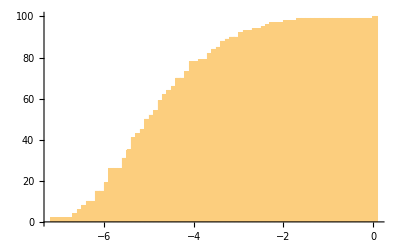

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0.5,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-8.17283,0)(-7.17283,1)(-7.17283,2)(-6.69591,3)(-6.66348,4)(-6.59064,5)(-6.59064,6)(-6.41864,7)(-6.41864,8)(-6.33007,9)(-6.33007,10)(-6.19812,11)(-6.19812,12)(-6.17446,13)(-6.16595,14)(-6.16595,15)(-5.92418,16)(-5.92418,17)(-5.91047,18)(-5.91047,19)(-5.89247,20)(-5.89247,21)(-5.87506,22)(-5.87506,23)(-5.83001,24)(-5.82901,25)(-5.82901,26)(-5.59573,27)(-5.52719,28)(-5.52719,29)(-5.51224,30)(-5.51224,31)(-5.49875,32)(-5.49875,33)(-5.4737,34)(-5.4737,35)(-5.37616,36)(-5.37616,37)(-5.32045,38)(-5.32045,39)(-5.31372,40)(-5.31372,41)(-5.22482,42)(-5.22482,43)(-5.12201,44)(-5.12201,45)(-5.08849,46)(-5.08849,47)(-5.07134,48)(-5.07134,49)(-5.01493,50)(-4.93044,51)(-4.93044,52)(-4.81556,53)(-4.81556,54)(-4.79857,55)(-4.79857,56)(-4.73751,57)(-4.70374,58)(-4.70374,59)(-4.69762,60)(-4.69762,61)(-4.6586,62)(-4.57896,63)(-4.57896,64)(-4.49129,65)(-4.49129,66)(-4.39186,67)(-4.39186,68)(-4.36977,69)(-4.36977,70)(-4.15184,71)(-4.15184,72)(-4.13337,73)(-4.09853,74)(-4.09853,75)(-4.0483,76)(-4.0483,77)(-4.01156,78)(-3.81061,79)(-3.68588,80)(-3.68588,81)(-3.6435,82)(-3.58457,83)(-3.58457,84)(-3.45313,85)(-3.38506,86)(-3.38506,87)(-3.31761,88)(-3.23851,89)(-3.17197,90)(-2.99576,91)(-2.90682,92)(-2.83739,93)(-2.64707,94)(-2.45225,95)(-2.34486,96)(-2.20275,97)(-1.97571,98)(-1.69769,99)(0.,100)(0.5,100)

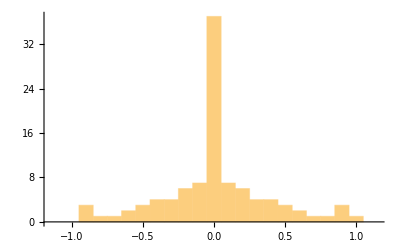

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.5,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.917762,1)(-0.900307,2)(-0.888369,3)(-0.798717,4)(-0.661734,5)(-0.642574,6)(-0.550099,7)(-0.541639,8)(-0.474952,9)(-0.471089,10)(-0.412725,11)(-0.410217,12)(-0.39061,13)(-0.35097,14)(-0.307707,15)(-0.30021,16)(-0.271304,17)(-0.255549,18)(-0.245384,19)(-0.202753,20)(-0.171531,21)(-0.167365,22)(-0.166178,23)(-0.151867,24)(-0.146569,25)(-0.095146,26)(-0.094568,27)(-0.0838394,28)(-0.0800946,29)(-0.0716011,30)(-0.0616444,31)(-0.0480478,32)(-0.0457819,33)(-0.0438435,34)(-0.03533,35)(-0.0336234,36)(-0.0328047,37)(0.,38)(0.,39)(0.,40)(0.,41)(0.,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.,54)(0.,55)(0.,56)(0.,57)(0.,58)(0.,59)(0.,60)(0.,61)(0.,62)(0.0328047,63)(0.0336234,64)(0.03533,65)(0.0438435,66)(0.0457819,67)(0.0480478,68)(0.0616444,69)(0.0716011,70)(0.0800946,71)(0.0838394,72)(0.094568,73)(0.095146,74)(0.146569,75)(0.151867,76)(0.166178,77)(0.167365,78)(0.171531,79)(0.202753,80)(0.245384,81)(0.255549,82)(0.271304,83)(0.30021,84)(0.307707,85)(0.35097,86)(0.39061,87)(0.410217,88)(0.412725,89)(0.471089,90)(0.474952,91)(0.541639,92)(0.550099,93)(0.642574,94)(0.661734,95)(0.798717,96)(0.888369,97)(0.900307,98)(0.917762,99)(1.,100)(1.5,100)

### Data for topic patterns

```mathematica
TopicClusters=DeleteCases[NonStopClusters,{_,_,_,"B",_,_,_,_}];
```

```mathematica
Length[TopicClusters]
```

398

```mathematica
SelectedClusters=TopicClusters;
```

```mathematica
TopicClustersKorean=TopicClusters;
```

```mathematica
Timing[PkoTopic=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{540.438,Null}

```mathematica
Timing[PkoT=Table[v=Table[prepP=PkoTopic_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,100}];v/Total[v],{m,1,100}];]
```

{0.0625,Null}

```mathematica
Timing[spec=Eigenvalues[PkoT];]
```

{1.20313,Null}

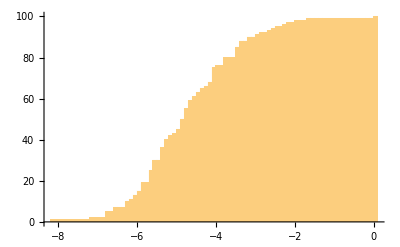

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0.5,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-9.14311,0)(-8.14311,1)(-7.14295,2)(-6.75463,3)(-6.73522,4)(-6.73522,5)(-6.56565,6)(-6.56565,7)(-6.26659,8)(-6.26536,9)(-6.26536,10)(-6.16184,11)(-6.0854,12)(-6.0854,13)(-5.98363,14)(-5.98363,15)(-5.89283,16)(-5.89283,17)(-5.84528,18)(-5.84528,19)(-5.69228,20)(-5.69228,21)(-5.69017,22)(-5.69017,23)(-5.62289,24)(-5.62289,25)(-5.59634,26)(-5.59634,27)(-5.5952,28)(-5.5952,29)(-5.58151,30)(-5.39042,31)(-5.39042,32)(-5.31766,33)(-5.31766,34)(-5.31313,35)(-5.31313,36)(-5.29371,37)(-5.29371,38)(-5.23685,39)(-5.23685,40)(-5.18802,41)(-5.18802,42)(-5.00526,43)(-4.9425,44)(-4.9425,45)(-4.84315,46)(-4.82773,47)(-4.82773,48)(-4.8153,49)(-4.8153,50)(-4.76598,51)(-4.76598,52)(-4.74505,53)(-4.74505,54)(-4.72729,55)(-4.69585,56)(-4.69585,57)(-4.6677,58)(-4.6677,59)(-4.55603,60)(-4.55603,61)(-4.49395,62)(-4.49395,63)(-4.35161,64)(-4.35161,65)(-4.25846,66)(-4.14037,67)(-4.14037,68)(-4.04897,69)(-4.04897,70)(-4.03754,71)(-4.03754,72)(-4.02594,73)(-4.02594,74)(-4.0092,75)(-3.94412,76)(-3.79881,77)(-3.74532,78)(-3.74532,79)(-3.70155,80)(-3.45033,81)(-3.43962,82)(-3.43962,83)(-3.43956,84)(-3.43956,85)(-3.31377,86)(-3.3051,87)(-3.3051,88)(-3.15903,89)(-3.10783,90)(-2.90769,91)(-2.81003,92)(-2.66338,93)(-2.53841,94)(-2.40581,95)(-2.27425,96)(-2.13859,97)(-1.90971,98)(-1.6483,99)(0.,100)(0.5,100)

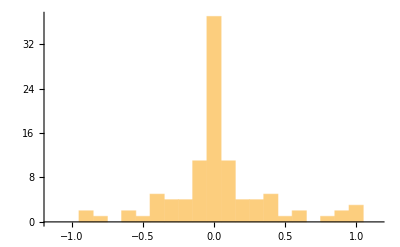

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.5,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.919926,1)(-0.85319,2)(-0.837207,3)(-0.618813,4)(-0.578855,5)(-0.503608,6)(-0.440167,7)(-0.40601,8)(-0.388626,9)(-0.357883,10)(-0.357277,11)(-0.319166,12)(-0.301536,13)(-0.29666,14)(-0.263483,15)(-0.21194,16)(-0.207358,17)(-0.175143,18)(-0.157046,19)(-0.132122,20)(-0.120796,21)(-0.119718,22)(-0.118917,23)(-0.0963252,24)(-0.0954532,25)(-0.0912703,26)(-0.0722327,27)(-0.071615,28)(-0.0641477,29)(-0.0556045,30)(-0.0484538,31)(-0.0386876,32)(-0.0347846,33)(-0.0346018,34)(-0.0262937,35)(-0.0207491,36)(0.,37)(0.,38)(0.,39)(0.,40)(0.,41)(0.,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.,54)(0.,55)(0.,56)(0.,57)(0.,58)(0.,59)(0.,60)(0.,61)(0.0207491,62)(0.0262937,63)(0.0346018,64)(0.0347846,65)(0.0386876,66)(0.0484538,67)(0.0556045,68)(0.0641477,69)(0.071615,70)(0.0722327,71)(0.0912703,72)(0.0954532,73)(0.0963252,74)(0.118917,75)(0.119718,76)(0.120796,77)(0.132122,78)(0.157046,79)(0.175143,80)(0.207358,81)(0.21194,82)(0.263483,83)(0.29666,84)(0.301536,85)(0.319166,86)(0.357277,87)(0.357883,88)(0.388626,89)(0.40601,90)(0.440167,91)(0.503608,92)(0.578855,93)(0.618813,94)(0.837207,95)(0.85319,96)(0.919926,97)(1.,98)(1.,99)(1.,100)(1.5,100)

### Preparations for Fig. S17

#### Bulk vectors

```mathematica
EnglishRef=TopicClustersEnglish;
```

```mathematica
KoreanRef=TopicClustersKorean;
```

```mathematica
PandPChapEnglish=StringSplit[ExampleData[{"Text","PrideAndPrejudice"}],"Chapter "~~DigitCharacter..~~" "];
```

```mathematica
Length[PandPChapEnglish]
```

61

```mathematica
VecEnglish=Table[{EnglishRef_⟦k,1⟧,StringCount[PandPChapEnglish,WordBoundary~~Alternatives@@(#_⟦1⟧&/@EnglishRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[EnglishRef]}];
```

```mathematica
PandPChapKorean=StringReplace[ImportString[#,"HTML"]&/@StringReplace[StringReplace[StringReplace[StringSplit[StringReplace[KoreanRebracketing[Import["Pride and Prejudice (Korean).txt"]],{"〈","〉","「","」","─","○"}:>" "],"제"~~DigitCharacter..~~"장"~~("("~~"제"~~DigitCharacter..~~"권"~~" "..~~"제"~~DigitCharacter..~~"장"~~")")...~~"\n"...],{"\n":>"\n舜"}],{(s:("舜"~~Repeated[Except["\n"],{1,80}]))~~"\n":>s<>"垚"}],{"舜":>""}],{"垚":>"\n\n"}];
```

```mathematica
Length[PandPChapKorean]
```

61

```mathematica
VecKorean=Table[{KoreanRef_⟦k,1⟧,StringCount[PandPChapKorean,WordBoundary~~Alternatives@@(#_⟦1⟧&/@KoreanRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[KoreanRef]}];
```

```mathematica
FlatScreenedPairs=Flatten[Table[{#_⟦1⟧,#_⟦2,k⟧},{k,1,Length[#_⟦2⟧]}]&/@Select[Table[{EnglishRef[[k,1]],#_⟦1⟧&/@Select[VecKorean,JaccardRuzickaSim[#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧]≥Max[1-7/100 √61,1-√(Length[Select[Min[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}],#>0&]]/Total[Max[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}]])]&]},{k,1,Length[EnglishRef]}],Length[#_⟦2⟧]>0&],1];
```

```mathematica
SiftedTags=Union[(#_⟦1⟧&/@FlatScreenedPairs)];SiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SiftedTags=Union[(#_⟦2⟧&/@FlatScreenedPairs)];SiftedKoreanRef=Reverse[SortBy[Table[Cases[KoreanRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
Length[SiftedEnglishRef]
```

87

```mathematica
Length[SiftedKoreanRef]
```

88

#### Spectral parameters for English

```mathematica
FromTopics=SiftedEnglishRef;
```

```mathematica
FromDelta=ReadDelta[#]&/@FromTopics;
```

```mathematica
FromN=(#_⟦3⟧-1)&/@FromTopics;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersEnglish,PenTopic,#_⟦1⟧&/@FromTopics];]
```

{50.3972,Null}

```mathematica
FromKinQ=KinQ;
```

```mathematica
FromEta=SemanticComplexities;
```

#### Spectral parameters for Korean

```mathematica
ToTopicsKorean=SiftedKoreanRef;
```

```mathematica
Length[ToTopicsKorean]
```

88

```mathematica
ToDeltaKorean=ReadDelta[#]&/@ToTopicsKorean;
```

```mathematica
ToNKorean=(#_⟦3⟧-1)&/@ToTopicsKorean;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersKorean,PkoTopic,#_⟦1⟧&/@ToTopicsKorean];]
```

{339.277,Null}

```mathematica
ToKinKorean=KinQ;
```

```mathematica
ToEtaKorean=SemanticComplexities;
```

#### Translation

```mathematica
AbsoluteTiming[fromLabeled=Transpose[{#_⟦1⟧&/@FromTopics,FromKinQ}];toLabeled=Transpose[{#_⟦1⟧&/@ToTopicsKorean,ToKinKorean}];Report=Table[{FlatScreenedPairs_⟦k⟧,(JaccardRuzickaSim[Cases[fromLabeled,{FlatScreenedPairs_⟦k,1⟧,_}]_⟦1,2⟧,Cases[toLabeled,{FlatScreenedPairs_⟦k,2⟧,_}]_⟦1,2⟧])},{k,1,Length[FlatScreenedPairs]}];]
```

{0.0355017,Null}

```mathematica
prep=Union[Select[Table[{Report_⟦n,1,1⟧,Report_⟦n,1,2⟧,Report_⟦n,2⟧},{n,1,Length[Report]}],#_⟦3⟧≥0.7&]];g=Graph[(#_⟦1⟧->#_⟦2⟧)&/@prep,EdgeWeight->(#_⟦3⟧&/@prep)];(KuhnSln={#,FindRowRank[#,prep],FindColRank[#,prep]}&/@Select[{#,PropertyValue[{g,#},EdgeWeight]}&/@FindIndependentEdgeSet[g],#_⟦2⟧>0&])//TableForm
```

{{Brighton,24}}->{{브라이튼,2},{브라이튼과,1},{브라이튼에,8},{브라이튼을,4},{브라이튼의,1},{브라이튼에서,4},{브라이튼으로,5},{브라이튼이라니,1}}
0.81953574608375 | 1 | 1
{{de,39}}->{{버그,45}}
0.73525769239269 | 1 | 1
{{Derbyshire,24}}->{{더비셔,5},{더비셔가,1},{더비셔로,1},{더비셔를,3},{더비셔만,1},{더비셔에,8},{더비셔의,1},{더비셔보다,2},{더비셔에서,6},{더비셔에서는,2}}
0.80065295058742 | 1 | 1
{{library,23}}->{{서재가,1},{서재는,1},{서재로,9},{서재를,3},{서재에,6},{서재까지,1},{서재에서,3},{서재에서만은,1},{서재에서만큼은,1}}
0.73127630268641 | 1 | 1
{{Mrs,343}}->{{부인,37},{부인과,40},{부인께,1},{부인도,12},{부인뿐,1},{부인에,1},{부인은,157},{부인을,12},{부인의,38},{부인이,115},{부인께서,2},{부인보다,4},{부인에게,29},{부인이나,3},{부인이야,1},{부인인가,1},{부인한테,2},{부인에게는,5},{부인에게서,4},{부인이라니,1},{부인이었다,1},{부인으로서는,1}}
0.79406492684911 | 1 | 1
{{Netherfield,73}}->{{네더필드,11},{네더필드가,1},{네더필드로,7},{네더필드를,8},{네더필드만,1},{네더필드에,18},{네더필드와,2},{네더필드의,9},{네더필드까지,1},{네더필드에서,18},{네더필드에선,1}}
0.71072595764721 | 1 | 1
{{oh,95}}->{{아,102}}
0.73766042094839 | 1 | 1
{{Pemberley,53}}->{{펨벌리,9},{펨벌리가,3},{펨벌리는,2},{펨벌리로,6},{펨벌리를,7},{펨벌리에,14},{펨벌리와,2},{펨벌리의,12},{펨벌리에서,6}}
0.70216916589484 | 1 | 1
{{Rosings,49}}->{{로징스,10},{로징스가,1},{로징스는,1},{로징스로,3},{로징스를,2},{로징스뿐,1},{로징스에,12},{로징스와,1},{로징스의,14},{로징스에서,15},{로징스와는,1},{로징스와의,1},{로징스에서는,1}}
0.80046062600442 | 1 | 1
{{sir,78}}->{{경,6},{경과,2},{경도,3},{경은,14},{경을,2},{경의,7},{경이,18},{경에게,2},{경의를,2},{경한테,1}}
0.74511804898092 | 2 | 2
{{William,40},{William's,6}}->{{윌리엄,47}}
0.80659728671007 | 1 | 1
{{thousand,34}}->{{파운드,5},{파운드가,4},{파운드나,7},{파운드를,7},{파운드씩,1},{파운드야,1},{파운드에,1},{파운드의,4},{파운드라는,1},{파운드라니,1},{파운드에서,1},{파운드짜리,1},{파운드라고요,1}}
0.73965982837245 | 1 | 1
{{ball,34},{balls,8}}->{{무도회,9},{무도회가,11},{무도회는,3},{무도회도,1},{무도회로,1},{무도회를,9},{무도회에,13},{무도회와,1},{무도회라고,1},{무도회보다,1},{무도회에서,12},{무도회에선,1},{무도회장에,1},{무도회였고요,1},{무도회장에서,1},{무도회만으로도,1},{무도회였으니까,1},{무도회장에서는,1},{무도회에서였습니다,1}}
0.79810980006895 | 1 | 1
{{Catherine,110},{Catherine's,16}}->{{캐서린,123},{캐서린과,8},{캐서린은,2},{캐서린을,1}}
0.70417869751076 | 1 | 1
{{Charlotte,68},{Charlotte's,17}}->{{샬럿,20},{샬럿과,7},{샬럿네,1},{샬럿에,1},{샬럿은,15},{샬럿을,7},{샬럿의,14},{샬럿이,34},{샬럿에게,5},{샬럿한테,1},{샬럿네처럼,1},{샬럿에게는,1}}
0.82493128958696 | 1 | 1
{{Darcy,374},{Darcy's,44}}->{{다시,361},{다시가,40},{다시나,1},{다시는,56},{다시도,2},{다시로,1},{다시를,13},{다시에,2},{다시와,6},{다시의,15},{다시라는,1},{다시보다,1},{다시에게,7},{다시와는,1},{다시에게는,1}}
0.80991097143482 | 1 | 1
{{door,32},{doors,8}}->{{문,8},{문에,1},{문을,12},{문이,6},{문까지,1},{문께에,1},{문들을,1},{문으로,1},{문의해,3},{문고에서,1}}
0.70944093640767 | 1 | 1
{{elegance,9},{elegant,14}}->{{우아한,14},{우아함,1},{우아하게,1},{우아하고,2},{우아함과,1},{우아함은,1},{우아했고,1},{우아했다,1},{우아함으로,1},{우아했으며,1}}
0.70344362385931 | 1 | 1
{{father,116},{father's,19}}->{{부친,1},{아빠,2},{부친과,2},{부친도,2},{부친에,4},{부친은,6},{부친을,1},{부친의,10},{부친이,7},{부친인,1},{아버지,12},{아빠가,2},{부친과의,1},{부친께서,1},{부친에게,1},{아버지가,50},{아버지께,2},{아버지나,2},{아버지는,25},{아버지도,2},{아버지를,9},{아버지만,1},{아버지에,2},{아버지와,7},{아버지의,17},{부친에게는,1},{부친에게서,1},{아버지께서,1},{아버지에게,10},{아버지와의,1},{아버지처럼,1},{아버지하고,1},{아버지한테,1},{부친에게서도,1},{아버지들처럼,1},{아버지보다는,1},{아버지에게서,2}}
0.75742174448806 | 1 | 1
{{Fitzwilliam,32},{Fitzwilliam's,5}}->{{피츠윌리엄,33},{피츠윌리엄과,2},{피츠윌리엄은,1},{피츠윌리엄이,2},{피츠윌리엄에게서,1}}
0.82328829112334 | 1 | 1
{{Jane,263},{Jane's,28}}->{{제인,36},{제인과,27},{제인도,9},{제인만,1},{제인아,4},{제인에,8},{제인은,97},{제인을,34},{제인의,27},{제인이,109},{제인더러,1},{제인만큼,1},{제인보다,3},{제인에게,26},{제인에겐,1},{제인에서,1},{제인이나,3},{제인조차,1},{제인처럼,1},{제인한테,1},{제인만큼은,1},{제인보다도,1},{제인에게는,4},{제인에게도,1},{제인에게로,1},{제인에게서,5},{제인이라면,1},{제인조차도,1},{제인하고만,1},{제인한테도,1},{제인만큼이나,1},{제인뿐이었어요,1}}
0.7366087078756 | 1 | 1
{{Kitty,69},{Kitty's,2}}->{{키티,3},{키티가,21},{키티는,20},{키티도,1},{키티를,2},{키티야,6},{키티와,18},{키티의,3},{키티에게,4},{키티에게는,2},{키티뿐이었지만,1}}
0.70788321106417 | 1 | 1
{{Lizzy,95},{Lizzy's,2}}->{{리지,22},{리지가,6},{리지는,5},{리지를,3},{리지야,57},{리지와,2},{리지까지,1},{리지에게,3}}
0.80092722483228 | 1 | 1
{{Mary,38},{Mary's,1}}->{{메리,6},{메리가,11},{메리나,1},{메리는,15},{메리도,1},{메리를,1},{메리만,1},{메리와,4},{메리의,4},{메리라면,1},{메리만이,1},{메리보다,1},{메리에게는,1},{메리조차도,1}}
0.71422113375246 | 1 | 1
{{serious,24},{seriously,13}}->{{진지한,13},{진지해,2},{진지하게,18},{진지하고,3},{진지하지,1},{진지해져,1},{진지하다는,1},{진지했다는,1},{진지해졌으면,1},{진지해지라는,1}}
0.78366838276294 | 1 | 1
{{Wickham,162},{Wickham's,32}}->{{위컴,91},{위컴과,13},{위컴도,3},{위컴에,10},{위컴은,22},{위컴을,23},{위컴의,32},{위컴이,49},{위컴하,1},{위컴만큼,1},{위컴보다,2},{위컴에게,3},{위컴으로,1},{위컴이고,1},{위컴이랑,1},{위컴처럼,1},{위컴하고,2},{위컴보다도,1},{위컴에게도,2},{위컴에게서,2},{위컴이라고,2},{위컴이라는,1},{위컴조차도,1},{위컴하고는,1}}
0.73627295281178 | 1 | 1
{{Bennet,294},{Bennet's,29},{Bennets,10}}->{{베넷,412},{베넷은,1},{베넷을,1},{베넷의,1},{베넷이,1},{베넷이라는,2},{베넷으로부터,1}}
0.76225636546158 | 1 | 1
{{cousin,41},{cousin's,8},{cousins,11}}->{{사촌,12},{사촌과,3},{사촌도,1},{사촌들,1},{사촌에,2},{사촌은,6},{사촌을,2},{사촌의,5},{사촌이,8},{사촌인,2},{사촌들과,1},{사촌들은,1},{사촌들을,1},{사촌들이,4},{사촌에게,6},{사촌들에게,2},{사촌에게서,2},{사촌이었고,1},{사촌이여,2}}
0.82717485417918 | 1 | 1
{{eye,15},{eyeing,1},{eyes,52}}->{{미소,9},{미소가,5},{미소나,1},{미소로,2},{미소를,43},{미소만,3},{미소와,1}}
0.85221516998493 | 1 | 1
{{Forster,38},{Forster's,1},{Forsters,1}}->{{포스터,46}}
0.77152409558859 | 1 | 1
{{Gardiner,84},{Gardiner's,13},{Gardiners,6}}->{{가디너,112},{가디너가,1}}
0.73211916435951 | 1 | 1
{{husband,42},{husband's,8},{husbands,4}}->{{남편,6},{남편감,1},{남편과,4},{남편도,1},{남편은,3},{남편을,5},{남편의,5},{남편이,17},{남편감을,5},{남편에게,7},{남편으로,1},{남편이든,1},{남편으로서,2},{남편이라면,1},{남편만큼이나,1}}
0.73714383375596 | 1 | 1
{{maternal,2},{mother,110},{mother's,25}}->{{엄마,8},{모친과,1},{모친은,1},{어머니,19},{엄마도,1},{엄마와,2},{어머니가,52},{어머니나,2},{어머니는,30},{어머니도,2},{어머니를,7},{어머니뿐,1},{어머니에,1},{어머니와,13},{어머니의,22},{어머니인,1},{어머니께서,1},{어머니로서,1},{어머니만이,1},{어머니만큼,1},{어머니에게,18},{어머니이신,1},{어머니께서는,1},{어머니에게는,2},{어머니만큼이나,1}}
0.77694272779482 | 1 | 1
{{Phillip's,1},{Phillips,26},{Phillips's,5}}->{{필립스,47}}
0.76895420126988 | 1 | 1
{{uncle,59},{uncle's,9},{uncles,3}}->{{숙부,3},{숙부가,23},{숙부께,1},{숙부나,1},{숙부는,6},{숙부님,1},{숙부도,2},{숙부를,2},{숙부와,28},{숙부의,7},{숙부인,1},{숙부가요,1},{숙부께서,4},{숙부께선,2},{숙부님도,1},{숙부에게,3},{숙부한테,1},{숙부에게서,1},{숙부한테서,1}}
0.77247824293516 | 1 | 1
{{wife,44},{wife's,3},{wives,1}}->{{아내가,14},{아내는,4},{아내도,1},{아내를,7},{아내에,1},{아내와,1},{아내의,4},{아내인,2},{아내감을,1},{아내에게,4},{아내보다는,1},{아내에게는,1},{아내에게서,1},{아내만큼이나,1}}
0.82282085167486 | 1 | 1
{{young,130},{younger,30},{youngest,13}}->{{젊고,3},{젊은,63},{젊다는,1},{젊었을,1},{젊음과,1},{젊음의,1},{젊은이가,10},{젊은이는,1},{젊은이다,1},{젊은이도,1},{젊은이라,1},{젊은이로,1},{젊은이를,2},{젊은이뿐,1},{젊은이야,1},{젊은이와,2},{젊은이의,2},{젊은이들과,1},{젊은이들도,1},{젊은이들은,2},{젊은이들을,1},{젊은이들이,1},{젊은이라는,2},{젊은이에게,1},{젊은이였다,1},{젊은이처럼,1},{젊은이들과는,1},{젊은이들보다,1},{젊은이들처럼,1},{젊은이들에게는,1},{젊은이들이라면,1}}
0.70968518185667 | 1 | 1
{{arrive,2},{arrived,15},{arriving,1},{arrival,30}}->{{도착을,1},{도착한,11},{도착할,5},{도착해,1},{도착하게,1},{도착하기,1},{도착하는,3},{도착하니,1},{도착하면,1},{도착하여,2},{도착하자,2},{도착해서,2},{도착했고,1},{도착했다,10},{도착했어,1},{도착했을,4},{도착하기로,1},{도착하는지,1},{도착하려면,1},{도착했는데,4},{도착했다고,1},{도착했다는,3},{도착했음을,1},{도착하기만을,1},{도착하자마자,6},{도착했으면서도,1}}
0.7489716147784 | 1 | 1
{{best,41},{better,92},{good,184},{good-humoured,6}}->{{좋,5},{나아,1},{나은,10},{나을,9},{낫고,1},{낫군,1},{낫긴,1},{낫네,1},{낫다,1},{낫지,2},{좋게,30},{좋고,3},{좋다,7},{좋던,1},{좋아,14},{좋은,89},{좋을,8},{좋지,16},{나아가,1},{나아서,1},{나아진,1},{나아질,4},{나았다,1},{나았던,1},{나았을,1},{나으니,1},{낫겠다,2},{낫겠어,1},{낫기를,1},{낫다고,3},{좋게도,4},{좋겠군,1},{좋겠네,1},{좋겠다,7},{좋겠소,1},{좋겠어,15},{좋겠죠,1},{좋겠지,1},{좋구나,3},{좋기는,1},{좋기를,2},{좋다고,4},{좋다는,4},{좋다며,1},{좋다면,1},{좋던데,1},{좋아요,3},{좋았다,6},{좋았던,1},{좋았어,2},{좋았을,7},{좋았지,1},{좋으냐,1},{좋으면,3},{좋은가,2},{좋은지,3},{좋을까,2},{좋을지,3},{최선을,4},{최선의,5},{나아가기,2},{나아갔다,1},{나아졌다,2},{나아졌어,1},{나아지고,1},{나아지실,1},{나아지지,2},{나았다고,1},{나았을걸,1},{나을걸요,1},{낫겠네요,1},{낫겠다고,2},{낫겠다는,2},{낫겠어요,1},{낫다고는,1},{낫습니다,1},{좋겠구나,3},{좋겠군요,2},{좋겠는데,1},{좋겠다고,2},{좋겠다는,3},{좋겠어요,4},{좋겠으며,1},{좋겠지만,1},{좋다든지,1},{좋습니다,1},{좋았으면,1},{좋았을걸,2},{좋았지만,2},{좋으련만,1},{좋은가요,1},{좋을까요,1},{나아졌다는,2},{나아졌지만,1},{나아지지를,1},{나아진다고,1},{낫겠습니다,1},{좋겠냐고요,1},{좋겠습니다,1},{좋았겠지만,1},{좋으시군요,1},{좋으시다는,1},{최선이라고,1},{나아지던데요,1}}
0.769845480311 | 1 | 1
{{Bingley,257},{Bingley's,49},{Bingleys,4},{Bingleys',1}}->{{빙리,257},{빙리가,49},{빙리나,2},{빙리는,26},{빙리도,2},{빙리로,1},{빙리를,9},{빙리에,6},{빙리와,13},{빙리의,18},{빙리라고,1},{빙리만큼,1},{빙리보다,1},{빙리에게,11},{빙리예요,1},{빙리처럼,1},{빙리한테,1},{빙리로부터,1},{빙리에게는,1},{빙리에게서,1},{빙리조차도,1},{빙리일,1},{빙리일지도,1}}
0.82864556583004 | 1 | 1
{{came,90},{come,93},{comes,16},{coming,61}}->{{올,25},{와,11},{오게,7},{오고,4},{오기,4},{오는,25},{오니,1},{오면,3},{오신,2},{오실,2},{오지,13},{온다,1},{와도,2},{와라,1},{와서,22},{와야,1},{오기도,1},{오기로,5},{오는데,1},{오는지,2},{오더니,1},{오도록,1},{오라고,6},{오라는,3},{오셔서,1},{오셔야,1},{오셨기,1},{오셨던,1},{오시면,1},{오지는,3},{옵니다,1},{와서는,1},{와서야,1},{와야만,1},{와중에,2},{오겠다고,3},{오겠다는,1},{오겠다면,1},{오기에는,1},{오는구나,1},{오는데요,1},{오셨는지,1},{오셨으니,1},{오시다니,2},{오십니다,1},{오자마자,3},{와야겠다고,1},{왔고,2},{왔기,1},{왔다,17},{왔던,8},{왔어,5},{왔을,11},{왔는데,1},{왔는지,1},{왔다고,4},{왔다는,10},{왔단다,1},{왔어야,1},{왔어요,2},{왔었지,1},{왔을까,2},{왔지만,1},{왔지요,1},{왔는데요,1},{왔다면서,1},{왔습니다,3},{왔었는데,1},{왔었다는,3},{왔었다니,1},{왔으니까요,1},{왔었다니까요,1}}
0.76401243869395 | 1 | 1
{{daily,3},{day,130},{day's,4},{days,30}}->{{시간,29},{시간과,1},{시간도,2},{시간만,2},{시간씩,1},{시간에,12},{시간은,9},{시간을,56},{시간의,1},{시간이,33},{시간까지,1},{시간들을,1},{시간보다,1},{시간에는,2},{시간에도,1},{시간에야,1},{시간이나,1},{시간까지는,1},{시간이라는,1},{시간이었다,1}}
0.72627996283816 | 1 | 1
{{dance,31},{danced,12},{dances,10},{dancing,21}}->{{춤,4},{춤과,1},{춤도,1},{춤에,3},{춤은,5},{춤을,39},{춤이,4},{춤추,2},{춤출,4},{춤이란,1},{춤추는,9},{춤추던,1},{춤추지,2},{춤추기로,1},{춤추자고,1},{춤췄는지는,1}}
0.8080332830277 | 1 | 1
{{daughter,78},{daughter's,7},{daughters,49},{daughters',1}}->{{딸,22},{따님,5},{딸과,7},{딸들,3},{딸려,2},{딸만,1},{딸아,2},{딸에,1},{딸은,6},{딸을,20},{딸의,4},{딸이,19},{딸인,1},{따님과,1},{따님은,3},{따님을,4},{따님의,8},{따님이,1},{따님인,2},{딸들과,2},{딸들에,2},{딸들은,18},{딸들을,9},{딸들의,5},{딸들이,12},{딸보다,1},{딸에게,7},{딸이야,1},{맏딸을,2},{맏딸의,1},{맏딸이,2},{맏딸인,2},{따님들께,1},{따님들이,1},{따님에게,2},{따님이든,1},{딸들과의,1},{딸들만이,1},{딸들보다,2},{딸들에게,5},{딸들하고,1},{딸아이의,2},{딸이었다,3},{딸입니다,2},{맏딸에게,1},{따님들에게,1},{딸들에게는,1},{딸들에게서,1},{딸아이에게,1},{딸자식들을,1},{딸아이들에게,1},{따님이지요,1},{딸린,1}}
0.72586088812925 | 1 | 1
{{introduce,11},{introduced,9},{introducing,4},{introduction,11}}->{{소개가,4},{소개도,1},{소개될,1},{소개를,7},{소개하,2},{소개한,1},{소개할,1},{소개해,8},{소개되는,1},{소개라는,1},{소개받고,2},{소개받는,1},{소개받은,1},{소개하긴,1},{소개하는,1},{소개해도,3},{소개했고,1},{소개되든지,1},{소개하기에,1},{소개하려고,1},{소개하려는,1},{소개되었을지도,1}}
0.8105471512638 | 1 | 1
{{Lucas,65},{Lucas's,5},{Lucases,13},{Lucases',1}}->{{루커스,80},{루커스가,5},{루커스네,2},{루커스는,1},{루커스와,2},{루커스라도,1},{루커스에게,1}}
0.72644015598985 | 1 | 1
{{vanish,1},{vanished,2},{vain,20},{vanity,18}}->{{허영심,6},{허영심과,2},{허영심에,2},{허영심은,2},{허영심을,6},{허영심이,3}}
0.72344140787616 | 1 | 1
{{congratulate,7},{congratulated,2},{congratulation,1},{congratulations,12},{congratulatory,1}}->{{축하,2},{축하를,4},{축하의,5},{축하해,5},{축하하고,1},{축하하기,1},{축하하는,2},{축하한다,1},{축하하도록,1},{축하한다고,3},{축하해야겠다,1},{축하해야겠구나,1}}
0.81585203784807 | 1 | 1
{{disappoint,2},{disappointed,12},{disappointing,3},{disappointment,17},{disappointments,1}}->{{실망과,1},{실망에,2},{실망을,4},{실망이,2},{실망하,1},{실망시켜,1},{실망시킬,2},{실망으로,3},{실망하게,1},{실망하고,2},{실망하긴,1},{실망하는,1},{실망하지,2},{실망했다,3},{실망스러운,2},{실망했다는,1},{실망했을까,1},{실망스러웠다,1},{실망했더라도,1},{실망했었지요,1},{실망스럽더라도,1}}
0.70271630161945 | 1 | 1
{{happily,5},{happiness,72},{happy,83},{happier,3},{happiest,10}}->{{행복,4},{행복과,1},{행복도,2},{행복만,1},{행복에,10},{행복은,3},{행복을,28},{행복의,3},{행복이,8},{행복한,29},{행복할,14},{행복해,3},{행복감을,3},{행복보다,1},{행복이나,1},{행복하게,11},{행복하고,2},{행복하길,1},{행복하다,3},{행복하지,3},{행복한지,1},{행복할까,1},{행복해도,1},{행복해서,1},{행복해야,1},{행복해요,2},{행복해진,1},{행복해질,3},{행복해할,1},{행복했다,1},{행복했어,1},{행복했을,1},{행복보다는,1},{행복으로도,1},{행복하기를,7},{행복하기만,1},{행복하다고,3},{행복하다는,1},{행복합니다,1},{행복해지는,2},{행복해하고,1},{행복해하는,1},{행복했을까,1},{행복하겠구나,1},{행복해하는지,1},{행복하겠노라고,1}}
0.80744880907038 | 1 | 1
{{invite,6},{invited,11},{inviting,3},{invitation,34},{invitations,1}}->{{초대,3},{초대가,4},{초대는,2},{초대도,1},{초대로,1},{초대를,14},{초대에,6},{초대하,2},{초대할,1},{초대해,1},{초대되어,1},{초대받은,2},{초대받을,1},{초대장만,1},{초대장을,3},{초대장이,1},{초대하는,2},{초대하실,1},{초대하지,2},{초대해야,2},{초대되었다,1},{초대장에서,1},{초대하기는,1},{초대하도록,1},{초대하라고,1},{초대하시는,1},{초대하지도,1},{초대했다는,1},{초대했어도,1},{초대받았다고,1},{초대하기까지,1},{초대해야겠다는,2}}
0.75012464300137 | 1 | 1
{{miss,283},{missed,3},{missing,1},{missent,2},{missish,1}}->{{양,48},{양과,9},{양에,5},{양은,73},{양을,23},{양의,25},{양이,82},{양일,1},{양쪽,12},{양가의,1},{양과의,3},{양들이,1},{양보를,1},{양보할,1},{양에게,22},{양으로,1},{양이고,1},{양쪽에,3},{양쪽을,1},{양쪽의,1},{양처럼,1},{양하고,1},{양한테,1},{양들에게,1},{양만큼은,1},{양보하자,1},{양보하지,1},{양에게는,1},{양에게도,1},{양에게로,2},{양에게서,2},{양입니다,1},{양하고는,1},{양이라고요,1}}
0.71542132196672 | 1 | 1
{{pretty,24},{prettyish,1},{prettier,1},{prettier-coloured,1},{prettiest,1}}->{{예뻐,1},{예쁜,12},{예쁘게,2},{예쁘고,1},{예쁘군,1},{예쁘길,1},{예쁘지,2},{예쁘진,1},{예쁜지,1},{예뻐하는,1},{예쁘네요,1},{예쁘다고,2},{예쁘다는,3},{예쁘잖나,1},{예쁘장한,1},{예쁘지가,1},{예쁘지는,1},{예쁘지도,2},{예쁘지요,1},{예쁜가요,1},{예뻐했었지요,1},{예쁘장하다고,2},{예쁘장하다는,1}}
0.74977669963681 | 1 | 1
{{refuse,9},{refused,6},{refusing,7},{refusal,7},{refusals,1}}->{{거절로,1},{거절은,2},{거절을,4},{거절이,2},{거절한,1},{거절할,5},{거절해,2},{거절당한,1},{거절하고,3},{거절하는,6},{거절하러,1},{거절하면,1},{거절하지,3},{거절했고,1},{거절했다,1},{거절했던,2},{거절당했다,1},{거절하려고,1},{거절하면서,1},{거절한다는,1},{거절했다고,2},{거절하기까지,1},{거절함으로써,1}}
0.74734207685064 | 1 | 1
{{serve,2},{serving,1},{servant,15},{servant's,2},{servants,12}}->{{하인,2},{하인과,2},{하인도,1},{하인들,4},{하인에,1},{하인을,6},{하인의,3},{하인이,9},{하인들을,1},{하인들의,3},{하인들이,6},{하인에게,1},{하인들에게서,1}}
0.77763409885544 | 1 | 1
{{marriage,66},{married,61},{marry,42},{marrying,23},{matrimonial,1},{matrimony,6}}->{{결혼,32},{결혼과,1},{결혼도,2},{결혼에,16},{결혼은,9},{결혼을,64},{결혼의,5},{결혼이,17},{결혼하,4},{결혼한,11},{결혼할,22},{결혼만이,1},{결혼부터,1},{결혼시켜,2},{결혼시킬,1},{결혼에도,1},{결혼에서,2},{결혼으로,4},{결혼이야,1},{결혼하게,6},{결혼하고,1},{결혼하기,1},{결혼하는,8},{결혼하려,1},{결혼하면,1},{결혼하지,11},{결혼한다,2},{결혼해서,4},{결혼해야,1},{결혼했기,1},{결혼했어,1},{결혼했을,1},{결혼시켜서,1},{결혼시키게,2},{결혼시키는,4},{결혼이라는,2},{결혼하기도,1},{결혼하기를,6},{결혼하도록,3},{결혼하려고,1},{결혼하세요,1},{결혼하지나,1},{결혼한다고,1},{결혼한다는,1},{결혼해서는,1},{결혼했다는,3},{결혼했으면,2},{결혼했지요,1},{결혼하겠다고,3},{결혼함으로써,1},{결혼하라고까지,1}}
0.74265914876953 | 1 | 1
{{neighbour,8},{neighbouring,2},{neighbours,10},{neighbours',1},{neighbourhood,29},{neighbourhoods,1}}->{{이웃,15},{이웃에,4},{이웃은,1},{이웃을,1},{이웃의,1},{이웃이,2},{이웃인,1},{이웃들은,1},{이웃들을,3},{이웃들의,1},{이웃들이,1},{이웃으로,1},{이웃이란,1},{이웃들에게,2},{이웃에게도,1},{이웃이었다,1}}
0.76565518906466 | 1 | 1
{{office,6},{officer,8},{officers,29},{officers',2},{officiousness,1},{officious,3}}->{{장교,6},{장교가,1},{장교는,1},{장교도,1},{장교들,7},{장교로,2},{장교를,2},{장교와,3},{장교의,1},{장교들과,4},{장교들도,1},{장교들로,2},{장교들은,3},{장교들을,3},{장교들의,3},{장교들이,4},{장교복을,1},{장교직도,1},{장교직을,2},{장교들보다,1},{장교들에게,4},{장교들하고,1}}
0.72084166424065 | 1 | 1
{{visit,51},{visited,4},{visiting,5},{visits,5},{visitor,11},{visitors,14}}->{{방문,7},{방문에,4},{방문은,2},{방문을,10},{방문이,4},{방문하,1},{방문한,4},{방문할,8},{방문해,3},{방문객들,1},{방문객은,1},{방문객을,1},{방문객이,4},{방문에서,1},{방문으로,1},{방문하게,1},{방문하고,2},{방문하곤,1},{방문하기,1},{방문하는,7},{방문하라,1},{방문하러,8},{방문하실,1},{방문하여,7},{방문하지,1},{방문해서,1},{방문했다,4},{방문했던,2},{방문했을,2},{방문객들에,1},{방문객들을,1},{방문객들이,2},{방문하기도,1},{방문하기로,1},{방문하도록,2},{방문하라는,1},{방문해서는,1},{방문했다는,1},{방문했었다,1},{방문하겠다고,2},{방문하기까지,1},{방문하시다니,1}}
0.75281468855579 | 1 | 1

```mathematica
ResiftedTags=Union[(#_⟦1⟧&/@prep)];ResiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
ResiftedTags=Union[(#_⟦2⟧&/@prep)];ResiftedKoreanRef=Reverse[SortBy[Table[Cases[KoreanRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SemanticSim={Position[ResiftedEnglishRef,{#_⟦1⟧,___}]_⟦1,1⟧,Position[ResiftedKoreanRef,{#_⟦2⟧,___}]_⟦1,1⟧,#_⟦3⟧}&/@prep;
```

```mathematica
OptimalNodes={Position[ResiftedEnglishRef,{#_⟦1,1,1⟧,___}]_⟦1,1⟧,Position[ResiftedKoreanRef,{#_⟦1,1,2⟧,___}]_⟦1,1⟧,#_⟦2,1,1⟧,#_⟦3,1,1⟧}&/@KuhnSln;
```

```mathematica
Export["PnP_EnglishKorean.txt","%tournament\n"<>StringJoin[Riffle[Flatten["\\put("<>ToString[1.5+1+4#_⟦2⟧]<>","<>ToString[90-4#_⟦1⟧]<>"){\\color[rgb]"<>ToString[TempRGB[#_⟦3⟧]]<>"{\\rule{4pt}{4pt}}}"&/@SemanticSim],"\n"]]<>"\n%crosshairs\n"<>StringJoin[Riffle["\n%"<>ResiftedEnglishRef[[#_⟦1⟧,1,1,1]]<>"_"<>ResiftedKoreanRef[[#_⟦2⟧,1,1,1]]<>"
\\put("<>ToString[1.5+4#_⟦2⟧+3]<>","<>ToString[90-4#_⟦1⟧+2]<>"){\\color{green}\\linethickness{"<>ToString[1.5/#_⟦3⟧]<>"pt}\\line(-1,0){"<>ToString[4#_⟦2⟧-2]<>"}\\linethickness{"<>ToString[1.5/#_⟦4⟧]<>"pt}\\line(0,1){"<>ToString[4#_⟦1⟧-2]<>"}}"&/@OptimalNodes,"\n"]]];
```

#### English labels

```mathematica
FromClusters=ResiftedEnglishRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
EnglishCompress[w_]:=StringReplace[w,{"ai":>"𝔸","ea":>"𝕀","ou":>"𝕌","ee":>"𝔼","oo":>"𝕆"}]
```

```mathematica
EnglishDecompress[w_]:=StringReplace[w,{"𝔸":>"ai","𝕀":>"ea","𝕌":>"ou","𝔼":>"ee","𝕆":>"oo"}]
```

```mathematica
EvenOut[cl_]:=(prep=EnglishCompress[cl_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,cl_⟦2⟧}])
```

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,EnglishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["EnglishLabels_for_Korean_PnP.txt",StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5-3Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[91.75-1.5-4k]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[BCData_⟦m,n,2⟧==" ","","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]]];
```

#### Korean labels

```mathematica
FromClusters=ResiftedKoreanRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
ClusterCount={{"happiest","happiness","happy"},{10,72,83}}
```

{{happiest,happiness,happy},{10,72,83}}

```mathematica
EvenOut[cl_]:=(prep=KoreanCompress[cl_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[KoreanSort[{prep,cl_⟦2⟧}]])
```

```mathematica
EvenOut[ClusterCount]
```

{{happiest ,10},{happiness,72},{happy    ,83}}

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,KoreanDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
SplitEven[EvenOut[ClusterCount]]//Transpose//TableForm
```

1
h
10 | 2
a
10 | 3
p
10 | 4
p
10 | 5
i
10 | 6
e
10 | 7
s
10 | 8
t
10 | 9
 
10
1
h
72 | 2
a
72 | 3
p
72 | 4
p
72 | 5
i
72 | 6
n
72 | 7
e
72 | 8
s
72 | 9
s
72
1
h
83 | 2
a
83 | 3
p
83 | 4
p
83 | 5
y
83 | 6
 
83 | 7
 
83 | 8
 
83 | 9
 
83

```mathematica
Last[SplitEven[EvenOut[ClusterCount]]]
```

{{9, ,10},{9,s,72},{9, ,83}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];StemCount=Total[Last[#]&/@SortBy[prep,First]_⟦1,1⟧];kStem=First[StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]]&/@SortBy[prep,First]];kStemLength=StringLength[kStem];tStem=Replace[kStem,KoreanEtym];tStemLength=StringLength[tStem];prep=If[kStem==Replace[kStem,KoreanEtym],SortBy[prep,First],prep1=Join[Take[SortBy[prep,First],1],{#_⟦1⟧+2+tStemLength,#_⟦2⟧,#_⟦3⟧}&/@#&/@#&/@Drop[SortBy[prep,First],1]];Join[prep1,{{{{kStemLength+1,"(",StemCount}}},{{{kStemLength+2,tStem,StemCount}}},{{{kStemLength+2+tStemLength,")",StemCount}}}}]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
happ
165 |  | 
5
i
10 | 5
i
72 | 5
y
83
6
e
10 | 6
n
72 | 6
 
83
7
s
10 | 7
e
72 | 7
 
83
8
t
10 | 8
s
72 | 8
 
83
9
 
10 | 9
s
72 | 9
 
83

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
happ
165 |  | 
5
y
83 | 5
i
82 | 
6
 
83 | 6
n
72 | 6
e
10
7
 
83 | 7
e
72 | 7
s
10
8
 
83 | 8
s
72 | 8
t
10
9
 
83 | 9
s
72 | 9
 
10

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦6⟧]
```

{{{9}, ,83,0},{{9},s,72,83},{{9}, ,10,155}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["KoreanLabels_PnP.txt",StringReplace[StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5.25-.25+1+4k]<>","<>ToString[91]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*.9<0.15),"","\\BCR{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H*1,10^-3]]]<>"}{"<>(If[StringMatchQ[BCData_⟦m,n,2⟧,"("|")"],hpos=hpos-0.5;ToString[.5],ToString[hinc]])<>"}{"<>(ToString[N[Round[BCData_⟦m,n,3⟧/H*.9,10^-3]]])<>"}{\\kr{"<>StringReplace[BCData_⟦m,n,2⟧,{"♯":>"$\\sim$","♭":>"\\_"}]<>"}}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]],{"\\kr{$\\sim$}":>"$\\sim$","\\kr{\\_}":>"\\vphantom{1}\\_"}]];
```

```mathematica
Export["EnglishKorean_Report.txt",{Last[SortBy[#_⟦1,1,1⟧,Last]]_⟦1⟧,Last[SortBy[#_⟦1,1,2⟧,Last]]_⟦1⟧}&/@KuhnSln];
```

## Korean wrap

```mathematica
HanjaLookup=#_⟦2⟧&/@Union[{{"즉각","卽刻"},{"즉시","卽時"},{"전이","轉移"},{"약간","若干"},{"시작","始作"},{"부인","夫人"},{"베넷","BENNET"},{"빙리","BINGLEY"},{"위컴","WICKHAM"},{"결혼","結婚"},{"콜린스","COLLINS"},{"행복","幸福"},{"방문","訪問"},{"리지","LIZZY"},{"캐서린","CATHERINE"},{"가디너","GARDINER"},{"방","房"},{"엘리자베스","ELIZABETH"},{"다시","DARCY"},{"보고","報告"},{"제인","JANE"},{"편","便"},{"정말","正말"},{"리디아","LYDIA"},{"편지","便紙"},{"기분","氣分"},{"기대","期待"},{"사실","事實"},{"귀부인","貴婦人"},{"여성","女性"},{"대답","對答"},{"친구","親舊"},{"친","親"},{"관대","寬大"},{"관심","關心"},{"법","法"},{"시간","時間"},{"잠시","暫時"},{"확신","確信"},{"확실","確實"},{"문제","問題"},{"방해","妨害"},{"감정","感情"},{"행동","行動"},{"태도","態度"},{"가족","家族"},{"런던","LONDON"},{"애정","愛情"},{"마차","馬車"},{"암시","暗示"},{"성격","性格"},{"샬럿","CHARLOTTE"},{"계속","繼續"},{"이유","理由"},{"결과","結果"},{"결심","決心"},{"결함","缺陷"},{"대화","對話"},{"지금","只今"},{"소식","消息"},{"롱본","LONGBOURN"},{"반대","反對"},{"루커스","LUCAS"},{"식사","食事"},{"내용","內容"},{"숙부","叔父"},{"상황","狀況"},{"키티","KITTY"},{"우려","憂慮"},{"우아","優雅"},{"소개","紹介"},{"숙모","叔母"},{"네더필드","NETHERFIELD"},{"세상","世上"},{"설명","說明"},{"진심","眞心"},{"진실","眞實"},{"청혼","請婚"},{"의심","疑心"},{"신사","紳士"},{"대령","大領"},{"무시","無視"},{"무례","無禮"},{"무심","無心"},{"방문","訪問"},{"무도회","舞蹈會"},{"표정","表情"},{"미소","微笑"},{"계획","計劃"},{"로징스","ROSINGS"},{"메리턴","MERYTON"},{"재산","財産"},{"호기","好奇"},{"호감","好感"},{"경이","驚異"},{"펨벌리","PEMBERLEY"},{"사촌","四寸"},{"감사","感謝"},{"필요","必要"},{"칭찬","稱讚"},{"조심","操心"},{"초대","招待"},{"동의","同意"},{"동기","動機"},{"예의","禮儀"},{"장교","將校"},{"인사","人事"},{"약속","約束"},{"남편","男便"},{"메리","MARY"},{"친절","親切"},{"산책","散策"},{"부부","夫婦"},{"특","特"},{"특히","特히"},{"이모","姨母"},{"부대","部隊"},{"부분","部分"},{"문","門"},{"필립스","PHILIPS"},{"윌리엄","WILLIAM"},{"상당","相當"},{"상당히","相當히"},{"친척","親戚"},{"기억","記憶"},{"도착","到着"},{"포스터","FORSTER"},{"가능","可能"},{"버그","BOURGH"},{"책","冊"},{"저택","邸宅"},{"신분","身分"},{"동생","同生"},{"인물","人物"},{"충고","忠告"},{"충분","充分"},{"비난","非難"},{"순간","瞬間"},{"고려","考慮"},{"주인","主人"},{"하인","下人"},{"하트퍼드셔","HERTFORDSHIRE"},{"물론","勿論"},{"남성","男性"},{"연대","聯隊"},{"연습","練習"},{"질문","質問"},{"거리","距離"},{"침묵","沈默"},{"답장","答狀"},{"피츠윌리엄","FITZWILLIAM"},{"시선","視線"},{"완전","完全"},{"완전히","完全히"},{"부친","父親"},{"모친","母親"},{"희망","希望"},{"경우","境遇"},{"고통","苦痛"},{"기회","機會"},{"남자","男子"},{"노력","努力"},{"관계","關係"},{"찬사","讚辭"},{"허스트","HURST"},{"거절","拒絶"},{"오만","傲慢"},{"가문","家門"},{"실망","失望"},{"청","請"},{"파운드","POUND"},{"직접","直接"},{"표현","表現"},{"원","願"},{"분노","憤怒"},{"권리","權利"},{"소문","所聞"},{"신경","神經"},{"불행","不幸"},{"준비","準備"},{"전적","全的"},{"열심","熱心"},{"열심히","熱心히"},{"더비셔","DERBYSHIRE"},{"확실","確實"},{"확실히","確實히"},{"존경","尊敬"},{"분별력","分別力"},{"예전","예前"},{"현명","賢明"},{"여행","旅行"},{"중요","重要"},{"정중","鄭重"},{"평소","平素"},{"지방","地方"},{"장점","長點"},{"인정","認定"},{"하녀","下女"},{"마리아","MARIA"},{"사건","事件"},{"정원","庭園"},{"헌스퍼드","HUNSFORD"},{"목사관","牧師館"},{"목사","牧師"},{"가치","價値"},{"추측","推測"},{"상태","狀態"},{"쾌활","快活"},{"자부심","自負心"},{"서재","書齋"},{"브라이튼","BRIGHTON"},{"거실","居室"},{"피아노","PIANO"},{"특별","特別"},{"솔직","率直"},{"숙녀","淑女"},{"부족","不足"},{"연주","演奏"},{"용서","容恕"},{"의미","意味"},{"축하","祝賀"},{"비참","悲慘"},{"교구","敎區"},{"비밀","祕密"},{"영향","影響"},{"다정","多情"},{"도대체","都大體"},{"카드","CARD"},{"분명","分明"},{"분명히","分明히"},{"언급","言及"},{"군대","軍隊"},{"불안","不安"},{"허영심","虛榮心"},{"방법","方法"},{"교양","敎養"},{"결혼식","結婚式"},{"방식","方式"},{"목적","目的"},{"진정","鎭靜"},{"자식","子息"},{"의무","義務"},{"조지아나","GEORGIANA"},{"착각","錯覺"},{"변화","變化"},{"작별","作別"},{"의견","意見"},{"결정","決定"},{"최고","最高"},{"위안","慰安"},{"어조","語調"},{"경","卿"},{"양","孃"},{"굉장","宏壯"},{"명","名"},{"관련","關聯"},{"파악","把握"},{"영광","榮光"},{"여자","女子"},{"판단","判斷"},{"당연","當然"},{"기대","期待"},{"당황","唐惶"},{"차례","次例"},{"혐오","嫌惡"},{"불편","不便"},{"명예","名譽"},{"부탁","付託"},{"성공","成功"},{"충격","衝擊"},{"고백","告白"},{"경멸","輕蔑"},{"심각","深刻"},{"선택","選擇"},{"성품","性稟"},{"다행","多幸"},{"설득","說得"},{"만족","滿足"},{"편안","便安"},{"식으로","式으로"},{"자연","自然"},{"정신","精神"},{"이해","理解"},{"확인","確認"},{"심","甚"},{"점","點"},{"구","求"},{"향","向"},{"수치","羞恥"},{"진지","眞摯"},{"건강","健康"},{"일라이자","ELIZA"},{"변","變"},{"게임","GAME"},{"피","避"},{"분","分"},{"정확","正確"},{"상속","相續"},{"소중","所重"},{"이상","異常"},{"천","千"},{"대","對"},{"당장","當場"},{"강","强"},{"통","通"},{"침착","沈着"},{"번","番"},{"성직","聖職"},{"불쾌","不快"},{"모습","模襲"},{"자연스","自然스"}}]
```

{强,卿,求,對,名,門,房,番,法,變,分,甚,孃,願,點,冊,千,請,親,通,特,便,避,向,可能,家門,家族,價値,感謝,感情,距離,居室,拒絶,健康,GAME,結果,決心,決定,缺陷,結婚,輕蔑,境遇,驚異,繼續,計劃,考慮,告白,苦痛,關係,寬大,關聯,關心,宏壯,敎區,敎養,軍隊,權利,期待,氣分,記憶,機會,男性,男子,男便,內容,努力,DARCY,多情,多幸,答狀,當然,當場,唐惶,對答,大領,對話,到着,動機,同生,同意,LONDON,LONGBOURN,LIZZY,馬車,滿足,MARY,名譽,模襲,母親,牧師,目的,無禮,無視,無心,問題,勿論,微笑,反對,訪問,方法,方式,妨害,BOURGH,BENNET,變化,報告,部隊,夫婦,部分,夫人,不足,父親,付託,憤怒,分明,不安,不快,不便,不幸,非難,祕密,悲慘,BINGLEY,事件,事實,四寸,散策,相當,相續,狀態,狀況,CHARLOTTE,書齋,選擇,說得,說明,性格,成功,聖職,性稟,世上,紹介,所聞,消息,所重,率直,羞恥,淑女,叔母,叔父,瞬間,時間,視線,始作,食事,神經,身分,紳士,失望,深刻,暗示,愛情,若干,約束,語調,言及,女性,女子,旅行,聯隊,練習,演奏,熱心,榮光,影響,禮儀,예前,傲慢,完全,容恕,憂慮,優雅,慰安,WICKHAM,意見,義務,意味,疑心,姨母,異常,理由,理解,人物,人事,認定,子息,自然,作別,暫時,將校,長點,財産,邸宅,轉移,全的,正말,精神,庭園,鄭重,正確,JANE,操心,尊敬,主人,準備,重要,卽刻,卽時,只今,地方,直接,眞實,眞心,鎭靜,眞摯,質問,次例,錯覺,讚辭,請婚,招待,最高,推測,祝賀,衝擊,忠告,充分,親舊,親切,親戚,沈默,沈着,稱讚,CARD,快活,KITTY,態度,特別,特히,把握,判斷,便安,便紙,平素,表情,表現,必要,下女,下人,行動,幸福,賢明,嫌惡,好感,好奇,確信,確實,確認,希望,GARDINER,結婚式,貴婦人,DERBYSHIRE,都大體,ROSINGS,LUCAS,LYDIA,MARIA,MERYTON,牧師館,舞蹈會,分明히,分別力,相當히,式으로,熱心히,完全히,WILLIAM,自負心,自然스,CATHERINE,COLLINS,POUND,PEMBERLEY,FORSTER,PIANO,PHILIPS,HURST,虛榮心,確實히,NETHERFIELD,BRIGHTON,ELIZA,GEORGIANA,HUNSFORD,ELIZABETH,FITZWILLIAM,HERTFORDSHIRE}

```mathematica
KoreanWrap[file_]:=StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[Import[file],{"\\kr{"~~eng:(CharacterRange["A","Z"]|"("|")")..~~"}":>eng,"\\textcolor[rgb]{0.5,0.5,0.5}{":>"桀","\\textbf{":>"纣","\\end{picture}":>"炀"}],"\\kr{"~~hj:HanjaLookup~~"}":>"\\HJB{"~~hj~~"}"],"히}}":>"}\\kr{히}}"],{"桀"~~(c1:(Except["炀"]..))~~"炀":>"\\textcolor[rgb]{0.5,0.5,0.5}{"<>StringReplace[c1,"\\kr"|"\\HJB":>"\\KRs"]<>"\\end{picture}","纣"~~(c2:(Except["炀"]..))~~"炀":>"\\textbf{"<>StringReplace[c2,"\\kr":>"\\KR"]<>"\\end{picture}"}],{"\\HJB{房}":>"\\pmb{\\HJb{房}}","\\HJB{內容}":>"\\pmb{\\HJb{內容}}","\\HJB{答狀}":>"\\pmb{\\HJb{答狀}}","\\HJB{說明}":>"\\pmb{\\HJb{說明}}","\\HJB{說得}":>"\\pmb{\\HJb{說得}}","神":>"神","所聞":>"\\pmb{\\HJb{所}}聞","\\HJB{虛榮心}":>"\\pmb{\\HJb{虛榮心}}","正말":>"正}\\KR{말","式으":>"式}\\KR{으","\\selectfont":>"\\selectfont\\fontencoding{T1}"}]
```

```mathematica
KoreanWrapL[file_]:=StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[Import[file],{"\\kr{"~~eng:(CharacterRange["A","Z"]|"("|")")..~~"}":>eng}],"\\kr{"~~hj:HanjaLookup~~"}":>"\\HJB{"~~hj~~"}"],"히}}":>"}\\kr{히}}"],{}],{"\\HJB{房}":>"\\pmb{\\HJb{房}}","\\HJB{內容}":>"\\pmb{\\HJb{內容}}","\\HJB{答狀}":>"\\pmb{\\HJb{答狀}}","\\HJB{說明}":>"\\pmb{\\HJb{說明}}","神":>"神","所":>"\\pmb{\\HJb{所}}","\\HJB{虛榮心}":>"\\pmb{\\HJb{虛榮心}}","正말":>"正}\\KR{말","\\kr":>"\\KR"}],"\\pmb":>""]
```

```mathematica
KoreanWrap["KoreanPatterns.txt"]
```

\begin{minipage}{\textwidth}
\noindent\fontfamily{pnc}\selectfont\fontencoding{T1}\begin{spacing}{0}
\textcolor{red}{\textbf{\setlength{\unitlength}{17.4636pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.512}{\KR{말}}
\BC{1}{0.}{1}{0.045}{\KR{했}}
\BC{1}{0.05}{1}{0.043}{\KR{해}}
\BC{1}{0.098}{1}{0.062}{\KR{이}}
\BC{1}{0.167}{1}{0.31}{\KR{을}}
\BC{1}{0.516}{1}{0.054}{\KR{도}}
\BC{2}{0.}{1}{0.045}{\KR{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{16.2643pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KR{사람}}
\BC{2}{0.}{1}{0.175}{\KR{이}}
\BC{2}{0.197}{1}{0.06}{\KR{의}}
\BC{2}{0.264}{1}{0.101}{\KR{을}}
\BC{2}{0.378}{1}{0.125}{\KR{은}}
\BC{2}{0.519}{1}{0.219}{\KR{들}}
\BC{3}{0.519}{1}{0.087}{\KR{이}}
\BC{3}{0.617}{1}{0.043}{\KR{의}}
\BC{3}{0.665}{1}{0.048}{\KR{을}}
\BC{3}{0.719}{1}{0.042}{\KR{은}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{14.148pt}\begin{picture}(6,1)
\BC{0}{0.}{1}{0.8}{\KR{씨}}
\BC{1}{0.}{0.5}{0.8}{(}
\BC{1.5}{0.}{1}{0.8}{\KR{氏}}
\BC{2.5}{0.}{0.5}{0.8}{)}
\BC{3.}{0.}{1}{0.095}{\KR{의}}
\BC{3.}{0.107}{1}{0.064}{\KR{와}}
\BC{3.}{0.179}{1}{0.043}{\KR{에}}
\BC{3.}{0.228}{1}{0.059}{\KR{를}}
\BC{3.}{0.294}{1}{0.201}{\KR{는}}
\BC{3.}{0.52}{1}{0.246}{\KR{가}}
\BC{4.}{0.179}{1}{0.043}{\KR{게}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{13.1824pt}\begin{picture}(18,1)
\BC{0}{0.}{5}{0.8}{\KRs{엘리자베스}}
\BC{5}{0.}{0.5}{0.8}{(}
\BC{5.5}{0.}{9}{0.8}{ELIZABETH}
\BC{14.5}{0.}{0.5}{0.8}{)}
\BC{15.}{0.}{1}{0.043}{\KRs{의}}
\BC{15.}{0.048}{1}{0.057}{\KRs{에}}
\BC{15.}{0.112}{1}{0.486}{\KRs{는}}
\BC{15.}{0.659}{1}{0.174}{\KRs{가}}
\BC{16.}{0.048}{1}{0.057}{\KRs{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{13.555pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KR{생각}}
\BC{2}{0.}{1}{0.072}{\KR{했}}
\BC{2}{0.081}{1}{0.095}{\KR{해}}
\BC{2}{0.187}{1}{0.072}{\KR{할}}
\BC{2}{0.268}{1}{0.097}{\KR{하}}
\BC{2}{0.377}{1}{0.175}{\KR{이}}
\BC{2}{0.574}{1}{0.129}{\KR{을}}
\BC{2}{0.719}{1}{0.054}{\KR{은}}
\BC{2}{0.779}{1}{0.059}{\KR{에}}
\BC{2}{0.846}{1}{0.048}{\KR{도}}
\BC{3}{0.}{1}{0.072}{\KR{다}}
\BC{3}{0.268}{1}{0.045}{\KR{지}}
\BC{3}{0.318}{1}{0.052}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{12.6152pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.051}{\KR{봐}}
\BC{0}{0.057}{1}{0.096}{\KR{볼}}
\BC{0}{0.165}{1}{0.114}{\KR{본}}
\BC{0}{0.293}{1}{0.539}{\KR{보}}
\BC{1}{0.293}{1}{0.043}{\KR{지}}
\BC{1}{0.341}{1}{0.122}{\KR{이}}
\BC{1}{0.479}{1}{0.065}{\KR{였}}
\BC{1}{0.552}{1}{0.047}{\KR{여}}
\BC{1}{0.605}{1}{0.047}{\KR{았}}
\BC{1}{0.657}{1}{0.114}{\KR{고}}
\BC{1}{0.785}{1}{0.055}{\KR{게}}
\BC{2}{0.341}{1}{0.051}{\KR{지}}
\BC{2}{0.398}{1}{0.071}{\KR{는}}
\BC{2}{0.479}{1}{0.065}{\KR{다}}
\BC{2}{0.605}{1}{0.047}{\KR{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{13.0561pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.572}{\KR{알}}
\BC{0}{0.644}{1}{0.097}{\KR{아}}
\BC{0}{0.753}{1}{0.131}{\KR{모}}
\BC{1}{0.}{1}{0.242}{\KR{고}}
\BC{1}{0.273}{1}{0.175}{\KR{게}}
\BC{1}{0.644}{1}{0.097}{\KR{는}}
\BC{1}{0.753}{1}{0.131}{\KR{르}}
\BC{2}{0.753}{1}{0.051}{\KR{는}}
\BC{2}{0.81}{1}{0.08}{\KR{고}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{11.2957pt}\begin{picture}(7,1)
\BC{0}{0.}{1}{0.8}{\KR{대}}
\BC{1}{0.}{0.5}{0.8}{(}
\BC{1.5}{0.}{1}{0.8}{\HJB{對}}
\BC{2.5}{0.}{0.5}{0.8}{)}
\BC{3.}{0.}{1}{0.5}{\KR{해}}
\BC{3.}{0.562}{1}{0.3}{\KR{한}}
\BC{4.}{0.}{1}{0.062}{\KR{서}}
\BC{5.}{0.}{1}{0.062}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{12.1767pt}\begin{picture}(10,1)
\BC{0}{0.}{2}{0.8}{\KR{다시}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{5}{0.8}{DARCY}
\BC{7.5}{0.}{0.5}{0.8}{)}
\BC{8.}{0.}{1}{0.098}{\KR{는}}
\BC{8.}{0.11}{1}{0.07}{\KR{가}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{10.2589pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.521}{\KR{들}}
\BC{0}{0.587}{1}{0.279}{\KR{듣}}
\BC{1}{0.}{1}{0.052}{\KR{지}}
\BC{1}{0.058}{1}{0.055}{\KR{을}}
\BC{1}{0.12}{1}{0.091}{\KR{은}}
\BC{1}{0.222}{1}{0.162}{\KR{었}}
\BC{1}{0.404}{1}{0.162}{\KR{어}}
\BC{1}{0.587}{1}{0.042}{\KR{지}}
\BC{1}{0.634}{1}{0.097}{\KR{고}}
\BC{1}{0.743}{1}{0.068}{\KR{게}}
\BC{2}{0.222}{1}{0.162}{\KR{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{12.0977pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{부인}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{夫人}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.221}{\KR{이}}
\BC{5.}{0.249}{1}{0.073}{\KR{의}}
\BC{5.}{0.331}{1}{0.302}{\KR{은}}
\BC{5.}{0.671}{1}{0.056}{\KR{에}}
\BC{5.}{0.733}{1}{0.077}{\KR{과}}
\BC{6.}{0.671}{1}{0.056}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{11.3726pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.14}{\KR{이}}
\BC{0}{0.158}{1}{0.66}{\KR{얘}}
\BC{1}{0.}{1}{0.14}{\KR{야}}
\BC{1}{0.158}{1}{0.66}{\KR{기}}
\BC{2}{0.}{1}{0.14}{\KR{기}}
\BC{2}{0.158}{1}{0.458}{\KR{를}}
\BC{2}{0.672}{1}{0.081}{\KR{는}}
\BC{2}{0.763}{1}{0.072}{\KR{가}}
\BC{3}{0.}{1}{0.14}{\KR{를}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{10.1334pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.053}{\KR{줘}}
\BC{0}{0.059}{1}{0.068}{\KR{준}}
\BC{0}{0.135}{1}{0.526}{\KR{주}}
\BC{0}{0.727}{1}{0.041}{\KR{드}}
\BC{0}{0.773}{1}{0.113}{\KR{달}}
\BC{1}{0.135}{1}{0.06}{\KR{지}}
\BC{1}{0.203}{1}{0.165}{\KR{었}}
\BC{1}{0.389}{1}{0.053}{\KR{세}}
\BC{1}{0.448}{1}{0.173}{\KR{는}}
\BC{1}{0.642}{1}{0.075}{\KR{고}}
\BC{1}{0.727}{1}{0.041}{\KR{릴}}
\BC{1}{0.773}{1}{0.113}{\KR{라}}
\BC{2}{0.203}{1}{0.165}{\KR{다}}
\BC{2}{0.389}{1}{0.053}{\KR{요}}
\BC{2}{0.773}{1}{0.113}{\KR{고}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{11.9608pt}\begin{picture}(10,1)
\BC{0}{0.}{2}{0.8}{\KR{베넷}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{6}{0.8}{BENNET}
\BC{8.5}{0.}{0.5}{0.8}{)}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{12.8485pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.089}{\KR{여}}
\BC{0}{0.1}{1}{0.711}{\KR{언}}
\BC{1}{0.}{1}{0.089}{\KR{동}}
\BC{1}{0.1}{1}{0.711}{\KR{니}}
\BC{2}{0.}{1}{0.089}{\KR{생}}
\BC{2}{0.1}{1}{0.093}{\KR{의}}
\BC{2}{0.205}{1}{0.045}{\KR{와}}
\BC{2}{0.255}{1}{0.045}{\KR{에}}
\BC{2}{0.306}{1}{0.078}{\KR{를}}
\BC{2}{0.393}{1}{0.141}{\KR{는}}
\BC{2}{0.553}{1}{0.212}{\KR{가}}
\BC{3}{0.}{1}{0.041}{\KR{이}}
\BC{3}{0.046}{1}{0.048}{\KR{의}}
\BC{3}{0.255}{1}{0.045}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{13.0906pt}\begin{picture}(10,1)
\BC{0}{0.}{2}{0.8}{\KR{제인}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{4}{0.8}{JANE}
\BC{6.5}{0.}{0.5}{0.8}{)}
\BC{7.}{0.}{1}{0.245}{\KR{이}}
\BC{7.}{0.276}{1}{0.061}{\KR{의}}
\BC{7.}{0.344}{1}{0.076}{\KR{을}}
\BC{7.}{0.43}{1}{0.218}{\KR{은}}
\BC{7.}{0.675}{1}{0.058}{\KR{에}}
\BC{7.}{0.741}{1}{0.061}{\KR{과}}
\BC{8.}{0.675}{1}{0.058}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{12.8113pt}\begin{picture}(12,1)
\BC{0}{0.}{2}{0.8}{\KR{빙리}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{7}{0.8}{BINGLEY}
\BC{9.5}{0.}{0.5}{0.8}{)}
\BC{10.}{0.}{1}{0.041}{\KR{의}}
\BC{10.}{0.046}{1}{0.059}{\KR{는}}
\BC{10.}{0.113}{1}{0.112}{\KR{가}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{9.6843pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.089}{\KR{갔}}
\BC{0}{0.1}{1}{0.093}{\KR{갑}}
\BC{0}{0.205}{1}{0.109}{\KR{갈}}
\BC{0}{0.327}{1}{0.048}{\KR{간}}
\BC{0}{0.382}{1}{0.461}{\KR{가}}
\BC{1}{0.}{1}{0.089}{\KR{다}}
\BC{1}{0.1}{1}{0.093}{\KR{자}}
\BC{1}{0.382}{1}{0.186}{\KR{지}}
\BC{1}{0.591}{1}{0.057}{\KR{서}}
\BC{1}{0.655}{1}{0.162}{\KR{는}}
\BC{2}{0.1}{1}{0.093}{\KR{기}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{9.3628pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.754}{\KR{좋}}
\BC{0}{0.848}{1}{0.046}{\KR{나}}
\BC{1}{0.}{1}{0.074}{\KR{지}}
\BC{1}{0.083}{1}{0.409}{\KR{은}}
\BC{1}{0.543}{1}{0.064}{\KR{아}}
\BC{1}{0.616}{1}{0.069}{\KR{겠}}
\BC{1}{0.693}{1}{0.138}{\KR{게}}
\BC{1}{0.848}{1}{0.046}{\KR{은}}
\BC{2}{0.616}{1}{0.069}{\KR{어}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{10.6432pt}\begin{picture}(6,1)
\BC{0}{0.}{1}{0.8}{\KR{양}}
\BC{1}{0.}{0.5}{0.8}{(}
\BC{1.5}{0.}{1}{0.8}{\HJB{孃}}
\BC{2.5}{0.}{0.5}{0.8}{)}
\BC{3.}{0.}{1}{0.24}{\KR{이}}
\BC{3.}{0.27}{1}{0.073}{\KR{의}}
\BC{3.}{0.353}{1}{0.067}{\KR{을}}
\BC{3.}{0.429}{1}{0.214}{\KR{은}}
\BC{3.}{0.669}{1}{0.064}{\KR{에}}
\BC{4.}{0.669}{1}{0.064}{\KR{게}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{8.22pt}\begin{picture}(2,1)
\BC{0}{0.}{2}{0.8}{\KRs{다른}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{8.3706pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{같}}
\BC{1}{0.}{1}{0.1}{\KR{지}}
\BC{1}{0.112}{1}{0.339}{\KR{은}}
\BC{1}{0.494}{1}{0.146}{\KR{았}}
\BC{1}{0.659}{1}{0.125}{\KR{아}}
\BC{1}{0.8}{1}{0.046}{\KR{다}}
\BC{2}{0.494}{1}{0.146}{\KR{다}}
\BC{2}{0.659}{1}{0.046}{\KR{요}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{8.3391pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KR{마음}}
\BC{2}{0.}{1}{0.232}{\KR{이}}
\BC{2}{0.262}{1}{0.178}{\KR{을}}
\BC{2}{0.462}{1}{0.051}{\KR{은}}
\BC{2}{0.52}{1}{0.045}{\KR{으}}
\BC{2}{0.571}{1}{0.211}{\KR{에}}
\BC{3}{0.52}{1}{0.045}{\KR{로}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{9.174pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{정말}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{正}\KR{말}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.1}{\KR{이}}
\BC{5.}{0.112}{1}{0.048}{\KR{로}}
\BC{6.}{0.}{1}{0.1}{\KR{지}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{8.6665pt}\begin{picture}(1,1)
\BC{0}{0.}{1}{0.076}{\KR{둘}}
\BC{0}{0.085}{1}{0.724}{\KR{두}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{13.4976pt}\begin{picture}(12,1)
\BC{0}{0.}{3}{0.8}{\KR{리디아}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{5}{0.8}{LYDIA}
\BC{8.5}{0.}{0.5}{0.8}{)}
\BC{9.}{0.}{1}{0.087}{\KR{의}}
\BC{9.}{0.098}{1}{0.064}{\KR{와}}
\BC{9.}{0.17}{1}{0.064}{\KR{에}}
\BC{9.}{0.242}{1}{0.077}{\KR{를}}
\BC{9.}{0.329}{1}{0.188}{\KR{는}}
\BC{9.}{0.541}{1}{0.252}{\KR{가}}
\BC{10.}{0.17}{1}{0.064}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{11.1703pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{결혼}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{結婚}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.102}{\KR{할}}
\BC{5.}{0.114}{1}{0.051}{\KR{한}}
\BC{5.}{0.172}{1}{0.051}{\KR{하}}
\BC{5.}{0.229}{1}{0.079}{\KR{이}}
\BC{5.}{0.317}{1}{0.296}{\KR{을}}
\BC{5.}{0.65}{1}{0.074}{\KR{에}}
\BC{6.}{0.172}{1}{0.051}{\KR{지}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{11.8741pt}\begin{picture}(12,1)
\BC{0}{0.}{2}{0.8}{\KR{위컴}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{7}{0.8}{WICKHAM}
\BC{9.5}{0.}{0.5}{0.8}{)}
\BC{10.}{0.}{1}{0.17}{\KR{이}}
\BC{10.}{0.192}{1}{0.111}{\KR{의}}
\BC{10.}{0.317}{1}{0.08}{\KR{을}}
\BC{10.}{0.407}{1}{0.077}{\KR{은}}
\BC{10.}{0.493}{1}{0.045}{\KR{과}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{13.9802pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{편지}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{便紙}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.531}{\KR{를}}
\BC{5.}{0.597}{1}{0.063}{\KR{는}}
\BC{5.}{0.668}{1}{0.085}{\KR{가}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{8.5687pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.259}{\KR{왔}}
\BC{0}{0.292}{1}{0.186}{\KR{와}}
\BC{0}{0.501}{1}{0.141}{\KR{올}}
\BC{0}{0.659}{1}{0.214}{\KR{오}}
\BC{1}{0.}{1}{0.062}{\KR{을}}
\BC{1}{0.07}{1}{0.045}{\KR{던}}
\BC{1}{0.12}{1}{0.152}{\KR{다}}
\BC{1}{0.292}{1}{0.124}{\KR{서}}
\BC{1}{0.659}{1}{0.073}{\KR{지}}
\BC{1}{0.742}{1}{0.141}{\KR{는}}
\BC{2}{0.12}{1}{0.056}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{7.3805pt}\begin{picture}(5,1)
\BC{0}{0.}{1}{0.8}{\KR{받}}
\BC{1}{0.}{1}{0.065}{\KR{지}}
\BC{1}{0.073}{1}{0.106}{\KR{을}}
\BC{1}{0.192}{1}{0.112}{\KR{은}}
\BC{1}{0.318}{1}{0.082}{\KR{았}}
\BC{1}{0.41}{1}{0.165}{\KR{아}}
\BC{1}{0.596}{1}{0.076}{\KR{는}}
\BC{1}{0.682}{1}{0.1}{\KR{고}}
\BC{1}{0.794}{1}{0.094}{\KR{게}}
\BC{2}{0.318}{1}{0.082}{\KR{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{11.0935pt}\begin{picture}(12,1)
\BC{0}{0.}{3}{0.8}{\KR{콜린스}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{7}{0.8}{COLLINS}
\BC{10.5}{0.}{0.5}{0.8}{)}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{7.005pt}\begin{picture}(6,1)
\BC{0}{0.}{4}{0.8}{\KR{$\sim$고\_싶}}
\BC{4}{0.}{1}{0.113}{\KR{지}}
\BC{4}{0.127}{1}{0.215}{\KR{은}}
\BC{4}{0.368}{1}{0.075}{\KR{었}}
\BC{4}{0.453}{1}{0.349}{\KR{어}}
\BC{5}{0.368}{1}{0.075}{\KR{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{9.5076pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.748}{\KR{딸}}
\BC{0}{0.841}{1}{0.052}{\KR{따}}
\BC{1}{0.}{1}{0.125}{\KR{이}}
\BC{1}{0.14}{1}{0.131}{\KR{을}}
\BC{1}{0.288}{1}{0.046}{\KR{에}}
\BC{1}{0.339}{1}{0.256}{\KR{들}}
\BC{1}{0.627}{1}{0.046}{\KR{과}}
\BC{1}{0.841}{1}{0.052}{\KR{님}}
\BC{2}{0.288}{1}{0.046}{\KR{게}}
\BC{2}{0.339}{1}{0.079}{\KR{이}}
\BC{2}{0.428}{1}{0.059}{\KR{을}}
\BC{2}{0.494}{1}{0.118}{\KR{은}}
\BC{2}{0.841}{1}{0.052}{\KR{의}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{7.7901pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{사실}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{事實}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.097}{\KR{이}}
\BC{5.}{0.109}{1}{0.448}{\KR{을}}
\BC{5.}{0.613}{1}{0.082}{\KR{은}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{7.7327pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{집}}
\BC{1}{0.}{1}{0.147}{\KR{을}}
\BC{1}{0.165}{1}{0.182}{\KR{으}}
\BC{1}{0.37}{1}{0.349}{\KR{에}}
\BC{2}{0.165}{1}{0.182}{\KR{로}}
\BC{2}{0.37}{1}{0.076}{\KR{서}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{7.5778pt}\begin{picture}(7,1)
\BC{0}{0.}{1}{0.8}{\KR{친}}
\BC{1}{0.}{0.5}{0.8}{(}
\BC{1.5}{0.}{1}{0.8}{\HJB{親}}
\BC{2.5}{0.}{0.5}{0.8}{)}
\BC{3.}{0.}{1}{0.059}{\KR{한}}
\BC{3.}{0.066}{1}{0.741}{\KR{구}}
\BC{4.}{0.117}{1}{0.13}{\KR{의}}
\BC{4.}{0.263}{1}{0.052}{\KR{에}}
\BC{4.}{0.322}{1}{0.091}{\KR{를}}
\BC{4.}{0.476}{1}{0.072}{\KR{는}}
\BC{4.}{0.556}{1}{0.163}{\KR{가}}
\BC{5.}{0.263}{1}{0.052}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{10.4513pt}\begin{picture}(5,1)
\BC{0}{0.}{1}{0.743}{\KR{아}}
\BC{0}{0.836}{1}{0.057}{\KR{부}}
\BC{1}{0.}{1}{0.743}{\KR{버}}
\BC{1}{0.836}{1}{0.057}{\KR{친}}
\BC{2}{0.}{1}{0.743}{\KR{지}}
\BC{2}{0.836}{1}{0.057}{\KR{의}}
\BC{3}{0.}{1}{0.097}{\KR{의}}
\BC{3}{0.109}{1}{0.04}{\KR{와}}
\BC{3}{0.154}{1}{0.057}{\KR{에}}
\BC{3}{0.219}{1}{0.051}{\KR{를}}
\BC{3}{0.276}{1}{0.143}{\KR{는}}
\BC{3}{0.437}{1}{0.286}{\KR{가}}
\BC{4}{0.154}{1}{0.057}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{8.6322pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{여성}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{女性}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.107}{\KR{이}}
\BC{5.}{0.12}{1}{0.076}{\KR{의}}
\BC{5.}{0.206}{1}{0.139}{\KR{을}}
\BC{5.}{0.361}{1}{0.069}{\KR{은}}
\BC{5.}{0.439}{1}{0.044}{\KR{으}}
\BC{5.}{0.489}{1}{0.258}{\KR{들}}
\BC{5.}{0.78}{1}{0.063}{\KR{과}}
\BC{6.}{0.439}{1}{0.044}{\KR{로}}
\BC{6.}{0.489}{1}{0.107}{\KR{이}}
\BC{6.}{0.609}{1}{0.05}{\KR{을}}
\BC{6.}{0.666}{1}{0.101}{\KR{은}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{9.5282pt}\begin{picture}(5,1)
\BC{0}{0.}{3}{0.8}{\KR{어머니}}
\BC{3}{0.}{1}{0.114}{\KR{의}}
\BC{3}{0.129}{1}{0.068}{\KR{와}}
\BC{3}{0.205}{1}{0.094}{\KR{에}}
\BC{3}{0.31}{1}{0.156}{\KR{는}}
\BC{3}{0.485}{1}{0.27}{\KR{가}}
\BC{4}{0.205}{1}{0.094}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{13.0396pt}\begin{picture}(10,1)
\BC{0}{0.}{3}{0.8}{\KR{귀부인}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{3}{0.8}{\HJB{貴婦人}}
\BC{6.5}{0.}{0.5}{0.8}{)}
\BC{7.}{0.}{1}{0.201}{\KR{이}}
\BC{7.}{0.226}{1}{0.166}{\KR{의}}
\BC{7.}{0.413}{1}{0.045}{\KR{을}}
\BC{7.}{0.464}{1}{0.171}{\KR{은}}
\BC{7.}{0.657}{1}{0.045}{\KR{에}}
\BC{7.}{0.708}{1}{0.065}{\KR{께}}
\BC{7.}{0.781}{1}{0.06}{\KR{과}}
\BC{8.}{0.657}{1}{0.045}{\KR{게}}
\BC{8.}{0.708}{1}{0.065}{\KR{서}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{7.3541pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{기}}
\BC{1}{0.}{1}{0.29}{\KR{쁨}}
\BC{1}{0.326}{1}{0.18}{\KR{쁜}}
\BC{1}{0.529}{1}{0.157}{\KR{쁘}}
\BC{1}{0.706}{1}{0.071}{\KR{뻤}}
\BC{1}{0.785}{1}{0.102}{\KR{뻐}}
\BC{2}{0.}{1}{0.055}{\KR{의}}
\BC{2}{0.062}{1}{0.235}{\KR{을}}
\BC{2}{0.529}{1}{0.063}{\KR{다}}
\BC{2}{0.6}{1}{0.094}{\KR{게}}
\BC{2}{0.706}{1}{0.071}{\KR{다}}
\BC{2}{0.785}{1}{0.055}{\KR{했}}
\BC{3}{0.785}{1}{0.055}{\KR{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{8.98pt}\begin{picture}(2,1)
\BC{0}{0.}{1}{0.064}{\KR{적}}
\BC{0}{0.072}{1}{0.168}{\KR{쓸}}
\BC{0}{0.261}{1}{0.12}{\KR{쓴}}
\BC{0}{0.396}{1}{0.288}{\KR{쓰}}
\BC{0}{0.72}{1}{0.056}{\KR{썼}}
\BC{0}{0.783}{1}{0.104}{\KR{써}}
\BC{1}{0.}{1}{0.064}{\KR{혀}}
\BC{1}{0.396}{1}{0.072}{\KR{지}}
\BC{1}{0.477}{1}{0.128}{\KR{는}}
\BC{1}{0.621}{1}{0.088}{\KR{고}}
\BC{1}{0.72}{1}{0.056}{\KR{다}}
\BC{1}{0.783}{1}{0.056}{\KR{야}}
\BC{1}{0.846}{1}{0.048}{\KR{서}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{7.1253pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{만}}
\BC{1}{0.}{1}{0.076}{\KR{났}}
\BC{1}{0.085}{1}{0.139}{\KR{날}}
\BC{1}{0.241}{1}{0.132}{\KR{난}}
\BC{1}{0.39}{1}{0.454}{\KR{나}}
\BC{2}{0.}{1}{0.076}{\KR{을}}
\BC{2}{0.489}{1}{0.069}{\KR{는}}
\BC{2}{0.567}{1}{0.088}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.585pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{대답}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{對答}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.448}{\KR{했}}
\BC{5.}{0.56}{1}{0.213}{\KR{을}}
\BC{5.}{0.799}{1}{0.09}{\KR{도}}
\BC{6.}{0.}{1}{0.448}{\KR{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{8.4214pt}\begin{picture}(5,1)
\BC{0}{0.}{2}{0.8}{\KR{사랑}}
\BC{2}{0.}{1}{0.305}{\KR{하}}
\BC{2}{0.343}{1}{0.088}{\KR{의}}
\BC{2}{0.442}{1}{0.095}{\KR{을}}
\BC{2}{0.549}{1}{0.156}{\KR{에}}
\BC{2}{0.725}{1}{0.047}{\KR{스}}
\BC{3}{0.}{1}{0.305}{\KR{는}}
\BC{3}{0.725}{1}{0.047}{\KR{러}}
\BC{4}{0.725}{1}{0.047}{\KR{운}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{8.4176pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{행복}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{幸福}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.105}{\KR{할}}
\BC{5.}{0.118}{1}{0.217}{\KR{한}}
\BC{5.}{0.362}{1}{0.135}{\KR{하}}
\BC{5.}{0.513}{1}{0.06}{\KR{이}}
\BC{5.}{0.58}{1}{0.209}{\KR{을}}
\BC{5.}{0.816}{1}{0.075}{\KR{에}}
\BC{6.}{0.362}{1}{0.052}{\KR{기}}
\BC{6.}{0.421}{1}{0.082}{\KR{게}}
\BC{7.}{0.362}{1}{0.052}{\KR{를}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{7.0301pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{놀}}
\BC{1}{0.}{1}{0.176}{\KR{랐}}
\BC{1}{0.198}{1}{0.08}{\KR{랄}}
\BC{1}{0.288}{1}{0.12}{\KR{란}}
\BC{1}{0.423}{1}{0.424}{\KR{라}}
\BC{2}{0.}{1}{0.176}{\KR{다}}
\BC{2}{0.513}{1}{0.064}{\KR{운}}
\BC{2}{0.585}{1}{0.072}{\KR{는}}
\BC{2}{0.666}{1}{0.072}{\KR{고}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.6684pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{보}}
\BC{1}{0.}{1}{0.152}{\KR{냈}}
\BC{1}{0.171}{1}{0.128}{\KR{낼}}
\BC{1}{0.315}{1}{0.16}{\KR{낸}}
\BC{1}{0.495}{1}{0.36}{\KR{내}}
\BC{2}{0.}{1}{0.152}{\KR{다}}
\BC{2}{0.549}{1}{0.104}{\KR{는}}
\BC{2}{0.666}{1}{0.096}{\KR{고}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{7.2973pt}\begin{picture}(5,1)
\BC{0}{0.}{1}{0.8}{\KR{떠}}
\BC{1}{0.}{1}{0.105}{\KR{났}}
\BC{1}{0.118}{1}{0.194}{\KR{날}}
\BC{1}{0.336}{1}{0.145}{\KR{난}}
\BC{1}{0.5}{1}{0.356}{\KR{나}}
\BC{2}{0.}{1}{0.105}{\KR{다}}
\BC{2}{0.555}{1}{0.073}{\KR{는}}
\BC{2}{0.636}{1}{0.145}{\KR{기}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.336pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{시간}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{時間}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.19}{\KR{이}}
\BC{5.}{0.214}{1}{0.322}{\KR{을}}
\BC{5.}{0.635}{1}{0.069}{\KR{에}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.8547pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.208}{\KR{낼}}
\BC{0}{0.234}{1}{0.592}{\KR{내}}
\BC{1}{0.296}{1}{0.077}{\KR{어}}
\BC{1}{0.382}{1}{0.066}{\KR{서}}
\BC{1}{0.567}{1}{0.099}{\KR{렸}}
\BC{1}{0.678}{1}{0.088}{\KR{려}}
\BC{1}{0.826}{1}{0.066}{\KR{고}}
\BC{2}{0.567}{1}{0.099}{\KR{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.3606pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{태도}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{態度}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.088}{\KR{에}}
\BC{5.}{0.099}{1}{0.157}{\KR{를}}
\BC{5.}{0.276}{1}{0.321}{\KR{로}}
\BC{5.}{0.638}{1}{0.12}{\KR{는}}
\BC{5.}{0.772}{1}{0.113}{\KR{가}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.4169pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{문제}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{問題}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.39}{\KR{에}}
\BC{5.}{0.438}{1}{0.198}{\KR{를}}
\BC{5.}{0.723}{1}{0.068}{\KR{는}}
\BC{5.}{0.8}{1}{0.089}{\KR{가}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.976pt}\begin{picture}(5,1)
\BC{0}{0.}{2}{0.8}{\KR{좋아}}
\BC{2}{0.046}{1}{0.072}{\KR{할}}
\BC{2}{0.127}{1}{0.133}{\KR{한}}
\BC{2}{0.277}{1}{0.554}{\KR{하}}
\BC{3}{0.127}{1}{0.133}{\KR{다}}
\BC{3}{0.277}{1}{0.082}{\KR{지}}
\BC{3}{0.369}{1}{0.369}{\KR{는}}
\BC{4}{0.127}{1}{0.082}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.7014pt}\begin{picture}(2,1)
\BC{0}{0.}{1}{0.581}{\KR{큰}}
\BC{0}{0.654}{1}{0.166}{\KR{크}}
\BC{1}{0.705}{1}{0.121}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.7729pt}\begin{picture}(2,1)
\BC{0}{0.}{1}{0.081}{\KR{하}}
\BC{0}{0.092}{1}{0.088}{\KR{매}}
\BC{0}{0.191}{1}{0.631}{\KR{날}}
\BC{1}{0.}{1}{0.081}{\KR{루}}
\BC{1}{0.092}{1}{0.088}{\KR{일}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.1782pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{행동}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{行動}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.167}{\KR{이}}
\BC{5.}{0.188}{1}{0.275}{\KR{을}}
\BC{5.}{0.497}{1}{0.133}{\KR{은}}
\BC{5.}{0.647}{1}{0.125}{\KR{에}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{7.5959pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{감정}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{感情}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.274}{\KR{이}}
\BC{5.}{0.308}{1}{0.342}{\KR{을}}
\BC{5.}{0.692}{1}{0.082}{\KR{은}}
\BC{5.}{0.785}{1}{0.103}{\KR{에}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{5.4327pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KRs{일}}
\BC{1}{0.054}{1}{0.424}{\KRs{에}}
\BC{1}{0.577}{1}{0.15}{\KRs{로}}
\BC{1}{0.746}{1}{0.137}{\KRs{들}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{8.4909pt}\begin{picture}(15,1)
\BC{0}{0.}{3}{0.8}{\KR{캐서린}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{9}{0.8}{CATHERINE}
\BC{12.5}{0.}{0.5}{0.8}{)}
\BC{13.}{0.}{1}{0.049}{\KR{과}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.3102pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{가족}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{家族}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.087}{\KR{이}}
\BC{5.}{0.098}{1}{0.103}{\KR{의}}
\BC{5.}{0.214}{1}{0.063}{\KR{은}}
\BC{5.}{0.285}{1}{0.079}{\KR{에}}
\BC{5.}{0.374}{1}{0.269}{\KR{들}}
\BC{5.}{0.677}{1}{0.063}{\KR{과}}
\BC{6.}{0.285}{1}{0.079}{\KR{게}}
\BC{6.}{0.374}{1}{0.071}{\KR{이}}
\BC{6.}{0.454}{1}{0.103}{\KR{의}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.7234pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{바}}
\BC{1}{0.}{1}{0.114}{\KR{랐}}
\BC{1}{0.129}{1}{0.137}{\KR{랍}}
\BC{1}{0.283}{1}{0.217}{\KR{랄}}
\BC{1}{0.527}{1}{0.069}{\KR{란}}
\BC{1}{0.604}{1}{0.263}{\KR{라}}
\BC{2}{0.}{1}{0.114}{\KR{다}}
\BC{2}{0.129}{1}{0.137}{\KR{니}}
\BC{2}{0.527}{1}{0.069}{\KR{다}}
\BC{2}{0.604}{1}{0.149}{\KR{는}}
\BC{2}{0.771}{1}{0.114}{\KR{고}}
\BC{3}{0.129}{1}{0.137}{\KR{다}}
\BC{3}{0.527}{1}{0.069}{\KR{는}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{5.3252pt}\begin{picture}(4,1)
\BC{0}{0.049}{1}{0.086}{\KRs{열}}
\BC{0}{0.146}{1}{0.67}{\KRs{여}}
\BC{1}{0.049}{1}{0.086}{\KRs{어}}
\BC{1}{0.146}{1}{0.108}{\KRs{지}}
\BC{1}{0.268}{1}{0.097}{\KRs{느}}
\BC{1}{0.45}{1}{0.4}{\KRs{기}}
\BC{2}{0.146}{1}{0.108}{\KRs{가}}
\BC{2}{0.45}{1}{0.097}{\KRs{에}}
\BC{2}{0.559}{1}{0.162}{\KRs{서}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.5842pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{느}}
\BC{1}{0.}{1}{0.144}{\KR{낄}}
\BC{1}{0.219}{1}{0.41}{\KR{끼}}
\BC{1}{0.681}{1}{0.144}{\KR{꼈}}
\BC{2}{0.219}{1}{0.123}{\KR{지}}
\BC{2}{0.415}{1}{0.133}{\KR{는}}
\BC{2}{0.681}{1}{0.144}{\KR{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.0027pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{기분}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{氣分}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.327}{\KR{이}}
\BC{5.}{0.368}{1}{0.116}{\KR{을}}
\BC{5.}{0.548}{1}{0.065}{\KR{으}}
\BC{6.}{0.548}{1}{0.065}{\KR{로}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{7.6263pt}\begin{picture}(12,1)
\BC{0}{0.}{2}{0.8}{\KR{런던}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{6}{0.8}{LONDON}
\BC{8.5}{0.}{0.5}{0.8}{)}
\BC{9.}{0.}{1}{0.069}{\KR{의}}
\BC{9.}{0.078}{1}{0.069}{\KR{을}}
\BC{9.}{0.155}{1}{0.124}{\KR{으}}
\BC{9.}{0.295}{1}{0.538}{\KR{에}}
\BC{10.}{0.155}{1}{0.124}{\KR{로}}
\BC{10.}{0.295}{1}{0.186}{\KR{서}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{5.018pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.202}{\KRs{첫}}
\BC{0}{0.227}{1}{0.555}{\KRs{처}}
\BC{1}{0.227}{1}{0.555}{\KRs{음}}
\BC{2}{0.227}{1}{0.202}{\KRs{에}}
\BC{3}{0.227}{1}{0.13}{\KRs{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.5897pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{버}}
\BC{1}{0.}{1}{0.208}{\KR{릴}}
\BC{1}{0.234}{1}{0.066}{\KR{린}}
\BC{1}{0.308}{1}{0.175}{\KR{리}}
\BC{1}{0.505}{1}{0.351}{\KR{렸}}
\BC{2}{0.308}{1}{0.099}{\KR{는}}
\BC{2}{0.419}{1}{0.077}{\KR{고}}
\BC{2}{0.505}{1}{0.351}{\KR{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{7.4809pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.15}{\KR{이}}
\BC{0}{0.169}{1}{0.65}{\KR{숙}}
\BC{1}{0.}{1}{0.8}{\KR{모}}
\BC{2}{0.09}{1}{0.07}{\KR{가}}
\BC{2}{0.169}{1}{0.05}{\KR{의}}
\BC{2}{0.27}{1}{0.07}{\KR{에}}
\BC{2}{0.349}{1}{0.05}{\KR{를}}
\BC{2}{0.405}{1}{0.07}{\KR{님}}
\BC{2}{0.484}{1}{0.11}{\KR{는}}
\BC{2}{0.608}{1}{0.17}{\KR{가}}
\BC{3}{0.27}{1}{0.07}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.1324pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{애정}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{愛情}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.171}{\KR{이}}
\BC{5.}{0.192}{1}{0.287}{\KR{을}}
\BC{5.}{0.516}{1}{0.101}{\KR{은}}
\BC{5.}{0.629}{1}{0.07}{\KR{에}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.2938pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{믿}}
\BC{1}{0.}{1}{0.083}{\KR{지}}
\BC{1}{0.094}{1}{0.218}{\KR{을}}
\BC{1}{0.339}{1}{0.062}{\KR{었}}
\BC{1}{0.409}{1}{0.114}{\KR{어}}
\BC{1}{0.538}{1}{0.062}{\KR{는}}
\BC{1}{0.666}{1}{0.094}{\KR{고}}
\BC{2}{0.339}{1}{0.062}{\KR{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.801pt}\begin{picture}(6,1)
\BC{0}{0.}{1}{0.8}{\KR{방}}
\BC{1}{0.}{0.5}{0.8}{(}
\BC{1.5}{0.}{1}{0.8}{\pmb{\HJb{房}}}
\BC{2.5}{0.}{0.5}{0.8}{)}
\BC{3.}{0.055}{1}{0.188}{\KR{을}}
\BC{3.}{0.266}{1}{0.139}{\KR{으}}
\BC{3.}{0.422}{1}{0.286}{\KR{에}}
\BC{4.}{0.266}{1}{0.139}{\KR{로}}
\BC{4.}{0.422}{1}{0.106}{\KR{서}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.7577pt}\begin{picture}(6,1)
\BC{0}{0.}{1}{0.8}{\KR{번}}
\BC{1}{0.}{0.5}{0.8}{(}
\BC{1.5}{0.}{1}{0.8}{\HJB{番}}
\BC{2.5}{0.}{0.5}{0.8}{)}
\BC{3.}{0.}{1}{0.081}{\KR{이}}
\BC{3.}{0.091}{1}{0.09}{\KR{에}}
\BC{3.}{0.192}{1}{0.108}{\KR{도}}
\BC{4.}{0.}{1}{0.081}{\KR{나}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.8474pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{관심}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{關心}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.192}{\KR{이}}
\BC{5.}{0.216}{1}{0.608}{\KR{을}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{7.2762pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.59}{\KR{걸}}
\BC{0}{0.664}{1}{0.21}{\KR{걷}}
\BC{1}{0.}{1}{0.052}{\KR{으}}
\BC{1}{0.059}{1}{0.197}{\KR{었}}
\BC{1}{0.28}{1}{0.275}{\KR{어}}
\BC{1}{0.59}{1}{0.066}{\KR{리}}
\BC{1}{0.664}{1}{0.066}{\KR{는}}
\BC{1}{0.738}{1}{0.144}{\KR{고}}
\BC{2}{0.}{1}{0.052}{\KR{면}}
\BC{2}{0.059}{1}{0.197}{\KR{다}}
\BC{2}{0.28}{1}{0.105}{\KR{서}}
\BC{2}{0.398}{1}{0.079}{\KR{갔}}
\BC{2}{0.59}{1}{0.066}{\KR{는}}
\BC{3}{0.}{1}{0.052}{\KR{서}}
\BC{3}{0.398}{1}{0.079}{\KR{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.5301pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{위}}
\BC{1}{0.}{1}{0.749}{\KR{해}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.2777pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{계속}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{繼續}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.131}{\KR{했}}
\BC{6.}{0.}{1}{0.131}{\KR{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{8.2902pt}\begin{picture}(13,1)
\BC{0}{0.}{3}{0.8}{\KR{가디너}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{8}{0.8}{GARDINER}
\BC{11.5}{0.}{0.5}{0.8}{)}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.2647pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{확신}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{確信}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.107}{\KR{했}}
\BC{5.}{0.12}{1}{0.107}{\KR{할}}
\BC{5.}{0.24}{1}{0.405}{\KR{하}}
\BC{5.}{0.756}{1}{0.128}{\KR{을}}
\BC{6.}{0.}{1}{0.107}{\KR{다}}
\BC{6.}{0.3}{1}{0.245}{\KR{고}}
\BC{6.}{0.576}{1}{0.107}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.8708pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{성격}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{性格}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.214}{\KR{이}}
\BC{5.}{0.241}{1}{0.279}{\KR{을}}
\BC{5.}{0.555}{1}{0.065}{\KR{은}}
\BC{5.}{0.628}{1}{0.056}{\KR{에}}
\BC{5.}{0.691}{1}{0.065}{\KR{도}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.6089pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KR{젊은}}
\BC{2}{0.}{1}{0.11}{\KR{이}}
\BC{3}{0.}{1}{0.11}{\KR{가}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.219pt}\begin{picture}(5,1)
\BC{0}{0.}{1}{0.8}{\KR{즐}}
\BC{1}{0.}{1}{0.212}{\KR{겁}}
\BC{1}{0.238}{1}{0.588}{\KR{거}}
\BC{2}{0.}{1}{0.212}{\KR{게}}
\BC{2}{0.344}{1}{0.141}{\KR{움}}
\BC{2}{0.503}{1}{0.353}{\KR{운}}
\BC{3}{0.344}{1}{0.141}{\KR{을}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.3327pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{방문}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{訪問}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.054}{1}{0.096}{\KR{할}}
\BC{5.}{0.215}{1}{0.263}{\KR{하}}
\BC{5.}{0.564}{1}{0.119}{\KR{을}}
\BC{6.}{0.215}{1}{0.084}{\KR{여}}
\BC{6.}{0.309}{1}{0.096}{\KR{러}}
\BC{6.}{0.416}{1}{0.084}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{9.8722pt}\begin{picture}(14,1)
\BC{0}{0.}{2}{0.8}{\KR{샬럿}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{9}{0.8}{CHARLOTTE}
\BC{11.5}{0.}{0.5}{0.8}{)}
\BC{12.}{0.}{1}{0.28}{\KR{이}}
\BC{12.}{0.315}{1}{0.115}{\KR{의}}
\BC{12.}{0.445}{1}{0.058}{\KR{을}}
\BC{12.}{0.51}{1}{0.124}{\KR{은}}
\BC{12.}{0.649}{1}{0.058}{\KR{과}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.6993pt}\begin{picture}(6,1)
\BC{0}{0.}{1}{0.8}{\KR{점}}
\BC{1}{0.}{0.5}{0.8}{(}
\BC{1.5}{0.}{1}{0.8}{\HJB{點}}
\BC{2.5}{0.}{0.5}{0.8}{)}
\BC{3.}{0.}{1}{0.182}{\KR{이}}
\BC{3.}{0.205}{1}{0.182}{\KR{을}}
\BC{3.}{0.409}{1}{0.091}{\KR{은}}
\BC{3.}{0.511}{1}{0.236}{\KR{에}}
\BC{4.}{0.511}{1}{0.1}{\KR{서}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.2611pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{앉}}
\BC{1}{0.}{1}{0.062}{\KR{은}}
\BC{1}{0.07}{1}{0.156}{\KR{았}}
\BC{1}{0.245}{1}{0.582}{\KR{아}}
\BC{2}{0.07}{1}{0.156}{\KR{다}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{4.6095pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KRs{시작}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{始作}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.651}{\KRs{했}}
\BC{6.}{0.}{1}{0.651}{\KRs{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.8072pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{이유}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{理由}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.158}{\KR{를}}
\BC{5.}{0.244}{1}{0.067}{\KR{도}}
\BC{5.}{0.319}{1}{0.15}{\KR{는}}
\BC{5.}{0.488}{1}{0.267}{\KR{가}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.8463pt}\begin{picture}(1,1)
\BC{0}{0.}{1}{0.8}{\KR{아}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{4.312pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.163}{\KRs{짓}}
\BC{0}{0.259}{1}{0.569}{\KRs{지}}
\BC{1}{0.259}{1}{0.285}{\KRs{으}}
\BC{1}{0.58}{1}{0.163}{\KRs{었}}
\BC{1}{0.763}{1}{0.122}{\KRs{닌}}
\BC{2}{0.305}{1}{0.244}{\KRs{며}}
\BC{2}{0.58}{1}{0.163}{\KRs{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.9067pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.627}{\KR{물}}
\BC{0}{0.705}{1}{0.173}{\KR{묻}}
\BC{1}{0.}{1}{0.44}{\KR{었}}
\BC{1}{0.495}{1}{0.187}{\KR{어}}
\BC{2}{0.}{1}{0.44}{\KR{다}}
\BC{2}{0.54}{1}{0.147}{\KR{보}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.3586pt}\begin{picture}(10,1)
\BC{0}{0.}{2}{0.8}{\KR{리지}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{5}{0.8}{LIZZY}
\BC{7.5}{0.}{0.5}{0.8}{)}
\BC{8.}{0.}{1}{0.507}{\KR{야}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{4.4994pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KRs{분명}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{分明}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.211}{\KRs{}\KRs{히}}
\BC{5.}{0.237}{1}{0.097}{\KRs{했}}
\BC{6.}{0.237}{1}{0.097}{\KRs{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.5639pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{대화}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{對話}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.067}{\KR{에}}
\BC{5.}{0.076}{1}{0.617}{\KR{를}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.9844pt}\begin{picture}(6,1)
\BC{0}{0.}{2}{0.8}{\KR{돌아}}
\BC{2}{0.}{1}{0.116}{\KR{왔}}
\BC{2}{0.131}{1}{0.077}{\KR{와}}
\BC{2}{0.218}{1}{0.142}{\KR{올}}
\BC{2}{0.377}{1}{0.168}{\KR{온}}
\BC{2}{0.566}{1}{0.297}{\KR{오}}
\BC{3}{0.}{1}{0.116}{\KR{다}}
\BC{3}{0.566}{1}{0.168}{\KR{지}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{9.2327pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{소식}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{消息}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.229}{\KR{이}}
\BC{5.}{0.257}{1}{0.457}{\KR{을}}
\BC{5.}{0.771}{1}{0.062}{\KR{은}}
\BC{6.}{0.}{1}{0.052}{\KR{에}}
\BC{7.}{0.}{1}{0.052}{\KR{요}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.5065pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{식사}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{食事}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.11}{\KR{에}}
\BC{5.}{0.124}{1}{0.41}{\KR{를}}
\BC{5.}{0.585}{1}{0.08}{\KR{가}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.0537pt}\begin{picture}(15,1)
\BC{0}{0.}{2}{0.8}{\KR{롱본}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{9}{0.8}{LONGBOURN}
\BC{11.5}{0.}{0.5}{0.8}{)}
\BC{12.}{0.}{1}{0.106}{\KR{의}}
\BC{12.}{0.119}{1}{0.096}{\KR{을}}
\BC{12.}{0.228}{1}{0.193}{\KR{으}}
\BC{12.}{0.445}{1}{0.26}{\KR{에}}
\BC{13.}{0.228}{1}{0.193}{\KR{로}}
\BC{13.}{0.445}{1}{0.145}{\KR{서}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{4.5775pt}\begin{picture}(2,1)
\BC{0}{0.}{2}{0.8}{\KRs{만한}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{7.2481pt}\begin{picture}(11,1)
\BC{0}{0.}{3}{0.8}{\KR{루커스}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{5}{0.8}{LUCAS}
\BC{8.5}{0.}{0.5}{0.8}{)}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{7.5683pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{마차}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{馬車}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.12}{\KR{에}}
\BC{5.}{0.135}{1}{0.32}{\KR{를}}
\BC{5.}{0.495}{1}{0.26}{\KR{가}}
\BC{6.}{0.}{1}{0.05}{\KR{서}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.853pt}\begin{picture}(2,1)
\BC{0}{0.}{1}{0.8}{\KR{수}}
\BC{1}{0.}{1}{0.114}{\KR{만}}
\BC{1}{0.129}{1}{0.686}{\KR{도}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{9.5311pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{숙부}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{叔父}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.082}{\KR{의}}
\BC{5.}{0.093}{1}{0.329}{\KR{와}}
\BC{5.}{0.463}{1}{0.071}{\KR{는}}
\BC{5.}{0.543}{1}{0.047}{\KR{께}}
\BC{5.}{0.596}{1}{0.271}{\KR{가}}
\BC{6.}{0.543}{1}{0.047}{\KR{서}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{8.1302pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{내용}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\pmb{\HJb{內容}}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.197}{\KR{이}}
\BC{5.}{0.222}{1}{0.046}{\KR{의}}
\BC{5.}{0.274}{1}{0.313}{\KR{을}}
\BC{5.}{0.626}{1}{0.139}{\KR{은}}
\BC{5.}{0.783}{1}{0.058}{\KR{으}}
\BC{5.}{0.848}{1}{0.046}{\KR{에}}
\BC{6.}{0.}{1}{0.07}{\KR{었}}
\BC{6.}{0.783}{1}{0.058}{\KR{로}}
\BC{7.}{0.}{1}{0.07}{\KR{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{7.5168pt}\begin{picture}(3,1)
\BC{0}{0.}{2}{0.8}{\KR{오빠}}
\BC{2}{0.}{1}{0.133}{\KR{의}}
\BC{2}{0.15}{1}{0.085}{\KR{와}}
\BC{2}{0.245}{1}{0.073}{\KR{를}}
\BC{2}{0.327}{1}{0.048}{\KR{는}}
\BC{2}{0.382}{1}{0.4}{\KR{가}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.7851pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{바}}
\BC{1}{0.125}{1}{0.689}{\KR{로}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{4.4421pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KRs{확실}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{確實}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.374}{\KRs{}\KRs{히}}
\BC{5.}{0.421}{1}{0.129}{\KRs{했}}
\BC{5.}{0.566}{1}{0.219}{\KRs{한}}
\BC{6.}{0.421}{1}{0.129}{\KRs{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.924pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{상황}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{狀況}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.259}{\KR{이}}
\BC{5.}{0.292}{1}{0.151}{\KR{을}}
\BC{5.}{0.462}{1}{0.108}{\KR{은}}
\BC{5.}{0.584}{1}{0.227}{\KR{에}}
\BC{6.}{0.584}{1}{0.108}{\KR{서}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.5118pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{테}}
\BC{1}{0.}{1}{0.739}{\KR{니}}
\BC{2}{0.}{1}{0.547}{\KR{까}}
\BC{3}{0.}{1}{0.263}{\KR{요}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{4.1484pt}\begin{picture}(6,1)
\BC{0}{0.}{1}{0.8}{$\sim$}
\BC{1}{0.}{1}{0.419}{\KRs{어}}
\BC{1}{0.471}{1}{0.114}{\KRs{아}}
\BC{1}{0.6}{1}{0.267}{\KRs{다}}
\BC{2}{0.}{1}{0.8}{\vphantom{1}\_}
\BC{3}{0.086}{1}{0.171}{\KRs{본}}
\BC{3}{0.279}{1}{0.552}{\KRs{보}}
\BC{4}{0.686}{1}{0.19}{\KRs{니}}
\BC{5}{0.279}{1}{0.114}{\KRs{다}}
\BC{5}{0.471}{1}{0.114}{\KRs{고}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.0116pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{설명}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\pmb{\HJb{說明}}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.081}{\KR{했}}
\BC{5.}{0.092}{1}{0.081}{\KR{해}}
\BC{5.}{0.183}{1}{0.136}{\KR{할}}
\BC{5.}{0.336}{1}{0.095}{\KR{하}}
\BC{5.}{0.442}{1}{0.095}{\KR{이}}
\BC{5.}{0.549}{1}{0.203}{\KR{을}}
\BC{5.}{0.778}{1}{0.068}{\KR{은}}
\BC{6.}{0.}{1}{0.081}{\KR{다}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{4.1698pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.21}{\KRs{났}}
\BC{0}{0.236}{1}{0.59}{\KRs{나}}
\BC{1}{0.}{1}{0.21}{\KRs{다}}
\BC{1}{0.45}{1}{0.343}{\KRs{서}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{8.3059pt}\begin{picture}(11,1)
\BC{0}{0.}{2}{0.8}{\KR{키티}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{5}{0.8}{KITTY}
\BC{7.5}{0.}{0.5}{0.8}{)}
\BC{8.}{0.}{1}{0.209}{\KR{와}}
\BC{8.}{0.235}{1}{0.046}{\KR{에}}
\BC{8.}{0.287}{1}{0.07}{\KR{야}}
\BC{8.}{0.365}{1}{0.232}{\KR{는}}
\BC{8.}{0.626}{1}{0.243}{\KR{가}}
\BC{9.}{0.235}{1}{0.046}{\KR{게}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{4.0633pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KRs{맞}}
\BC{1}{0.3}{1}{0.317}{\KRs{아}}
\BC{1}{0.656}{1}{0.167}{\KRs{는}}
\BC{2}{0.3}{1}{0.15}{\KRs{요}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{7.6507pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{읽}}
\BC{1}{0.}{1}{0.093}{\KR{을}}
\BC{1}{0.105}{1}{0.067}{\KR{은}}
\BC{1}{0.18}{1}{0.147}{\KR{었}}
\BC{1}{0.345}{1}{0.147}{\KR{어}}
\BC{1}{0.51}{1}{0.12}{\KR{는}}
\BC{1}{0.645}{1}{0.133}{\KR{고}}
\BC{2}{0.18}{1}{0.053}{\KR{을}}
\BC{2}{0.24}{1}{0.093}{\KR{다}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{4.197pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KRs{필요}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{必要}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.074}{1}{0.118}{\KRs{한}}
\BC{5.}{0.207}{1}{0.105}{\KRs{하}}
\BC{5.}{0.472}{1}{0.223}{\KRs{가}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.4421pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{기대}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{期待}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.083}{\KR{했}}
\BC{5.}{0.094}{1}{0.083}{\KR{할}}
\BC{5.}{0.188}{1}{0.217}{\KR{하}}
\BC{5.}{0.431}{1}{0.2}{\KR{를}}
\BC{5.}{0.656}{1}{0.117}{\KR{는}}
\BC{5.}{0.788}{1}{0.1}{\KR{가}}
\BC{6.}{0.}{1}{0.083}{\KR{던}}
\BC{6.}{0.188}{1}{0.217}{\KR{고}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{12.4478pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{춤}}
\BC{1}{0.}{1}{0.049}{\KR{출}}
\BC{1}{0.055}{1}{0.111}{\KR{추}}
\BC{1}{0.18}{1}{0.049}{\KR{이}}
\BC{1}{0.235}{1}{0.48}{\KR{을}}
\BC{1}{0.775}{1}{0.062}{\KR{은}}
\BC{2}{0.055}{1}{0.111}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.598pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KR{훌륭}}
\BC{2}{0.}{1}{0.76}{\KR{한}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{8.5996pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.24}{\KR{자}}
\BC{0}{0.27}{1}{0.14}{\KR{애}}
\BC{0}{0.428}{1}{0.42}{\KR{아}}
\BC{1}{0.}{1}{0.24}{\KR{식}}
\BC{1}{0.27}{1}{0.14}{\KR{들}}
\BC{1}{0.428}{1}{0.42}{\KR{이}}
\BC{2}{0.}{1}{0.06}{\KR{이}}
\BC{2}{0.112}{1}{0.08}{\KR{들}}
\BC{2}{0.27}{1}{0.08}{\KR{이}}
\BC{2}{0.36}{1}{0.06}{\KR{보}}
\BC{2}{0.428}{1}{0.06}{\KR{를}}
\BC{2}{0.495}{1}{0.18}{\KR{들}}
\BC{2}{0.698}{1}{0.06}{\KR{는}}
\BC{2}{0.765}{1}{0.12}{\KR{가}}
\BC{3}{0.36}{1}{0.06}{\KR{다}}
\BC{3}{0.54}{1}{0.1}{\KR{은}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.2495pt}\begin{picture}(19,1)
\BC{0}{0.}{4}{0.8}{\KR{네더필드}}
\BC{4}{0.}{0.5}{0.8}{(}
\BC{4.5}{0.}{11}{0.8}{NETHERFIELD}
\BC{15.5}{0.}{0.5}{0.8}{)}
\BC{16.}{0.}{1}{0.101}{\KR{의}}
\BC{16.}{0.114}{1}{0.406}{\KR{에}}
\BC{16.}{0.57}{1}{0.09}{\KR{를}}
\BC{16.}{0.672}{1}{0.079}{\KR{로}}
\BC{17.}{0.114}{1}{0.203}{\KR{서}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.3788pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{가능}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{可能}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.412}{\KR{한}}
\BC{5.}{0.464}{1}{0.109}{\KR{하}}
\BC{5.}{0.586}{1}{0.279}{\KR{성}}
\BC{6.}{0.464}{1}{0.109}{\KR{면}}
\BC{6.}{0.586}{1}{0.194}{\KR{이}}
\BC{6.}{0.805}{1}{0.085}{\KR{은}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.3743pt}\begin{picture}(3,1)
\BC{0}{0.}{2}{0.8}{\KR{아침}}
\BC{2}{0.}{1}{0.133}{\KR{에}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{8.8652pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{청혼}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{請婚}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.041}{\KR{할}}
\BC{5.}{0.047}{1}{0.703}{\KR{을}}
\BC{5.}{0.838}{1}{0.055}{\KR{에}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.7516pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{지}}
\BC{1}{0.}{1}{0.16}{\KR{낼}}
\BC{1}{0.24}{1}{0.587}{\KR{내}}
\BC{2}{0.36}{1}{0.284}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.5463pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KR{돌아}}
\BC{2}{0.}{1}{0.107}{\KR{갔}}
\BC{2}{0.12}{1}{0.178}{\KR{갈}}
\BC{2}{0.32}{1}{0.516}{\KR{가}}
\BC{3}{0.}{1}{0.107}{\KR{다}}
\BC{3}{0.4}{1}{0.32}{\KR{신}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.7788pt}\begin{picture}(3,1)
\BC{0}{0.}{2}{0.8}{\KR{얼굴}}
\BC{2}{0.}{1}{0.382}{\KR{이}}
\BC{2}{0.429}{1}{0.16}{\KR{을}}
\BC{2}{0.678}{1}{0.148}{\KR{에}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.6059pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{세상}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{世上}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.603}{\KR{에}}
\BC{6.}{0.}{1}{0.278}{\KR{서}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.4533pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{나}}
\BC{1}{0.}{1}{0.143}{\KR{눌}}
\BC{1}{0.161}{1}{0.086}{\KR{눈}}
\BC{1}{0.257}{1}{0.571}{\KR{누}}
\BC{2}{0.321}{1}{0.143}{\KR{었}}
\BC{2}{0.579}{1}{0.1}{\KR{는}}
\BC{2}{0.739}{1}{0.1}{\KR{고}}
\BC{3}{0.37}{1}{0.1}{\KR{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.3636pt}\begin{picture}(7,1)
\BC{0}{0.}{1}{0.8}{\KR{분}}
\BC{1}{0.}{0.5}{0.8}{(}
\BC{1.5}{0.}{1}{0.8}{\HJB{分}}
\BC{2.5}{0.}{0.5}{0.8}{)}
\BC{3.}{0.054}{1}{0.272}{\KR{이}}
\BC{3.}{0.432}{1}{0.096}{\KR{을}}
\BC{3.}{0.54}{1}{0.16}{\KR{은}}
\BC{4.}{0.054}{1}{0.08}{\KR{에}}
\BC{5.}{0.054}{1}{0.08}{\KR{요}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.6426pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{계획}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{計劃}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.087}{\KR{했}}
\BC{5.}{0.098}{1}{0.247}{\KR{이}}
\BC{5.}{0.376}{1}{0.189}{\KR{을}}
\BC{5.}{0.589}{1}{0.087}{\KR{은}}
\BC{5.}{0.687}{1}{0.102}{\KR{에}}
\BC{6.}{0.}{1}{0.087}{\KR{던}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.4461pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{살}}
\BC{1}{0.}{1}{0.112}{\KR{이}}
\BC{1}{0.293}{1}{0.112}{\KR{림}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.7929pt}\begin{picture}(5,1)
\BC{0}{0.}{1}{0.8}{\KR{나}}
\BC{1}{0.}{1}{0.296}{\KR{갔}}
\BC{1}{0.333}{1}{0.122}{\KR{갈}}
\BC{1}{0.528}{1}{0.33}{\KR{가}}
\BC{2}{0.}{1}{0.296}{\KR{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.2353pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{신사}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{紳士}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.045}{1}{0.08}{\KR{의}}
\BC{5.}{0.225}{1}{0.24}{\KR{들}}
\BC{5.}{0.57}{1}{0.133}{\KR{가}}
\BC{6.}{0.225}{1}{0.2}{\KR{이}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{7.8109pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{대령}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{大領}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.236}{\KR{이}}
\BC{5.}{0.266}{1}{0.066}{\KR{의}}
\BC{5.}{0.339}{1}{0.066}{\KR{을}}
\BC{5.}{0.413}{1}{0.223}{\KR{은}}
\BC{5.}{0.664}{1}{0.092}{\KR{에}}
\BC{5.}{0.767}{1}{0.118}{\KR{과}}
\BC{6.}{0.664}{1}{0.092}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.8098pt}\begin{picture}(2,1)
\BC{0}{0.}{1}{0.725}{\KR{빨}}
\BC{0}{0.816}{1}{0.075}{\KR{빠}}
\BC{1}{0.}{1}{0.725}{\KR{리}}
\BC{1}{0.816}{1}{0.075}{\KR{른}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.9715pt}\begin{picture}(10,1)
\BC{0}{0.}{2}{0.8}{\KR{고통}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{苦痛}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.106}{\KR{이}}
\BC{5.}{0.119}{1}{0.332}{\KR{을}}
\BC{5.}{0.543}{1}{0.257}{\KR{스}}
\BC{6.}{0.543}{1}{0.075}{\KR{럽}}
\BC{6.}{0.628}{1}{0.181}{\KR{러}}
\BC{7.}{0.543}{1}{0.075}{\KR{게}}
\BC{7.}{0.696}{1}{0.121}{\KR{운}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.7967pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{입}}
\BC{1}{0.045}{1}{0.2}{\KR{장}}
\BC{1}{0.27}{1}{0.26}{\KR{을}}
\BC{1}{0.63}{1}{0.1}{\KR{구}}
\BC{1}{0.742}{1}{0.08}{\KR{고}}
\BC{2}{0.045}{1}{0.1}{\KR{이}}
\BC{2}{0.63}{1}{0.1}{\KR{에}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.3374pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{칭찬}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{稱讚}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.12}{\KR{할}}
\BC{5.}{0.135}{1}{0.18}{\KR{하}}
\BC{5.}{0.338}{1}{0.14}{\KR{이}}
\BC{5.}{0.495}{1}{0.36}{\KR{을}}
\BC{6.}{0.202}{1}{0.12}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.0089pt}\begin{picture}(10,1)
\BC{0}{0.}{2}{0.8}{\KR{도착}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{到着}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.365}{\KR{했}}
\BC{5.}{0.411}{1}{0.087}{\KR{할}}
\BC{5.}{0.509}{1}{0.191}{\KR{한}}
\BC{5.}{0.724}{1}{0.157}{\KR{하}}
\BC{6.}{0.078}{1}{0.226}{\KR{다}}
\BC{6.}{0.724}{1}{0.104}{\KR{자}}
\BC{7.}{0.724}{1}{0.104}{\KR{마}}
\BC{8.}{0.724}{1}{0.104}{\KR{자}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{8.6765pt}\begin{picture}(10,1)
\BC{0}{0.}{3}{0.8}{\KR{무도회}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{3}{0.8}{\HJB{舞蹈會}}
\BC{6.5}{0.}{0.5}{0.8}{)}
\BC{7.}{0.}{1}{0.351}{\KR{에}}
\BC{7.}{0.395}{1}{0.126}{\KR{를}}
\BC{7.}{0.537}{1}{0.042}{\KR{는}}
\BC{7.}{0.584}{1}{0.154}{\KR{가}}
\BC{8.}{0.}{1}{0.168}{\KR{서}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.0621pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{감사}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{感謝}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.059}{1}{0.157}{\KR{하}}
\BC{5.}{0.235}{1}{0.504}{\KR{의}}
\BC{5.}{0.802}{1}{0.087}{\KR{를}}
\BC{6.}{0.}{1}{0.122}{\KR{다}}
\BC{6.}{0.137}{1}{0.087}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.079pt}\begin{picture}(3,1)
\BC{0}{0.}{3}{0.8}{\KR{제대로}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.4946pt}\begin{picture}(5,1)
\BC{0}{0.}{2}{0.8}{\KR{걱정}}
\BC{2}{0.}{1}{0.1}{\KR{하}}
\BC{2}{0.112}{1}{0.3}{\KR{이}}
\BC{2}{0.45}{1}{0.2}{\KR{을}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.8982pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KRs{나}}
\BC{1}{0.}{1}{0.24}{\KRs{왔}}
\BC{1}{0.315}{1}{0.2}{\KRs{올}}
\BC{1}{0.54}{1}{0.22}{\KRs{온}}
\BC{1}{0.788}{1}{0.1}{\KRs{오}}
\BC{2}{0.}{1}{0.24}{\KRs{다}}
\BC{2}{0.788}{1}{0.1}{\KRs{는}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.5261pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KRs{상당}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{相當}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.606}{\KRs{}\KRs{히}}
\BC{5.}{0.682}{1}{0.194}{\KRs{한}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.6578pt}\begin{picture}(11,1)
\BC{0}{0.}{2}{0.8}{\KRs{만족}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{滿足}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.103}{\KRs{할}}
\BC{5.}{0.115}{1}{0.123}{\KRs{하}}
\BC{5.}{0.3}{1}{0.451}{\KRs{스}}
\BC{6.}{0.369}{1}{0.39}{\KRs{러}}
\BC{7.}{0.369}{1}{0.103}{\KRs{웠}}
\BC{7.}{0.531}{1}{0.246}{\KRs{운}}
\BC{8.}{0.369}{1}{0.103}{\KRs{다}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.7442pt}\begin{picture}(5,1)
\BC{0}{0.}{1}{0.8}{\KRs{돌}}
\BC{1}{0.068}{1}{0.42}{\KRs{아}}
\BC{1}{0.72}{1}{0.16}{\KRs{렸}}
\BC{2}{0.068}{1}{0.14}{\KRs{섰}}
\BC{2}{0.225}{1}{0.24}{\KRs{서}}
\BC{2}{0.72}{1}{0.16}{\KRs{다}}
\BC{3}{0.068}{1}{0.14}{\KRs{다}}
\BC{3}{0.225}{1}{0.12}{\KRs{서}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.5503pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.578}{\KRs{들}}
\BC{0}{0.733}{1}{0.148}{\KRs{드}}
\BC{1}{0.}{1}{0.207}{\KRs{어}}
\BC{1}{0.733}{1}{0.148}{\KRs{는}}
\BC{2}{0.}{1}{0.207}{\KRs{섰}}
\BC{3}{0.067}{1}{0.148}{\KRs{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.3352pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{표정}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{表情}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.091}{\KR{이}}
\BC{5.}{0.102}{1}{0.242}{\KR{을}}
\BC{5.}{0.374}{1}{0.347}{\KR{으}}
\BC{5.}{0.764}{1}{0.121}{\KR{과}}
\BC{6.}{0.374}{1}{0.347}{\KR{로}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.9547pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{친절}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{親切}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.267}{\KR{한}}
\BC{5.}{0.3}{1}{0.114}{\KR{하}}
\BC{5.}{0.429}{1}{0.248}{\KR{을}}
\BC{5.}{0.707}{1}{0.171}{\KR{에}}
\BC{6.}{0.3}{1}{0.114}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.9197pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{미소}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{微笑}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.045}{1}{0.573}{\KR{를}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.9302pt}\begin{picture}(11,1)
\BC{0}{0.}{2}{0.8}{\KR{초대}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{招待}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.08}{\KR{해}}
\BC{5.}{0.09}{1}{0.08}{\KR{하}}
\BC{5.}{0.18}{1}{0.06}{\KR{장}}
\BC{5.}{0.248}{1}{0.12}{\KR{에}}
\BC{5.}{0.428}{1}{0.28}{\KR{를}}
\BC{5.}{0.742}{1}{0.08}{\KR{가}}
\BC{6.}{0.}{1}{0.08}{\KR{야}}
\BC{6.}{0.18}{1}{0.06}{\KR{을}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.3734pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{만}}
\BC{1}{0.}{1}{0.117}{\KR{일}}
\BC{1}{0.206}{1}{0.533}{\KR{들}}
\BC{1}{0.806}{1}{0.083}{\KR{든}}
\BC{2}{0.262}{1}{0.117}{\KR{어}}
\BC{2}{0.45}{1}{0.083}{\KR{고}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.7172pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{약속}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{約束}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.171}{\KR{했}}
\BC{5.}{0.257}{1}{0.095}{\KR{이}}
\BC{5.}{0.364}{1}{0.267}{\KR{을}}
\BC{6.}{0.}{1}{0.171}{\KR{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.1924pt}\begin{picture}(14,1)
\BC{0}{0.}{3}{0.8}{\KR{메리턴}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{7}{0.8}{MERYTON}
\BC{10.5}{0.}{0.5}{0.8}{)}
\BC{11.}{0.}{1}{0.073}{\KR{의}}
\BC{11.}{0.147}{1}{0.116}{\KR{으}}
\BC{11.}{0.278}{1}{0.553}{\KR{에}}
\BC{12.}{0.147}{1}{0.116}{\KR{로}}
\BC{12.}{0.278}{1}{0.233}{\KR{서}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{7.8989pt}\begin{picture}(14,1)
\BC{0}{0.}{3}{0.8}{\KR{로징스}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{7}{0.8}{ROSINGS}
\BC{10.5}{0.}{0.5}{0.8}{)}
\BC{11.}{0.}{1}{0.207}{\KR{의}}
\BC{11.}{0.233}{1}{0.4}{\KR{에}}
\BC{12.}{0.233}{1}{0.222}{\KR{서}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.7214pt}\begin{picture}(6,1)
\BC{0}{0.}{2}{0.8}{\KRs{잠시}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{暫時}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.8692pt}\begin{picture}(7,1)
\BC{0}{0.}{1}{0.8}{\KR{편}}
\BC{1}{0.}{0.5}{0.8}{(}
\BC{1.5}{0.}{1}{0.8}{\HJB{便}}
\BC{2.5}{0.}{0.5}{0.8}{)}
\BC{3.}{0.}{1}{0.08}{\KR{}\KR{히}}
\BC{3.}{0.09}{1}{0.14}{\KR{한}}
\BC{3.}{0.248}{1}{0.18}{\KR{하}}
\BC{3.}{0.495}{1}{0.24}{\KR{이}}
\BC{4.}{0.315}{1}{0.12}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.2293pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{사촌}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{四寸}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.145}{\KR{이}}
\BC{5.}{0.164}{1}{0.091}{\KR{의}}
\BC{5.}{0.266}{1}{0.109}{\KR{은}}
\BC{5.}{0.389}{1}{0.109}{\KR{에}}
\BC{5.}{0.511}{1}{0.073}{\KR{들}}
\BC{6.}{0.389}{1}{0.109}{\KR{게}}
\BC{6.}{0.511}{1}{0.073}{\KR{이}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.6846pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KRs{데}}
\BC{1}{0.138}{1}{0.354}{\KRs{다}}
\BC{1}{0.537}{1}{0.108}{\KRs{니}}
\BC{1}{0.658}{1}{0.169}{\KRs{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.1175pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{결심}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{決心}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.164}{\KR{했}}
\BC{5.}{0.245}{1}{0.109}{\KR{이}}
\BC{5.}{0.368}{1}{0.473}{\KR{을}}
\BC{6.}{0.}{1}{0.164}{\KR{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.5678pt}\begin{picture}(16,1)
\BC{0}{0.}{3}{0.8}{\KR{펨벌리}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{9}{0.8}{PEMBERLEY}
\BC{12.5}{0.}{0.5}{0.8}{)}
\BC{13.}{0.}{1}{0.168}{\KR{의}}
\BC{13.}{0.189}{1}{0.281}{\KR{에}}
\BC{13.}{0.505}{1}{0.098}{\KR{를}}
\BC{13.}{0.616}{1}{0.084}{\KR{로}}
\BC{14.}{0.189}{1}{0.084}{\KR{서}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.0536pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{재산}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{財産}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.211}{\KR{이}}
\BC{5.}{0.238}{1}{0.226}{\KR{을}}
\BC{5.}{0.492}{1}{0.075}{\KR{은}}
\BC{5.}{0.628}{1}{0.075}{\KR{도}}
\BC{5.}{0.713}{1}{0.075}{\KR{과}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.6134pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KRs{참}}
\BC{1}{0.162}{1}{0.16}{\KRs{을}}
\BC{1}{0.468}{1}{0.128}{\KRs{고}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.7254pt}\begin{picture}(3,1)
\BC{0}{0.073}{1}{0.735}{\KRs{거}}
\BC{1}{0.073}{1}{0.637}{\KRs{지}}
\BC{1}{0.79}{1}{0.098}{\KRs{래}}
\BC{2}{0.073}{1}{0.229}{\KRs{요}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.4889pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.13}{\KRs{함}}
\BC{0}{0.147}{1}{0.67}{\KRs{하}}
\BC{1}{0.}{1}{0.13}{\KRs{으}}
\BC{1}{0.209}{1}{0.149}{\KRs{러}}
\BC{1}{0.377}{1}{0.167}{\KRs{라}}
\BC{1}{0.565}{1}{0.242}{\KRs{도}}
\BC{2}{0.}{1}{0.13}{\KRs{로}}
\BC{2}{0.44}{1}{0.112}{\KRs{고}}
\BC{2}{0.565}{1}{0.149}{\KRs{록}}
\BC{3}{0.}{1}{0.13}{\KRs{써}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.598pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KRs{놓}}
\BC{1}{0.18}{1}{0.12}{\KRs{여}}
\BC{1}{0.382}{1}{0.14}{\KRs{는}}
\BC{1}{0.608}{1}{0.26}{\KRs{고}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.7047pt}\begin{picture}(6,1)
\BC{0}{0.}{1}{0.8}{\KRs{반}}
\BC{1}{0.}{1}{0.176}{\KRs{쯤}}
\BC{1}{0.263}{1}{0.137}{\KRs{만}}
\BC{2}{0.263}{1}{0.137}{\KRs{큼}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.4019pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.138}{\KRs{둔}}
\BC{0}{0.156}{1}{0.662}{\KRs{두}}
\BC{1}{0.312}{1}{0.2}{\KRs{세}}
\BC{1}{0.537}{1}{0.323}{\KRs{고}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.8526pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{인사}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{人事}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.082}{1}{0.564}{\KR{를}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.6263pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{서}}
\BC{1}{0.}{1}{0.13}{\KR{서}}
\BC{1}{0.147}{1}{0.279}{\KR{로}}
\BC{2}{0.23}{1}{0.13}{\KR{에}}
\BC{3}{0.23}{1}{0.13}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.6071pt}\begin{picture}(3,1)
\BC{0}{0.}{2}{0.8}{\KR{도움}}
\BC{2}{0.}{1}{0.504}{\KR{이}}
\BC{2}{0.567}{1}{0.193}{\KR{을}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.709pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{남편}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{男便}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.262}{\KR{이}}
\BC{5.}{0.294}{1}{0.077}{\KR{의}}
\BC{5.}{0.381}{1}{0.077}{\KR{을}}
\BC{5.}{0.519}{1}{0.108}{\KR{에}}
\BC{5.}{0.71}{1}{0.077}{\KR{감}}
\BC{6.}{0.519}{1}{0.108}{\KR{게}}
\BC{6.}{0.71}{1}{0.077}{\KR{을}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.4583pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{정중}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{鄭重}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.336}{\KR{한}}
\BC{5.}{0.378}{1}{0.464}{\KR{하}}
\BC{6.}{0.432}{1}{0.416}{\KR{게}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.4694pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KRs{찾}}
\BC{1}{0.049}{1}{0.151}{\KRs{을}}
\BC{1}{0.316}{1}{0.281}{\KRs{아}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.5126pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{비난}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{非難}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.212}{\KR{할}}
\BC{5.}{0.45}{1}{0.259}{\KR{을}}
\BC{5.}{0.741}{1}{0.141}{\KR{받}}
\BC{6.}{0.741}{1}{0.094}{\KR{을}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.2349pt}\begin{picture}(6,1)
\BC{0}{0.}{4}{0.8}{\KRs{$\sim$고\_말}}
\BC{4}{0.09}{1}{0.12}{\KRs{을}}
\BC{4}{0.225}{1}{0.34}{\KRs{았}}
\BC{5}{0.225}{1}{0.34}{\KRs{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.8631pt}\begin{picture}(5,1)
\BC{0}{0.}{1}{0.8}{\KR{경}}
\BC{1}{0.}{0.5}{0.8}{(}
\BC{1.5}{0.}{1}{0.8}{\HJB{卿}}
\BC{2.5}{0.}{0.5}{0.8}{)}
\BC{3.}{0.}{1}{0.3}{\KR{이}}
\BC{3.}{0.338}{1}{0.117}{\KR{의}}
\BC{3.}{0.469}{1}{0.233}{\KR{은}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.2893pt}\begin{picture}(4,1)
\BC{0}{0.}{4}{0.8}{\KR{아름다운}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.4517pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KR{조카}}
\BC{2}{0.}{1}{0.12}{\KR{의}}
\BC{2}{0.135}{1}{0.06}{\KR{와}}
\BC{2}{0.202}{1}{0.08}{\KR{에}}
\BC{2}{0.293}{1}{0.08}{\KR{를}}
\BC{2}{0.382}{1}{0.12}{\KR{들}}
\BC{2}{0.562}{1}{0.12}{\KR{는}}
\BC{2}{0.698}{1}{0.08}{\KR{가}}
\BC{3}{0.202}{1}{0.08}{\KR{게}}
\BC{3}{0.428}{1}{0.08}{\KR{은}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.1229pt}\begin{picture}(5,1)
\BC{0}{0.}{2}{0.8}{\KR{다가}}
\BC{2}{0.068}{1}{0.26}{\KR{와}}
\BC{2}{0.405}{1}{0.34}{\KR{오}}
\BC{2}{0.788}{1}{0.1}{\KR{가}}
\BC{3}{0.405}{1}{0.14}{\KR{자}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.8934pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KR{앞에}}
\BC{2}{0.}{1}{0.328}{\KR{서}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.0215pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{지}}
\BC{1}{0.}{1}{0.151}{\KR{킬}}
\BC{1}{0.17}{1}{0.303}{\KR{키}}
\BC{1}{0.511}{1}{0.13}{\KR{켰}}
\BC{1}{0.657}{1}{0.216}{\KR{켜}}
\BC{2}{0.341}{1}{0.108}{\KR{고}}
\BC{2}{0.511}{1}{0.13}{\KR{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.1831pt}\begin{picture}(6,1)
\BC{0}{0.}{2}{0.8}{\KR{잘못}}
\BC{2}{0.045}{1}{0.18}{\KR{이}}
\BC{2}{0.248}{1}{0.24}{\KR{된}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.1337pt}\begin{picture}(2,1)
\BC{0}{0.}{1}{0.8}{\KR{밤}}
\BC{1}{0.}{1}{0.095}{\KR{이}}
\BC{1}{0.193}{1}{0.286}{\KR{에}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.3685pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{장교}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{將校}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.046}{1}{0.062}{\KR{와}}
\BC{5.}{0.115}{1}{0.574}{\KR{들}}
\BC{6.}{0.115}{1}{0.082}{\KR{이}}
\BC{6.}{0.208}{1}{0.062}{\KR{의}}
\BC{6.}{0.277}{1}{0.062}{\KR{을}}
\BC{6.}{0.346}{1}{0.062}{\KR{은}}
\BC{6.}{0.415}{1}{0.082}{\KR{에}}
\BC{6.}{0.508}{1}{0.082}{\KR{과}}
\BC{7.}{0.415}{1}{0.082}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.5212pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{갖}}
\BC{1}{0.}{1}{0.2}{\KR{춰}}
\BC{1}{0.225}{1}{0.22}{\KR{춘}}
\BC{1}{0.472}{1}{0.18}{\KR{추}}
\BC{1}{0.675}{1}{0.14}{\KR{지}}
\BC{2}{0.472}{1}{0.08}{\KR{어}}
\BC{2}{0.562}{1}{0.1}{\KR{고}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.07pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{산책}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{散策}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.144}{\KR{하}}
\BC{5.}{0.162}{1}{0.451}{\KR{을}}
\BC{5.}{0.669}{1}{0.062}{\KR{로}}
\BC{6.}{0.046}{1}{0.062}{\KR{는}}
\BC{6.}{0.669}{1}{0.062}{\KR{를}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.8091pt}\begin{picture}(3,1)
\BC{0}{0.058}{1}{0.748}{\KR{사}}
\BC{1}{0.174}{1}{0.103}{\KR{려}}
\BC{1}{0.29}{1}{0.542}{\KR{는}}
\BC{2}{0.174}{1}{0.103}{\KR{고}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.2497pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KRs{충분}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{充分}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.629}{\KRs{}\KRs{히}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.4885pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{머}}
\BC{1}{0.}{1}{0.503}{\KR{물}}
\BC{1}{0.566}{1}{0.297}{\KR{무}}
\BC{2}{0.051}{1}{0.091}{\KR{렀}}
\BC{2}{0.154}{1}{0.114}{\KR{러}}
\BC{2}{0.334}{1}{0.137}{\KR{고}}
\BC{2}{0.694}{1}{0.183}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.9469pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KR{자리}}
\BC{2}{0.}{1}{0.417}{\KR{에}}
\BC{2}{0.47}{1}{0.209}{\KR{를}}
\BC{2}{0.704}{1}{0.122}{\KR{가}}
\BC{3}{0.}{1}{0.139}{\KR{서}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.1608pt}\begin{picture}(2,1)
\BC{0}{0.}{1}{0.8}{\KR{어}}
\BC{1}{0.}{1}{0.153}{\KR{릴}}
\BC{1}{0.172}{1}{0.647}{\KR{린}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.5957pt}\begin{picture}(3,1)
\BC{0}{0.069}{1}{0.738}{\KR{길}}
\BC{1}{0.069}{1}{0.308}{\KR{을}}
\BC{1}{0.462}{1}{0.205}{\KR{에}}
\BC{1}{0.785}{1}{0.103}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.4584pt}\begin{picture}(5,1)
\BC{0}{0.}{2}{0.8}{\KR{상냥}}
\BC{2}{0.092}{1}{0.513}{\KR{한}}
\BC{2}{0.669}{1}{0.205}{\KR{하}}
\BC{3}{0.715}{1}{0.164}{\KR{고}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.1872pt}\begin{picture}(5,1)
\BC{0}{0.}{3}{0.8}{\KRs{틀림없}}
\BC{3}{0.}{1}{0.545}{\KRs{이}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.4996pt}\begin{picture}(3,1)
\BC{0}{0.}{3}{0.8}{\KRs{외쳤다}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.5901pt}\begin{picture}(5,1)
\BC{0}{0.}{2}{0.8}{\KRs{일어}}
\BC{2}{0.}{1}{0.4}{\KRs{났}}
\BC{2}{0.45}{1}{0.2}{\KRs{날}}
\BC{2}{0.675}{1}{0.2}{\KRs{난}}
\BC{3}{0.}{1}{0.16}{\KRs{던}}
\BC{3}{0.18}{1}{0.24}{\KRs{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.5792pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{생}}
\BC{1}{0.092}{1}{0.103}{\KR{긴}}
\BC{1}{0.208}{1}{0.328}{\KR{기}}
\BC{1}{0.577}{1}{0.185}{\KR{겼}}
\BC{1}{0.785}{1}{0.103}{\KR{겨}}
\BC{2}{0.208}{1}{0.123}{\KR{지}}
\BC{2}{0.577}{1}{0.185}{\KR{다}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.7711pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KRs{끝}}
\BC{1}{0.}{1}{0.149}{\KRs{이}}
\BC{1}{0.293}{1}{0.484}{\KRs{나}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.0221pt}\begin{picture}(5,1)
\BC{0}{0.}{2}{0.8}{\KR{말씀}}
\BC{2}{0.05}{1}{0.111}{\KR{이}}
\BC{2}{0.175}{1}{0.333}{\KR{을}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.7232pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{기억}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{記憶}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.055}{1}{0.194}{\KR{하}}
\BC{5.}{0.273}{1}{0.291}{\KR{이}}
\BC{5.}{0.6}{1}{0.097}{\KR{을}}
\BC{6.}{0.136}{1}{0.121}{\KR{고}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.696pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{의심}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{疑心}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.051}{1}{0.114}{\KR{할}}
\BC{5.}{0.18}{1}{0.229}{\KR{하}}
\BC{5.}{0.437}{1}{0.114}{\KR{이}}
\BC{5.}{0.566}{1}{0.114}{\KR{의}}
\BC{5.}{0.694}{1}{0.183}{\KR{을}}
\BC{6.}{0.283}{1}{0.137}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.7113pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{건}}
\BC{1}{0.}{1}{0.472}{\KR{지}}
\BC{1}{0.577}{1}{0.287}{\KR{가}}
\BC{2}{0.577}{1}{0.226}{\KR{요}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.5955pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{부부}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{夫婦}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.16}{\KR{의}}
\BC{5.}{0.248}{1}{0.3}{\KR{는}}
\BC{5.}{0.585}{1}{0.28}{\KR{가}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.5171pt}\begin{picture}(2,1)
\BC{0}{0.}{1}{0.68}{\KR{쉽}}
\BC{0}{0.765}{1}{0.12}{\KR{쉬}}
\BC{1}{0.}{1}{0.68}{\KR{게}}
\BC{1}{0.765}{1}{0.12}{\KR{운}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.08pt}\begin{picture}(3,1)
\BC{0}{0.}{3}{0.8}{\KRs{마침내}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.9514pt}\begin{picture}(6,1)
\BC{0}{0.}{2}{0.8}{\KRs{특}\KRs{히}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{特}\KRs{히}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.5288pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{노력}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{努力}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.231}{1}{0.206}{\KR{하}}
\BC{5.}{0.54}{1}{0.229}{\KR{을}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.6051pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{반대}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{反對}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.135}{1}{0.22}{\KR{하}}
\BC{5.}{0.428}{1}{0.1}{\KR{를}}
\BC{5.}{0.54}{1}{0.08}{\KR{로}}
\BC{6.}{0.135}{1}{0.1}{\KR{지}}
\BC{6.}{0.248}{1}{0.08}{\KR{실}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.9447pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KR{집안}}
\BC{2}{0.066}{1}{0.215}{\KR{의}}
\BC{2}{0.307}{1}{0.176}{\KR{에}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{8.264pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{메리}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{4}{0.8}{MARY}
\BC{6.5}{0.}{0.5}{0.8}{)}
\BC{7.}{0.}{1}{0.08}{\KR{의}}
\BC{7.}{0.09}{1}{0.08}{\KR{와}}
\BC{7.}{0.18}{1}{0.3}{\KR{는}}
\BC{7.}{0.518}{1}{0.22}{\KR{가}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{11.5386pt}\begin{picture}(5,1)
\BC{0}{0.}{1}{0.8}{\KR{책}}
\BC{1}{0.}{0.5}{0.8}{(}
\BC{1.5}{0.}{1}{0.8}{\HJB{冊}}
\BC{2.5}{0.}{0.5}{0.8}{)}
\BC{3.}{0.}{1}{0.065}{\KR{이}}
\BC{3.}{0.073}{1}{0.497}{\KR{을}}
\BC{3.}{0.632}{1}{0.065}{\KR{만}}
\BC{3.}{0.705}{1}{0.043}{\KR{과}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.2526pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KRs{화}}
\BC{1}{0.}{1}{0.255}{\KRs{를}}
\BC{1}{0.345}{1}{0.494}{\KRs{가}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.3255pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KRs{나}}
\BC{1}{0.}{1}{0.428}{\KRs{쁜}}
\BC{1}{0.481}{1}{0.298}{\KRs{쁘}}
\BC{2}{0.481}{1}{0.298}{\KRs{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.5479pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{힘}}
\BC{1}{0.}{1}{0.13}{\KR{이}}
\BC{1}{0.146}{1}{0.195}{\KR{을}}
\BC{1}{0.414}{1}{0.216}{\KR{들}}
\BC{1}{0.657}{1}{0.13}{\KR{든}}
\BC{2}{0.414}{1}{0.173}{\KR{어}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.5172pt}\begin{picture}(5,1)
\BC{0}{0.}{2}{0.8}{\KR{사이}}
\BC{2}{0.051}{1}{0.137}{\KR{의}}
\BC{2}{0.257}{1}{0.343}{\KR{에}}
\BC{3}{0.257}{1}{0.206}{\KR{서}}
\BC{3}{0.489}{1}{0.137}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.0433pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{배}}
\BC{1}{0.078}{1}{0.174}{\KR{우}}
\BC{1}{0.274}{1}{0.557}{\KR{려}}
\BC{2}{0.}{1}{0.174}{\KR{지}}
\BC{2}{0.43}{1}{0.139}{\KR{를}}
\BC{2}{0.587}{1}{0.174}{\KR{가}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.4511pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KRs{잘}}
\BC{1}{0.}{1}{0.257}{\KRs{해}}
\BC{1}{0.289}{1}{0.143}{\KRs{할}}
\BC{1}{0.45}{1}{0.171}{\KRs{하}}
\BC{1}{0.707}{1}{0.171}{\KRs{된}}
\BC{2}{0.45}{1}{0.114}{\KRs{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.5479pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{전}}
\BC{1}{0.}{1}{0.108}{\KR{했}}
\BC{1}{0.122}{1}{0.411}{\KR{해}}
\BC{1}{0.584}{1}{0.195}{\KR{할}}
\BC{1}{0.803}{1}{0.086}{\KR{하}}
\BC{2}{0.}{1}{0.108}{\KR{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.4435pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{빠}}
\BC{1}{0.103}{1}{0.137}{\KR{진}}
\BC{1}{0.257}{1}{0.251}{\KR{지}}
\BC{1}{0.617}{1}{0.251}{\KR{져}}
\BC{2}{0.257}{1}{0.114}{\KR{지}}
\BC{2}{0.386}{1}{0.137}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.917pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{바}}
\BC{1}{0.}{1}{0.308}{\KR{입}}
\BC{1}{0.462}{1}{0.287}{\KR{가}}
\BC{2}{0.}{1}{0.308}{\KR{니}}
\BC{3}{0.}{1}{0.308}{\KR{다}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.1964pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KRs{덧붙}}
\BC{2}{0.066}{1}{0.741}{\KRs{였}}
\BC{3}{0.066}{1}{0.741}{\KRs{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.1741pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{남자}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{男子}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.392}{1}{0.267}{\KR{들}}
\BC{6.}{0.392}{1}{0.123}{\KR{이}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.4726pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KR{괜찮}}
\BC{2}{0.056}{1}{0.4}{\KR{은}}
\BC{2}{0.506}{1}{0.15}{\KR{아}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.2221pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KRs{적}}
\BC{1}{0.}{1}{0.267}{\KRs{은}}
\BC{1}{0.3}{1}{0.121}{\KRs{어}}
\BC{1}{0.436}{1}{0.291}{\KRs{도}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.7122pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{면}}
\BC{1}{0.}{1}{0.144}{\KR{이}}
\BC{1}{0.162}{1}{0.103}{\KR{을}}
\BC{1}{0.277}{1}{0.554}{\KR{에}}
\BC{2}{0.277}{1}{0.554}{\KR{서}}
\BC{3}{0.323}{1}{0.103}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.8511pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KR{오래}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{7.3326pt}\begin{picture}(12,1)
\BC{0}{0.}{3}{0.8}{\KR{필립스}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{7}{0.8}{PHILIPS}
\BC{10.5}{0.}{0.5}{0.8}{)}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.8163pt}\begin{picture}(12,1)
\BC{0}{0.}{3}{0.8}{\KR{윌리엄}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{7}{0.8}{WILLIAM}
\BC{10.5}{0.}{0.5}{0.8}{)}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.0292pt}\begin{picture}(2,1)
\BC{0}{0.}{2}{0.8}{\KR{저녁}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.8847pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{친척}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{親戚}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.31}{\KR{이}}
\BC{5.}{0.348}{1}{0.387}{\KR{들}}
\BC{6.}{0.348}{1}{0.129}{\KR{이}}
\BC{6.}{0.61}{1}{0.103}{\KR{에}}
\BC{7.}{0.61}{1}{0.103}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.0678pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{눈}}
\BC{1}{0.}{1}{0.156}{\KR{이}}
\BC{1}{0.176}{1}{0.156}{\KR{을}}
\BC{1}{0.417}{1}{0.312}{\KR{에}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.8793pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.593}{\KRs{끌}}
\BC{0}{0.667}{1}{0.207}{\KRs{끄}}
\BC{1}{0.667}{1}{0.207}{\KRs{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.955pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{순간}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{瞬間}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.095}{1}{0.189}{\KR{에}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.1894pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KRs{굉장}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{宏壯}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.636}{\KRs{}\KRs{히}}
\BC{5.}{0.716}{1}{0.164}{\KRs{한}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{7.4476pt}\begin{picture}(12,1)
\BC{0}{0.}{3}{0.8}{\KR{포스터}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{7}{0.8}{FORSTER}
\BC{10.5}{0.}{0.5}{0.8}{)}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.9387pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KRs{다}}
\BC{1}{0.}{1}{0.126}{\KRs{해}}
\BC{1}{0.237}{1}{0.168}{\KRs{오}}
\BC{1}{0.616}{1}{0.126}{\KRs{니}}
\BC{1}{0.758}{1}{0.126}{\KRs{과}}
\BC{2}{0.616}{1}{0.126}{\KRs{고}}
\BC{2}{0.758}{1}{0.126}{\KRs{를}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.825pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{불행}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{不幸}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.181}{\KR{}\KR{히}}
\BC{5.}{0.203}{1}{0.335}{\KR{한}}
\BC{5.}{0.639}{1}{0.103}{\KR{이}}
\BC{5.}{0.755}{1}{0.129}{\KR{을}}
\BC{6.}{0.}{1}{0.181}{\KR{도}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.4897pt}\begin{picture}(10,1)
\BC{0}{0.}{2}{0.8}{\KR{버그}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{6}{0.8}{BOURGH}
\BC{8.5}{0.}{0.5}{0.8}{)}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.4494pt}\begin{picture}(1,1)
\BC{0}{0.}{1}{0.8}{\KR{드}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.8363pt}\begin{picture}(5,1)
\BC{0}{0.}{2}{0.8}{\KR{두려}}
\BC{2}{0.}{1}{0.123}{\KR{웠}}
\BC{2}{0.138}{1}{0.492}{\KR{워}}
\BC{2}{0.692}{1}{0.123}{\KR{움}}
\BC{3}{0.}{1}{0.123}{\KR{다}}
\BC{3}{0.277}{1}{0.154}{\KR{하}}
\BC{3}{0.45}{1}{0.154}{\KR{서}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.5129pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{거절}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{拒絶}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.103}{\KR{했}}
\BC{5.}{0.174}{1}{0.129}{\KR{할}}
\BC{5.}{0.319}{1}{0.31}{\KR{하}}
\BC{5.}{0.726}{1}{0.103}{\KR{을}}
\BC{6.}{0.406}{1}{0.155}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.9913pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{따}}
\BC{1}{0.}{1}{0.114}{\KR{지}}
\BC{1}{0.129}{1}{0.229}{\KR{져}}
\BC{1}{0.546}{1}{0.143}{\KR{랐}}
\BC{1}{0.707}{1}{0.171}{\KR{라}}
\BC{2}{0.546}{1}{0.143}{\KR{다}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.0122pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KRs{언급}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{言及}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.072}{1}{0.16}{\KRs{한}}
\BC{5.}{0.252}{1}{0.448}{\KRs{하}}
\BC{6.}{0.252}{1}{0.16}{\KRs{지}}
\BC{6.}{0.504}{1}{0.16}{\KRs{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.1041pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{저택}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{邸宅}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.2}{\KR{의}}
\BC{5.}{0.225}{1}{0.26}{\KR{을}}
\BC{5.}{0.585}{1}{0.16}{\KR{에}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.4725pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{높}}
\BC{1}{0.}{1}{0.189}{\KR{이}}
\BC{1}{0.213}{1}{0.4}{\KR{은}}
\BC{1}{0.711}{1}{0.126}{\KR{였}}
\BC{2}{0.711}{1}{0.126}{\KR{다}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.1388pt}\begin{picture}(2,1)
\BC{0}{0.}{1}{0.8}{\KRs{막}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.2093pt}\begin{picture}(2,1)
\BC{0}{0.051}{1}{0.64}{\KRs{세}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.7307pt}\begin{picture}(5,1)
\BC{0}{0.}{2}{0.8}{\KR{들어}}
\BC{2}{0.}{1}{0.267}{\KR{왔}}
\BC{2}{0.3}{1}{0.08}{\KR{와}}
\BC{2}{0.39}{1}{0.08}{\KR{올}}
\BC{2}{0.54}{1}{0.32}{\KR{오}}
\BC{3}{0.}{1}{0.08}{\KR{을}}
\BC{3}{0.15}{1}{0.133}{\KR{다}}
\BC{3}{0.66}{1}{0.16}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.7045pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{동생}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{同生}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.133}{\KR{이}}
\BC{5.}{0.35}{1}{0.111}{\KR{아}}
\BC{5.}{0.475}{1}{0.133}{\KR{들}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.4618pt}\begin{picture}(5,1)
\BC{0}{0.}{2}{0.8}{\KR{기다}}
\BC{2}{0.082}{1}{0.485}{\KR{리}}
\BC{2}{0.627}{1}{0.145}{\KR{렸}}
\BC{3}{0.245}{1}{0.17}{\KR{는}}
\BC{3}{0.436}{1}{0.17}{\KR{고}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.0593pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KRs{속}}
\BC{1}{0.084}{1}{0.125}{\KRs{이}}
\BC{1}{0.394}{1}{0.325}{\KRs{에}}
\BC{2}{0.394}{1}{0.2}{\KRs{서}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.5659pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KR{아내}}
\BC{2}{0.051}{1}{0.091}{\KR{의}}
\BC{2}{0.154}{1}{0.091}{\KR{에}}
\BC{2}{0.257}{1}{0.16}{\KR{를}}
\BC{2}{0.437}{1}{0.091}{\KR{는}}
\BC{2}{0.54}{1}{0.32}{\KR{가}}
\BC{3}{0.154}{1}{0.091}{\KR{게}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.0761pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KRs{떠올}}
\BC{2}{0.136}{1}{0.315}{\KRs{리}}
\BC{2}{0.491}{1}{0.121}{\KRs{렸}}
\BC{2}{0.627}{1}{0.121}{\KRs{랐}}
\BC{2}{0.764}{1}{0.121}{\KRs{라}}
\BC{3}{0.491}{1}{0.242}{\KRs{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.0633pt}\begin{picture}(6,1)
\BC{0}{0.}{3}{0.8}{\KR{어리석}}
\BC{3}{0.}{1}{0.291}{\KR{음}}
\BC{3}{0.382}{1}{0.242}{\KR{은}}
\BC{3}{0.655}{1}{0.121}{\KR{다}}
\BC{3}{0.791}{1}{0.097}{\KR{고}}
\BC{4}{0.}{1}{0.097}{\KR{이}}
\BC{4}{0.164}{1}{0.097}{\KR{과}}
\BC{4}{0.655}{1}{0.121}{\KR{고}}
\BC{5}{0.}{1}{0.097}{\KR{나}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.3345pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{우}}
\BC{1}{0.}{1}{0.331}{\KR{린}}
\BC{1}{0.372}{1}{0.469}{\KR{려}}
\BC{2}{0.372}{1}{0.11}{\KR{하}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.9156pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{남성}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{男性}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.166}{\KR{이}}
\BC{5.}{0.186}{1}{0.166}{\KR{의}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.6787pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{소개}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{紹介}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.338}{\KR{해}}
\BC{5.}{0.519}{1}{0.215}{\KR{를}}
\BC{5.}{0.762}{1}{0.123}{\KR{가}}
\BC{6.}{0.}{1}{0.092}{\KR{도}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.631pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{진지}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{眞摯}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.05}{1}{0.289}{\KR{한}}
\BC{5.}{0.375}{1}{0.467}{\KR{하}}
\BC{6.}{0.45}{1}{0.4}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.0531pt}\begin{picture}(7,1)
\BC{0}{0.}{1}{0.8}{\KR{심}}
\BC{1}{0.}{0.5}{0.8}{(}
\BC{1.5}{0.}{1}{0.8}{\HJB{甚}}
\BC{2.5}{0.}{0.5}{0.8}{)}
\BC{3.}{0.}{1}{0.091}{\KR{해}}
\BC{3.}{0.103}{1}{0.366}{\KR{한}}
\BC{3.}{0.514}{1}{0.343}{\KR{하}}
\BC{4.}{0.514}{1}{0.343}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.6258pt}\begin{picture}(3,1)
\BC{0}{0.}{2}{0.8}{\KR{소리}}
\BC{2}{0.}{1}{0.226}{\KR{를}}
\BC{2}{0.254}{1}{0.369}{\KR{로}}
\BC{2}{0.669}{1}{0.144}{\KR{가}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.8587pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{호감}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{好感}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.046}{1}{0.656}{\KR{을}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.104pt}\begin{picture}(11,1)
\BC{0}{0.}{2}{0.8}{\KRs{인정}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{認定}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.078}{1}{0.139}{\KRs{해}}
\BC{5.}{0.313}{1}{0.313}{\KRs{하}}
\BC{5.}{0.743}{1}{0.139}{\KRs{받}}
\BC{6.}{0.47}{1}{0.174}{\KRs{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.6845pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{거리}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{距離}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.077}{1}{0.343}{\KR{에}}
\BC{5.}{0.463}{1}{0.16}{\KR{를}}
\BC{5.}{0.746}{1}{0.137}{\KR{가}}
\BC{6.}{0.077}{1}{0.137}{\KR{서}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.8399pt}\begin{picture}(6,1)
\BC{0}{0.}{1}{0.8}{\KR{예}}
\BC{1}{0.}{1}{0.384}{\KR{쁜}}
\BC{1}{0.432}{1}{0.416}{\KR{쁘}}
\BC{2}{0.432}{1}{0.128}{\KR{지}}
\BC{2}{0.648}{1}{0.16}{\KR{다}}
\BC{3}{0.648}{1}{0.096}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.7157pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{이해}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{理解}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.415}{\KR{할}}
\BC{5.}{0.467}{1}{0.296}{\KR{하}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.536pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{모}}
\BC{1}{0.}{1}{0.386}{\KR{임}}
\BC{1}{0.434}{1}{0.248}{\KR{인}}
\BC{1}{0.714}{1}{0.166}{\KR{여}}
\BC{2}{0.093}{1}{0.193}{\KR{에}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.837pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KRs{때}}
\BC{1}{0.45}{1}{0.15}{\KRs{를}}
\BC{1}{0.619}{1}{0.25}{\KRs{가}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.4356pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{누}}
\BC{1}{0.}{1}{0.286}{\KR{릴}}
\BC{1}{0.321}{1}{0.171}{\KR{리}}
\BC{1}{0.579}{1}{0.286}{\KR{군}}
\BC{2}{0.579}{1}{0.229}{\KR{지}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.5322pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{돈}}
\BC{1}{0.}{1}{0.108}{\KR{이}}
\BC{1}{0.122}{1}{0.324}{\KR{을}}
\BC{1}{0.486}{1}{0.086}{\KR{으}}
\BC{2}{0.486}{1}{0.086}{\KR{로}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.2834pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{인물}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{人物}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.2}{\KR{인}}
\BC{5.}{0.225}{1}{0.45}{\KR{이}}
\BC{5.}{0.731}{1}{0.15}{\KR{로}}
\BC{6.}{0.}{1}{0.2}{\KR{지}}
\BC{6.}{0.309}{1}{0.125}{\KR{라}}
\BC{7.}{0.309}{1}{0.125}{\KR{고}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.6823pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{침묵}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{沈默}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.053}{1}{0.212}{\KR{이}}
\BC{5.}{0.291}{1}{0.447}{\KR{을}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.922pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KRs{중요}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{重要}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.558}{\KRs{한}}
\BC{5.}{0.627}{1}{0.194}{\KRs{하}}
\BC{6.}{0.627}{1}{0.194}{\KRs{지}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.267pt}\begin{picture}(8,1)
\BC{0}{0.}{3}{0.8}{\KRs{완전}\KRs{히}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{3}{0.8}{\KRs{完全}\KRs{히}}
\BC{6.5}{0.}{0.5}{0.8}{)}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.3994pt}\begin{picture}(5,1)
\BC{0}{0.}{2}{0.8}{\KR{지나}}
\BC{2}{0.21}{1}{0.16}{\KR{갔}}
\BC{2}{0.39}{1}{0.32}{\KR{가}}
\BC{3}{0.21}{1}{0.16}{\KR{다}}
\BC{3}{0.45}{1}{0.213}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{8.1292pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{주인}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{主人}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.17}{\KR{이}}
\BC{5.}{0.191}{1}{0.097}{\KR{의}}
\BC{5.}{0.3}{1}{0.097}{\KR{을}}
\BC{5.}{0.409}{1}{0.048}{\KR{에}}
\BC{5.}{0.464}{1}{0.242}{\KR{님}}
\BC{5.}{0.736}{1}{0.048}{\KR{과}}
\BC{6.}{0.464}{1}{0.097}{\KR{이}}
\BC{6.}{0.573}{1}{0.073}{\KR{을}}
\BC{6.}{0.655}{1}{0.073}{\KR{은}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.4004pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{하인}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{下人}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.206}{\KR{이}}
\BC{5.}{0.231}{1}{0.069}{\KR{의}}
\BC{5.}{0.309}{1}{0.137}{\KR{을}}
\BC{5.}{0.463}{1}{0.297}{\KR{들}}
\BC{6.}{0.463}{1}{0.137}{\KR{이}}
\BC{6.}{0.617}{1}{0.069}{\KR{의}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.2976pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{경우}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{境遇}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.331}{\KR{에}}
\BC{5.}{0.434}{1}{0.138}{\KR{는}}
\BC{5.}{0.59}{1}{0.138}{\KR{가}}
\BC{6.}{0.062}{1}{0.11}{\KR{는}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.2542pt}\begin{picture}(22,1)
\BC{0}{0.}{5}{0.8}{\KRs{하트퍼드셔}}
\BC{5}{0.}{0.5}{0.8}{(}
\BC{5.5}{0.}{13}{0.8}{HERTFORDSHIRE}
\BC{18.5}{0.}{0.5}{0.8}{)}
\BC{19.}{0.095}{1}{0.526}{\KRs{에}}
\BC{20.}{0.095}{1}{0.211}{\KRs{서}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.2095pt}\begin{picture}(6,1)
\BC{0}{0.}{1}{0.8}{\KR{원}}
\BC{1}{0.}{0.5}{0.8}{(}
\BC{1.5}{0.}{1}{0.8}{\HJB{願}}
\BC{2.5}{0.}{0.5}{0.8}{)}
\BC{3.}{0.067}{1}{0.741}{\KR{하}}
\BC{4.}{0.267}{1}{0.474}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.6284pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{관계}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{關係}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.079}{1}{0.235}{\KR{를}}
\BC{5.}{0.344}{1}{0.118}{\KR{로}}
\BC{5.}{0.556}{1}{0.212}{\KR{가}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.7222pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{질문}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{質問}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.097}{\KR{이}}
\BC{5.}{0.109}{1}{0.436}{\KR{을}}
\BC{5.}{0.6}{1}{0.194}{\KR{에}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.5442pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KRs{당연}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{當然}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.485}{\KRs{}\KRs{히}}
\BC{5.}{0.655}{1}{0.218}{\KRs{한}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.6414pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{진심}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{眞心}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.635}{\KR{으}}
\BC{6.}{0.}{1}{0.635}{\KR{로}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.0253pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KRs{물론}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{勿論}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.5256pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.558}{\KR{한}}
\BC{0}{0.627}{1}{0.242}{\KR{1}}
\BC{1}{0.}{1}{0.218}{\KR{쪽}}
\BC{1}{0.355}{1}{0.242}{\KR{껏}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.921pt}\begin{picture}(5,1)
\BC{0}{0.}{1}{0.8}{\KRs{싫}}
\BC{1}{0.}{1}{0.133}{\KRs{은}}
\BC{1}{0.15}{1}{0.489}{\KRs{어}}
\BC{1}{0.7}{1}{0.178}{\KRs{다}}
\BC{2}{0.15}{1}{0.311}{\KRs{하}}
\BC{2}{0.7}{1}{0.178}{\KRs{는}}
\BC{3}{0.15}{1}{0.222}{\KRs{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.5005pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{표현}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{表現}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.152}{\KR{할}}
\BC{5.}{0.171}{1}{0.229}{\KR{하}}
\BC{5.}{0.429}{1}{0.229}{\KR{을}}
\BC{5.}{0.686}{1}{0.114}{\KR{은}}
\BC{6.}{0.171}{1}{0.114}{\KR{지}}
\BC{6.}{0.3}{1}{0.114}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.4809pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{깨}}
\BC{1}{0.}{1}{0.447}{\KR{달}}
\BC{1}{0.503}{1}{0.353}{\KR{닫}}
\BC{2}{0.}{1}{0.447}{\KR{았}}
\BC{2}{0.662}{1}{0.212}{\KR{게}}
\BC{3}{0.053}{1}{0.4}{\KR{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.5481pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{모습}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{模襲}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.145}{\KR{이}}
\BC{5.}{0.164}{1}{0.461}{\KR{을}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.2569pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{솔직}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{率直}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.389}{\KR{}\KR{히}}
\BC{5.}{0.438}{1}{0.151}{\KR{한}}
\BC{5.}{0.608}{1}{0.259}{\KR{하}}
\BC{6.}{0.73}{1}{0.151}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{8.607pt}\begin{picture}(19,1)
\BC{0}{0.}{5}{0.8}{\KR{피츠윌리엄}}
\BC{5}{0.}{0.5}{0.8}{(}
\BC{5.5}{0.}{11}{0.8}{FITZWILLIAM}
\BC{16.5}{0.}{0.5}{0.8}{)}
\BC{17.}{0.}{1}{0.043}{\KR{이}}
\BC{17.}{0.049}{1}{0.043}{\KR{과}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.5613pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{타}}
\BC{1}{0.053}{1}{0.753}{\KR{고}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.1594pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{시선}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{視線}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.238}{\KR{이}}
\BC{5.}{0.268}{1}{0.562}{\KR{을}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.955pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KRs{없}}
\BC{1}{0.36}{1}{0.187}{\KRs{군}}
\BC{1}{0.57}{1}{0.24}{\KRs{구}}
\BC{2}{0.36}{1}{0.133}{\KRs{요}}
\BC{2}{0.57}{1}{0.24}{\KRs{나}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.9944pt}\begin{picture}(5,1)
\BC{0}{0.}{1}{0.8}{\KR{추}}
\BC{1}{0.}{1}{0.282}{\KR{었}}
\BC{1}{0.318}{1}{0.141}{\KR{는}}
\BC{1}{0.476}{1}{0.235}{\KR{고}}
\BC{2}{0.}{1}{0.094}{\KR{을}}
\BC{2}{0.106}{1}{0.094}{\KR{어}}
\BC{2}{0.212}{1}{0.094}{\KR{다}}
\BC{3}{0.106}{1}{0.094}{\KR{요}}
\BC{3}{0.212}{1}{0.094}{\KR{고}}
\BC{4}{0.212}{1}{0.094}{\KR{요}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.7574pt}\begin{picture}(6,1)
\BC{0}{0.}{3}{0.8}{\KR{말씀드}}
\BC{3}{0.}{1}{0.229}{\KR{릴}}
\BC{3}{0.257}{1}{0.19}{\KR{린}}
\BC{3}{0.471}{1}{0.381}{\KR{리}}
\BC{4}{0.471}{1}{0.229}{\KR{는}}
\BC{5}{0.471}{1}{0.152}{\KR{데}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.2181pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{희망}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{希望}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.077}{1}{0.571}{\KR{을}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.6644pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{불쾌}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{不快}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.413}{\KR{한}}
\BC{5.}{0.465}{1}{0.335}{\KR{하}}
\BC{6.}{0.523}{1}{0.284}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.6169pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{결정}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{決定}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.343}{1}{0.152}{\KR{이}}
\BC{5.}{0.514}{1}{0.19}{\KR{을}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.3896pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{잊}}
\BC{1}{0.072}{1}{0.352}{\KR{지}}
\BC{1}{0.648}{1}{0.128}{\KR{고}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.3048pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KRs{이}}
\BC{1}{0.}{1}{0.4}{\KRs{름}}
\BC{1}{0.525}{1}{0.333}{\KRs{르}}
\BC{2}{0.}{1}{0.3}{\KRs{이}}
\BC{2}{0.638}{1}{0.233}{\KRs{렀}}
\BC{3}{0.712}{1}{0.167}{\KRs{다}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.0628pt}\begin{picture}(4,1)
\BC{0}{0.}{3}{0.8}{\KRs{목소리}}
\BC{3}{0.}{1}{0.125}{\KRs{를}}
\BC{3}{0.141}{1}{0.45}{\KRs{로}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.7719pt}\begin{picture}(5,1)
\BC{0}{0.}{2}{0.8}{\KR{이웃}}
\BC{2}{0.069}{1}{0.123}{\KR{에}}
\BC{2}{0.208}{1}{0.154}{\KR{들}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.0914pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KR{똑같}}
\BC{2}{0.}{1}{0.412}{\KR{이}}
\BC{2}{0.464}{1}{0.339}{\KR{은}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.2836pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{기회}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{機會}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.1}{1}{0.467}{\KR{를}}
\BC{5.}{0.625}{1}{0.244}{\KR{가}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{7.3521pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{게임}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{4}{0.8}{GAME}
\BC{6.5}{0.}{0.5}{0.8}{)}
\BC{7.}{0.}{1}{0.052}{\KR{이}}
\BC{7.}{0.058}{1}{0.619}{\KR{을}}
\BC{7.}{0.755}{1}{0.129}{\KR{에}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.0168pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.469}{\KR{불}}
\BC{0}{0.528}{1}{0.331}{\KR{부}}
\BC{1}{0.}{1}{0.221}{\KR{렀}}
\BC{1}{0.248}{1}{0.248}{\KR{러}}
\BC{1}{0.59}{1}{0.276}{\KR{르}}
\BC{2}{0.}{1}{0.221}{\KR{다}}
\BC{2}{0.652}{1}{0.138}{\KR{는}}
\BC{2}{0.807}{1}{0.083}{\KR{고}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.683pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{여행}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{旅行}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.092}{\KR{이}}
\BC{5.}{0.104}{1}{0.092}{\KR{의}}
\BC{5.}{0.208}{1}{0.338}{\KR{을}}
\BC{5.}{0.588}{1}{0.062}{\KR{은}}
\BC{5.}{0.658}{1}{0.092}{\KR{에}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.835pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{찬사}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{讚辭}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.155}{1}{0.552}{\KR{를}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.3964pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{서}}
\BC{1}{0.}{1}{0.582}{\KR{둘}}
\BC{1}{0.655}{1}{0.218}{\KR{두}}
\BC{2}{0.}{1}{0.582}{\KR{러}}
\BC{2}{0.655}{1}{0.218}{\KR{르}}
\BC{3}{0.764}{1}{0.121}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.3563pt}\begin{picture}(6,1)
\BC{0}{0.}{1}{0.8}{\KR{통}}
\BC{1}{0.}{0.5}{0.8}{(}
\BC{1.5}{0.}{1}{0.8}{\HJB{通}}
\BC{2.5}{0.}{0.5}{0.8}{)}
\BC{3.}{0.}{1}{0.6}{\KR{해}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.0095pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{특별}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{特別}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.235}{\KR{}\KR{히}}
\BC{5.}{0.265}{1}{0.494}{\KR{한}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.7984pt}\begin{picture}(6,1)
\BC{0}{0.}{1}{0.8}{\KRs{강}}
\BC{1}{0.}{0.5}{0.8}{(}
\BC{1.5}{0.}{1}{0.8}{\KRs{强}}
\BC{2.5}{0.}{0.5}{0.8}{)}
\BC{3.}{0.}{1}{0.4}{\KRs{한}}
\BC{3.}{0.45}{1}{0.4}{\KRs{하}}
\BC{4.}{0.546}{1}{0.314}{\KRs{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.0655pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{직접}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{直接}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.7746pt}\begin{picture}(6,1)
\BC{0}{0.}{1}{0.8}{\KR{천}}
\BC{1}{0.}{0.5}{0.8}{(}
\BC{1.5}{0.}{1}{0.8}{\HJB{千}}
\BC{2.5}{0.}{0.5}{0.8}{)}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.5954pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KRs{판단}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{判斷}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.164}{1}{0.364}{\KRs{을}}
\BC{5.}{0.573}{1}{0.291}{\KRs{력}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.0959pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.618}{\KR{잠}}
\BC{0}{0.695}{1}{0.182}{\KR{자}}
\BC{1}{0.}{1}{0.182}{\KR{자}}
\BC{1}{0.409}{1}{0.255}{\KR{겨}}
\BC{2}{0.}{1}{0.182}{\KR{리}}
\BC{3}{0.}{1}{0.182}{\KR{에}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.4349pt}\begin{picture}(11,1)
\BC{0}{0.}{3}{0.8}{\KR{파운드}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{5}{0.8}{POUND}
\BC{8.5}{0.}{0.5}{0.8}{)}
\BC{9.}{0.}{1}{0.119}{\KR{의}}
\BC{9.}{0.133}{1}{0.207}{\KR{를}}
\BC{9.}{0.367}{1}{0.207}{\KR{나}}
\BC{9.}{0.6}{1}{0.119}{\KR{가}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.7154pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KRs{준비}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{準備}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.144}{1}{0.384}{\KRs{를}}
\BC{5.}{0.648}{1}{0.224}{\KRs{가}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.0903pt}\begin{picture}(6,1)
\BC{0}{0.}{1}{0.8}{\KR{문}}
\BC{1}{0.}{0.5}{0.8}{(}
\BC{1.5}{0.}{1}{0.8}{\HJB{門}}
\BC{2.5}{0.}{0.5}{0.8}{)}
\BC{3.}{0.}{1}{0.166}{\KR{이}}
\BC{3.}{0.279}{1}{0.331}{\KR{을}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.6086pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KRs{다정}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{多情}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.427}{\KRs{한}}
\BC{5.}{0.48}{1}{0.373}{\KRs{하}}
\BC{6.}{0.48}{1}{0.187}{\KRs{고}}
\BC{6.}{0.69}{1}{0.187}{\KRs{게}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.867pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KRs{가}}
\BC{1}{0.116}{1}{0.697}{\KRs{까}}
\BC{2}{0.116}{1}{0.697}{\KRs{운}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.1355pt}\begin{picture}(10,1)
\BC{0}{0.}{3}{0.8}{\KR{허스트}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{5}{0.8}{HURST}
\BC{8.5}{0.}{0.5}{0.8}{)}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.5087pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{존경}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{尊敬}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.072}{1}{0.224}{\KR{하}}
\BC{5.}{0.324}{1}{0.448}{\KR{심}}
\BC{6.}{0.432}{1}{0.128}{\KR{을}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.3196pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{웃}}
\BC{1}{0.064}{1}{0.257}{\KR{음}}
\BC{1}{0.354}{1}{0.2}{\KR{으}}
\BC{1}{0.739}{1}{0.143}{\KR{고}}
\BC{2}{0.064}{1}{0.143}{\KR{이}}
\BC{2}{0.225}{1}{0.114}{\KR{을}}
\BC{2}{0.354}{1}{0.114}{\KR{면}}
\BC{3}{0.354}{1}{0.114}{\KR{서}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.8117pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KRs{차}}
\BC{1}{0.}{1}{0.6}{\KRs{리}}
\BC{2}{0.18}{1}{0.32}{\KRs{고}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.2032pt}\begin{picture}(7,1)
\BC{0}{0.}{3}{0.8}{\KR{받아들}}
\BC{3}{0.069}{1}{0.523}{\KR{일}}
\BC{3}{0.727}{1}{0.154}{\KR{여}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{7.1687pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{오만}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{傲慢}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.07}{\KR{할}}
\BC{5.}{0.078}{1}{0.139}{\KR{한}}
\BC{5.}{0.235}{1}{0.452}{\KR{하}}
\BC{5.}{0.743}{1}{0.139}{\KR{은}}
\BC{6.}{0.235}{1}{0.104}{\KR{다}}
\BC{6.}{0.352}{1}{0.278}{\KR{고}}
\BC{7.}{0.235}{1}{0.104}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.0689pt}\begin{picture}(7,1)
\BC{0}{0.}{1}{0.8}{\KR{청}}
\BC{1}{0.}{0.5}{0.8}{(}
\BC{1.5}{0.}{1}{0.8}{\HJB{請}}
\BC{2.5}{0.}{0.5}{0.8}{)}
\BC{3.}{0.}{1}{0.417}{\KR{했}}
\BC{3.}{0.47}{1}{0.139}{\KR{한}}
\BC{3.}{0.626}{1}{0.243}{\KR{하}}
\BC{4.}{0.078}{1}{0.278}{\KR{다}}
\BC{4.}{0.626}{1}{0.139}{\KR{는}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.8166pt}\begin{picture}(5,1)
\BC{0}{0.}{1}{0.8}{\KRs{멋}}
\BC{1}{0.}{1}{0.4}{\KRs{진}}
\BC{1}{0.45}{1}{0.2}{\KRs{지}}
\BC{1}{0.739}{1}{0.143}{\KRs{대}}
\BC{2}{0.514}{1}{0.143}{\KRs{게}}
\BC{2}{0.739}{1}{0.143}{\KRs{로}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.1395pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.523}{\KR{길}}
\BC{0}{0.588}{1}{0.277}{\KR{긴}}
\BC{1}{0.}{1}{0.277}{\KR{이}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.3309pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{예의}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{禮儀}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.516}{\KR{를}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.484pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{실망}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{失望}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.109}{\KR{했}}
\BC{5.}{0.123}{1}{0.145}{\KR{하}}
\BC{5.}{0.368}{1}{0.145}{\KR{을}}
\BC{5.}{0.532}{1}{0.109}{\KR{으}}
\BC{6.}{0.}{1}{0.109}{\KR{다}}
\BC{6.}{0.532}{1}{0.109}{\KR{로}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.5556pt}\begin{picture}(11,1)
\BC{0}{0.}{2}{0.8}{\KRs{당황}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{唐惶}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.245}{1}{0.218}{\KRs{한}}
\BC{5.}{0.491}{1}{0.291}{\KRs{하}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.5332pt}\begin{picture}(5,1)
\BC{0}{0.}{2}{0.8}{\KRs{상상}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.8251pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{그}}
\BC{1}{0.}{1}{0.062}{\KR{립}}
\BC{1}{0.069}{1}{0.369}{\KR{림}}
\BC{1}{0.485}{1}{0.154}{\KR{리}}
\BC{1}{0.658}{1}{0.215}{\KR{려}}
\BC{2}{0.}{1}{0.062}{\KR{니}}
\BC{2}{0.069}{1}{0.092}{\KR{이}}
\BC{2}{0.173}{1}{0.123}{\KR{을}}
\BC{2}{0.312}{1}{0.062}{\KR{은}}
\BC{2}{0.485}{1}{0.154}{\KR{하}}
\BC{3}{0.}{1}{0.062}{\KR{다}}
\BC{3}{0.485}{1}{0.154}{\KR{여}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.4549pt}\begin{picture}(6,1)
\BC{0}{0.}{2}{0.8}{\KR{바라}}
\BC{2}{0.116}{1}{0.697}{\KR{보}}
\BC{3}{0.116}{1}{0.387}{\KR{았}}
\BC{3}{0.552}{1}{0.232}{\KR{며}}
\BC{4}{0.174}{1}{0.335}{\KR{다}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.6519pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KRs{매력}}
\BC{2}{0.}{1}{0.462}{\KRs{적}}
\BC{2}{0.519}{1}{0.215}{\KRs{이}}
\BC{3}{0.}{1}{0.4}{\KRs{인}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.9208pt}\begin{picture}(6,1)
\BC{0}{0.}{2}{0.8}{\KR{즉각}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{卽刻}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.1271pt}\begin{picture}(7,1)
\BC{0}{0.}{1}{0.8}{\KR{법}}
\BC{1}{0.}{0.5}{0.8}{(}
\BC{1.5}{0.}{1}{0.8}{\HJB{法}}
\BC{2.5}{0.}{0.5}{0.8}{)}
\BC{3.}{0.157}{1}{0.278}{\KR{이}}
\BC{3.}{0.47}{1}{0.243}{\KR{을}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.9254pt}\begin{picture}(6,1)
\BC{0}{0.}{2}{0.8}{\KR{재미}}
\BC{2}{0.}{1}{0.7}{\KR{있}}
\BC{2}{0.788}{1}{0.1}{\KR{가}}
\BC{3}{0.}{1}{0.1}{\KR{지}}
\BC{3}{0.112}{1}{0.35}{\KR{어}}
\BC{3}{0.506}{1}{0.15}{\KR{는}}
\BC{3}{0.675}{1}{0.1}{\KR{겠}}
\BC{4}{0.112}{1}{0.2}{\KR{요}}
\BC{4}{0.675}{1}{0.1}{\KR{어}}
\BC{5}{0.675}{1}{0.1}{\KR{요}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.9069pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KRs{수치}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{羞恥}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.164}{1}{0.545}{\KRs{스}}
\BC{6.}{0.286}{1}{0.436}{\KRs{러}}
\BC{7.}{0.368}{1}{0.364}{\KRs{운}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.8666pt}\begin{picture}(10,1)
\BC{0}{0.}{2}{0.8}{\KR{설득}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\pmb{\HJb{說得}}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.1}{1}{0.622}{\KR{하}}
\BC{6.}{0.1}{1}{0.178}{\KR{여}}
\BC{6.}{0.3}{1}{0.267}{\KR{려}}
\BC{6.}{0.6}{1}{0.178}{\KR{는}}
\BC{7.}{0.3}{1}{0.267}{\KR{고}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.8804pt}\begin{picture}(5,1)
\BC{0}{0.}{3}{0.8}{\KR{늘어놓}}
\BC{3}{0.078}{1}{0.383}{\KR{았}}
\BC{3}{0.743}{1}{0.139}{\KR{고}}
\BC{4}{0.078}{1}{0.383}{\KR{다}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.3167pt}\begin{picture}(4,1)
\BC{0}{0.}{3}{0.8}{\KRs{일어나}}
\BC{3}{0.313}{1}{0.313}{\KRs{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.4756pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{분노}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{憤怒}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.109}{\KR{를}}
\BC{5.}{0.123}{1}{0.182}{\KR{로}}
\BC{5.}{0.327}{1}{0.218}{\KR{는}}
\BC{5.}{0.573}{1}{0.182}{\KR{가}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.4398pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{멀}}
\BC{1}{0.157}{1}{0.591}{\KR{리}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.9804pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{겪}}
\BC{1}{0.}{1}{0.076}{\KR{지}}
\BC{1}{0.086}{1}{0.381}{\KR{은}}
\BC{1}{0.514}{1}{0.076}{\KR{어}}
\BC{1}{0.6}{1}{0.19}{\KR{고}}
\BC{2}{0.514}{1}{0.076}{\KR{야}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.9302pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{신경}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{神經}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.06}{1}{0.373}{\KR{을}}
\BC{5.}{0.48}{1}{0.133}{\KR{도}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.3698pt}\begin{picture}(2,1)
\BC{0}{0.}{1}{0.8}{\KR{몸}}
\BC{1}{0.}{1}{0.257}{\KR{이}}
\BC{1}{0.289}{1}{0.429}{\KR{을}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.8968pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{소문}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{\pmb{\HJb{所}}聞}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.576}{\KR{이}}
\BC{5.}{0.648}{1}{0.16}{\KR{을}}
\BC{5.}{0.828}{1}{0.064}{\KR{에}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.5723pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KRs{당장}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{當場}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.1368pt}\begin{picture}(8,1)
\BC{0}{0.}{3}{0.8}{\KR{열심}\KR{히}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{3}{0.8}{\HJB{熱心}\KR{히}}
\BC{6.5}{0.}{0.5}{0.8}{)}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.0191pt}\begin{picture}(10,1)
\BC{0}{0.}{2}{0.8}{\KR{용서}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{容恕}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.32}{\KR{해}}
\BC{5.}{0.36}{1}{0.2}{\KR{할}}
\BC{5.}{0.675}{1}{0.12}{\KR{를}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.5509pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{신분}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{身分}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.286}{\KR{이}}
\BC{5.}{0.386}{1}{0.2}{\KR{을}}
\BC{5.}{0.611}{1}{0.143}{\KR{에}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.1962pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{쾌활}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{快活}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.174}{\KR{함}}
\BC{5.}{0.196}{1}{0.383}{\KR{한}}
\BC{5.}{0.626}{1}{0.243}{\KR{하}}
\BC{6.}{0.743}{1}{0.139}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.0183pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{불안}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{不安}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.2}{\KR{해}}
\BC{5.}{0.225}{1}{0.35}{\KR{한}}
\BC{5.}{0.619}{1}{0.1}{\KR{하}}
\BC{5.}{0.731}{1}{0.15}{\KR{을}}
\BC{6.}{0.}{1}{0.1}{\KR{할}}
\BC{6.}{0.112}{1}{0.1}{\KR{하}}
\BC{6.}{0.619}{1}{0.1}{\KR{고}}
\BC{7.}{0.112}{1}{0.1}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.9779pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{놀}}
\BC{1}{0.}{1}{0.235}{\KR{릴}}
\BC{1}{0.265}{1}{0.282}{\KR{리}}
\BC{1}{0.582}{1}{0.188}{\KR{려}}
\BC{1}{0.794}{1}{0.094}{\KR{러}}
\BC{2}{0.265}{1}{0.094}{\KR{세}}
\BC{2}{0.371}{1}{0.188}{\KR{는}}
\BC{3}{0.265}{1}{0.094}{\KR{요}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.7327pt}\begin{picture}(9,1)
\BC{0}{0.}{3}{0.8}{\KRs{분별력}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{3}{0.8}{\KRs{分別力}}
\BC{6.5}{0.}{0.5}{0.8}{)}
\BC{7.}{0.}{1}{0.305}{\KRs{이}}
\BC{7.}{0.471}{1}{0.229}{\KRs{과}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.9826pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{주}}
\BC{1}{0.}{1}{0.192}{\KR{에}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.8458pt}\begin{picture}(8,1)
\BC{0}{0.}{3}{0.8}{\KR{식으로}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{3}{0.8}{\HJB{式}\KR{으로}}
\BC{6.5}{0.}{0.5}{0.8}{)}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.6849pt}\begin{picture}(4,1)
\BC{0}{0.}{4}{0.8}{\KR{$\sim$까\_봐}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{8.1893pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.229}{\KR{처}}
\BC{0}{0.257}{1}{0.571}{\KR{매}}
\BC{1}{0.}{1}{0.229}{\KR{남}}
\BC{1}{0.257}{1}{0.571}{\KR{부}}
\BC{2}{0.}{1}{0.114}{\KR{의}}
\BC{2}{0.129}{1}{0.114}{\KR{에}}
\BC{2}{0.257}{1}{0.076}{\KR{의}}
\BC{2}{0.343}{1}{0.076}{\KR{와}}
\BC{2}{0.429}{1}{0.076}{\KR{에}}
\BC{2}{0.514}{1}{0.114}{\KR{를}}
\BC{2}{0.643}{1}{0.076}{\KR{도}}
\BC{2}{0.729}{1}{0.152}{\KR{가}}
\BC{3}{0.129}{1}{0.114}{\KR{게}}
\BC{3}{0.429}{1}{0.076}{\KR{게}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.535pt}\begin{picture}(10,1)
\BC{0}{0.}{2}{0.8}{\KRs{다행}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{多幸}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.381}{\KRs{}\KRs{히}}
\BC{5.}{0.429}{1}{0.343}{\KRs{이}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.0044pt}\begin{picture}(18,1)
\BC{0}{0.}{3}{0.8}{\KR{더비셔}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{10}{0.8}{DERBYSHIRE}
\BC{13.5}{0.}{0.5}{0.8}{)}
\BC{14.}{0.}{1}{0.492}{\KR{에}}
\BC{14.}{0.623}{1}{0.092}{\KR{를}}
\BC{15.}{0.}{1}{0.246}{\KR{서}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.9169pt}\begin{picture}(6,1)
\BC{0}{0.}{2}{0.8}{\KR{이루}}
\BC{2}{0.}{1}{0.533}{\KR{어}}
\BC{2}{0.6}{1}{0.2}{\KR{고}}
\BC{3}{0.}{1}{0.133}{\KR{질}}
\BC{3}{0.15}{1}{0.133}{\KR{진}}
\BC{3}{0.375}{1}{0.2}{\KR{졌}}
\BC{4}{0.375}{1}{0.2}{\KR{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.2413pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{동의}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{同意}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.114}{\KR{했}}
\BC{5.}{0.129}{1}{0.229}{\KR{할}}
\BC{5.}{0.386}{1}{0.152}{\KR{하}}
\BC{5.}{0.557}{1}{0.229}{\KR{를}}
\BC{6.}{0.}{1}{0.114}{\KR{다}}
\BC{6.}{0.386}{1}{0.152}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.9565pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{결과}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{結果}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.193}{1}{0.171}{\KR{를}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.8316pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{얻}}
\BC{1}{0.}{1}{0.233}{\KR{을}}
\BC{1}{0.412}{1}{0.133}{\KR{는}}
\BC{1}{0.562}{1}{0.233}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.8911pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{잡}}
\BC{1}{0.}{1}{0.168}{\KR{을}}
\BC{1}{0.284}{1}{0.168}{\KR{았}}
\BC{1}{0.474}{1}{0.295}{\KR{아}}
\BC{2}{0.284}{1}{0.168}{\KR{다}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.4877pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KRs{뜻}}
\BC{1}{0.164}{1}{0.4}{\KRs{을}}
\BC{1}{0.736}{1}{0.145}{\KRs{대}}
\BC{2}{0.736}{1}{0.145}{\KRs{로}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.3337pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KRs{남}}
\BC{1}{0.24}{1}{0.213}{\KRs{기}}
\BC{1}{0.48}{1}{0.373}{\KRs{겨}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.2788pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{슬}}
\BC{1}{0.}{1}{0.188}{\KR{픔}}
\BC{1}{0.212}{1}{0.424}{\KR{픈}}
\BC{2}{0.}{1}{0.188}{\KR{을}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.8754pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KRs{꺼}}
\BC{1}{0.}{1}{0.419}{\KRs{냈}}
\BC{1}{0.471}{1}{0.381}{\KRs{내}}
\BC{2}{0.}{1}{0.419}{\KRs{다}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.4pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KRs{영향}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{影響}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.571}{\KRs{을}}
\BC{5.}{0.643}{1}{0.171}{\KRs{력}}
\BC{6.}{0.643}{1}{0.171}{\KRs{을}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.5735pt}\begin{picture}(2,1)
\BC{0}{0.}{1}{0.8}{\KRs{달}}
\BC{1}{0.078}{1}{0.174}{\KRs{이}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.3235pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{정신}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{精神}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.207}{\KR{이}}
\BC{5.}{0.233}{1}{0.593}{\KR{을}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.2344pt}\begin{picture}(4,1)
\BC{0}{0.}{4}{0.8}{\KRs{전적으로}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.6776pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KRs{이상}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{異常}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.2}{\KRs{했}}
\BC{5.}{0.225}{1}{0.16}{\KRs{해}}
\BC{5.}{0.495}{1}{0.2}{\KRs{한}}
\BC{5.}{0.72}{1}{0.16}{\KRs{하}}
\BC{6.}{0.}{1}{0.2}{\KRs{다}}
\BC{6.}{0.72}{1}{0.16}{\KRs{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.4858pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{정원}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{庭園}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.073}{\KR{이}}
\BC{5.}{0.082}{1}{0.182}{\KR{을}}
\BC{5.}{0.286}{1}{0.073}{\KR{으}}
\BC{5.}{0.368}{1}{0.218}{\KR{에}}
\BC{6.}{0.286}{1}{0.073}{\KR{로}}
\BC{6.}{0.368}{1}{0.145}{\KR{서}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.1985pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{현명}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{賢明}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.288}{\KR{한}}
\BC{5.}{0.324}{1}{0.512}{\KR{하}}
\BC{6.}{0.396}{1}{0.32}{\KR{고}}
\BC{6.}{0.756}{1}{0.128}{\KR{게}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.6303pt}\begin{picture}(6,1)
\BC{0}{0.}{1}{0.8}{\KRs{향}}
\BC{1}{0.}{0.5}{0.8}{(}
\BC{1.5}{0.}{1}{0.8}{\KRs{向}}
\BC{2.5}{0.}{0.5}{0.8}{)}
\BC{3.}{0.}{1}{0.178}{\KRs{했}}
\BC{3.}{0.2}{1}{0.385}{\KRs{해}}
\BC{3.}{0.633}{1}{0.178}{\KRs{한}}
\BC{4.}{0.}{1}{0.178}{\KRs{다}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.3975pt}\begin{picture}(2,1)
\BC{0}{0.}{1}{0.8}{\KRs{깊}}
\BC{1}{0.}{1}{0.256}{\KRs{이}}
\BC{1}{0.288}{1}{0.384}{\KRs{은}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.4096pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KRs{정확}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{正確}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.554}{\KRs{}\KRs{히}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.3059pt}\begin{picture}(3,1)
\BC{0}{0.}{2}{0.8}{\KR{오늘}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.4154pt}\begin{picture}(2,1)
\BC{0}{0.}{2}{0.8}{\KRs{남아}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.5558pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KRs{상태}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{狀態}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.171}{1}{0.152}{\KRs{에}}
\BC{5.}{0.343}{1}{0.152}{\KRs{를}}
\BC{5.}{0.514}{1}{0.229}{\KRs{로}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{8.2735pt}\begin{picture}(10,1)
\BC{0}{0.}{3}{0.8}{\KR{자부심}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{3}{0.8}{\HJB{自負心}}
\BC{6.5}{0.}{0.5}{0.8}{)}
\BC{7.}{0.}{1}{0.381}{\KR{이}}
\BC{7.}{0.429}{1}{0.114}{\KR{을}}
\BC{7.}{0.557}{1}{0.076}{\KR{에}}
\BC{7.}{0.643}{1}{0.076}{\KR{도}}
\BC{8.}{0.557}{1}{0.076}{\KR{서}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.2913pt}\begin{picture}(6,1)
\BC{0}{0.}{2}{0.8}{\KRs{바람}}
\BC{2}{0.}{1}{0.64}{\KRs{직}}
\BC{3}{0.}{1}{0.4}{\KRs{한}}
\BC{3}{0.45}{1}{0.24}{\KRs{하}}
\BC{4}{0.45}{1}{0.16}{\KRs{다}}
\BC{5}{0.45}{1}{0.16}{\KRs{고}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.2292pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KRs{평소}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{平素}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.1}{1}{0.237}{\KRs{의}}
\BC{5.}{0.467}{1}{0.296}{\KRs{보}}
\BC{6.}{0.467}{1}{0.296}{\KRs{다}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.7697pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KRs{예전}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{예前}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.182}{\KRs{의}}
\BC{5.}{0.205}{1}{0.436}{\KRs{에}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.4637pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KRs{침착}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{沈着}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.075}{1}{0.433}{\KRs{한}}
\BC{5.}{0.562}{1}{0.3}{\KRs{하}}
\BC{6.}{0.638}{1}{0.233}{\KRs{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.3825pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{무시}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{無視}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.123}{\KR{해}}
\BC{5.}{0.138}{1}{0.123}{\KR{할}}
\BC{5.}{0.277}{1}{0.554}{\KR{하}}
\BC{6.}{0.277}{1}{0.369}{\KR{는}}
\BC{6.}{0.692}{1}{0.185}{\KR{고}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.8547pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{붉}}
\BC{1}{0.095}{1}{0.716}{\KR{어}}
\BC{2}{0.095}{1}{0.126}{\KR{진}}
\BC{2}{0.332}{1}{0.505}{\KR{졌}}
\BC{3}{0.332}{1}{0.505}{\KR{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.3166pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{비참}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{悲慘}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.09}{1}{0.16}{\KR{할}}
\BC{5.}{0.27}{1}{0.56}{\KR{한}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.8749pt}\begin{picture}(5,1)
\BC{0}{0.}{3}{0.8}{\KR{마지막}}
\BC{3}{0.}{1}{0.256}{\KR{으}}
\BC{4}{0.}{1}{0.256}{\KR{로}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.0689pt}\begin{picture}(6,1)
\BC{0}{0.}{1}{0.8}{$\sim$}
\BC{1}{0.}{1}{0.313}{\KR{란}}
\BC{1}{0.352}{1}{0.487}{\KR{단}}
\BC{2}{0.}{3}{0.8}{\KR{\_말이}}
\BC{5}{0.}{1}{0.209}{\KR{지}}
\BC{5}{0.43}{1}{0.209}{\KR{야}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.3658pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{지방}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{地方}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.075}{1}{0.267}{\KR{을}}
\BC{5.}{0.45}{1}{0.167}{\KR{으}}
\BC{5.}{0.638}{1}{0.233}{\KR{에}}
\BC{6.}{0.45}{1}{0.167}{\KR{로}}
\BC{6.}{0.638}{1}{0.133}{\KR{서}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.474pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KRs{의미}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{意味}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.214}{1}{0.19}{\KRs{심}}
\BC{5.}{0.429}{1}{0.19}{\KRs{를}}
\BC{5.}{0.729}{1}{0.152}{\KRs{가}}
\BC{6.}{0.214}{1}{0.19}{\KRs{장}}
\BC{7.}{0.214}{1}{0.19}{\KRs{한}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.4217pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KRs{부족}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{不足}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.189}{1}{0.253}{\KRs{한}}
\BC{5.}{0.474}{1}{0.379}{\KRs{하}}
\BC{6.}{0.474}{1}{0.253}{\KRs{다}}
\BC{7.}{0.474}{1}{0.168}{\KRs{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.2637pt}\begin{picture}(5,1)
\BC{0}{0.}{2}{0.8}{\KR{들어}}
\BC{2}{0.}{1}{0.2}{\KR{갔}}
\BC{2}{0.315}{1}{0.52}{\KR{가}}
\BC{3}{0.}{1}{0.2}{\KR{다}}
\BC{3}{0.315}{1}{0.16}{\KR{자}}
\BC{3}{0.495}{1}{0.12}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.3917pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{아}}
\BC{1}{0.}{1}{0.24}{\KR{픈}}
\BC{1}{0.27}{1}{0.36}{\KR{프}}
\BC{1}{0.765}{1}{0.12}{\KR{파}}
\BC{2}{0.27}{1}{0.12}{\KR{다}}
\BC{2}{0.405}{1}{0.12}{\KR{고}}
\BC{2}{0.54}{1}{0.12}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.2912pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{방해}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{妨害}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.095}{1}{0.168}{\KR{할}}
\BC{5.}{0.284}{1}{0.168}{\KR{하}}
\BC{5.}{0.568}{1}{0.211}{\KR{가}}
\BC{6.}{0.284}{1}{0.168}{\KR{지}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.6139pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{추측}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{推測}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.16}{\KR{할}}
\BC{5.}{0.18}{1}{0.16}{\KR{이}}
\BC{5.}{0.36}{1}{0.213}{\KR{을}}
\BC{5.}{0.6}{1}{0.107}{\KR{은}}
\BC{5.}{0.72}{1}{0.16}{\KR{도}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.9464pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{장점}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{長點}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.277}{\KR{이}}
\BC{5.}{0.312}{1}{0.246}{\KR{을}}
\BC{5.}{0.588}{1}{0.123}{\KR{은}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.0348pt}\begin{picture}(5,1)
\BC{0}{0.}{1}{0.8}{\KR{명}}
\BC{1}{0.}{0.5}{0.8}{(}
\BC{1.5}{0.}{1}{0.8}{\HJB{名}}
\BC{2.5}{0.}{0.5}{0.8}{)}
\BC{3.}{0.}{1}{0.167}{\KR{이}}
\BC{3.}{0.188}{1}{0.4}{\KR{의}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.2658pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KRs{떨어}}
\BC{2}{0.}{1}{0.3}{\KRs{진}}
\BC{2}{0.488}{1}{0.367}{\KRs{져}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.7377pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{성품}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{性稟}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.233}{\KR{이}}
\BC{5.}{0.262}{1}{0.267}{\KR{을}}
\BC{5.}{0.562}{1}{0.2}{\KR{에}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.1152pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{맡}}
\BC{1}{0.}{1}{0.457}{\KR{아}}
\BC{1}{0.514}{1}{0.229}{\KR{기}}
\BC{2}{0.514}{1}{0.229}{\KR{로}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.4124pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KRs{가치}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{價値}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.225}{1}{0.367}{\KRs{가}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.7718pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KR{조용}}
\BC{2}{0.}{1}{0.64}{\KR{}\KR{히}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.2878pt}\begin{picture}(2,1)
\BC{0}{0.}{1}{0.8}{\KR{작}}
\BC{1}{0.}{1}{0.691}{\KR{은}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.8541pt}\begin{picture}(10,1)
\BC{0}{0.}{3}{0.8}{\KR{목사관}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{3}{0.8}{\HJB{牧師館}}
\BC{6.5}{0.}{0.5}{0.8}{)}
\BC{7.}{0.}{1}{0.16}{\KR{이}}
\BC{7.}{0.18}{1}{0.064}{\KR{의}}
\BC{7.}{0.252}{1}{0.096}{\KR{을}}
\BC{7.}{0.36}{1}{0.064}{\KR{으}}
\BC{7.}{0.432}{1}{0.256}{\KR{에}}
\BC{8.}{0.36}{1}{0.064}{\KR{로}}
\BC{8.}{0.432}{1}{0.064}{\KR{서}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{3.3316pt}\begin{picture}(16,1)
\BC{0}{0.}{4}{0.8}{\KRs{헌스퍼드}}
\BC{4}{0.}{0.5}{0.8}{(}
\BC{4.5}{0.}{8}{0.8}{HUNSFORD}
\BC{12.5}{0.}{0.5}{0.8}{)}
\BC{13.}{0.}{1}{0.139}{\KRs{의}}
\BC{13.}{0.157}{1}{0.348}{\KRs{에}}
\BC{14.}{0.157}{1}{0.139}{\KRs{서}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.5159pt}\begin{picture}(5,1)
\BC{0}{0.}{1}{0.8}{\KRs{고}}
\BC{1}{0.}{1}{0.587}{\KRs{맙}}
\BC{1}{0.66}{1}{0.213}{\KRs{마}}
\BC{2}{0.}{1}{0.213}{\KRs{습}}
\BC{2}{0.24}{1}{0.213}{\KRs{다}}
\BC{2}{0.48}{1}{0.16}{\KRs{게}}
\BC{3}{0.}{1}{0.213}{\KRs{니}}
\BC{4}{0.}{1}{0.213}{\KRs{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.8852pt}\begin{picture}(7,1)
\BC{0}{0.}{1}{0.8}{\KR{피}}
\BC{1}{0.}{0.5}{0.8}{(}
\BC{1.5}{0.}{1}{0.8}{\HJB{避}}
\BC{2.5}{0.}{0.5}{0.8}{)}
\BC{3.}{0.}{1}{0.253}{\KR{해}}
\BC{3.}{0.284}{1}{0.253}{\KR{할}}
\BC{3.}{0.568}{1}{0.295}{\KR{하}}
\BC{4.}{0.}{1}{0.126}{\KR{를}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.0622pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{축하}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{祝賀}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.19}{\KR{해}}
\BC{5.}{0.214}{1}{0.114}{\KR{한}}
\BC{5.}{0.429}{1}{0.19}{\KR{의}}
\BC{5.}{0.643}{1}{0.152}{\KR{를}}
\BC{6.}{0.214}{1}{0.114}{\KR{다}}
\BC{7.}{0.214}{1}{0.114}{\KR{고}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.0461pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{사건}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{事件}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.126}{\KR{이}}
\BC{5.}{0.142}{1}{0.295}{\KR{의}}
\BC{5.}{0.474}{1}{0.126}{\KR{을}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.3695pt}\begin{picture}(16,1)
\BC{0}{0.}{4}{0.8}{\KR{브라이튼}}
\BC{4}{0.}{0.5}{0.8}{(}
\BC{4.5}{0.}{8}{0.8}{BRIGHTON}
\BC{12.5}{0.}{0.5}{0.8}{)}
\BC{13.}{0.}{1}{0.139}{\KR{을}}
\BC{13.}{0.157}{1}{0.174}{\KR{으}}
\BC{13.}{0.352}{1}{0.417}{\KR{에}}
\BC{14.}{0.157}{1}{0.174}{\KR{로}}
\BC{14.}{0.352}{1}{0.139}{\KR{서}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.0645pt}\begin{picture}(6,1)
\BC{0}{0.}{2}{0.8}{\KR{자랑}}
\BC{2}{0.}{1}{0.364}{\KR{하}}
\BC{2}{0.409}{1}{0.145}{\KR{을}}
\BC{2}{0.573}{1}{0.145}{\KR{스}}
\BC{2}{0.736}{1}{0.145}{\KR{도}}
\BC{3}{0.}{1}{0.218}{\KR{던}}
\BC{3}{0.245}{1}{0.145}{\KR{는}}
\BC{3}{0.573}{1}{0.145}{\KR{러}}
\BC{4}{0.573}{1}{0.145}{\KR{웠}}
\BC{5}{0.573}{1}{0.145}{\KR{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.7378pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KR{사라}}
\BC{2}{0.}{1}{0.152}{\KR{진}}
\BC{2}{0.171}{1}{0.19}{\KR{지}}
\BC{2}{0.514}{1}{0.343}{\KR{져}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.2383pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{잃}}
\BC{1}{0.}{1}{0.329}{\KR{지}}
\BC{1}{0.476}{1}{0.188}{\KR{은}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{11.6976pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{연주}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{演奏}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.089}{\KR{자}}
\BC{5.}{0.1}{1}{0.089}{\KR{에}}
\BC{5.}{0.2}{1}{0.4}{\KR{를}}
\BC{5.}{0.65}{1}{0.089}{\KR{나}}
\BC{6.}{0.}{1}{0.089}{\KR{의}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.3896pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KRs{쏟}}
\BC{1}{0.3}{1}{0.533}{\KRs{아}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.4052pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{가문}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{家門}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.364}{\KR{의}}
\BC{5.}{0.409}{1}{0.182}{\KR{에}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.9241pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{착각}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{錯覺}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.135}{1}{0.24}{\KR{하}}
\BC{5.}{0.405}{1}{0.36}{\KR{을}}
\BC{6.}{0.135}{1}{0.24}{\KR{고}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.1298pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{서재}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{書齋}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.343}{\KR{에}}
\BC{5.}{0.386}{1}{0.114}{\KR{를}}
\BC{5.}{0.514}{1}{0.343}{\KR{로}}
\BC{6.}{0.}{1}{0.114}{\KR{서}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.2459pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KRs{만}}
\BC{1}{0.}{1}{0.471}{\KRs{들}}
\BC{1}{0.529}{1}{0.329}{\KRs{드}}
\BC{2}{0.}{1}{0.471}{\KRs{었}}
\BC{2}{0.635}{1}{0.235}{\KRs{는}}
\BC{3}{0.106}{1}{0.376}{\KRs{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.0366pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KR{가정}}
\BC{2}{0.}{1}{0.133}{\KR{하}}
\BC{2}{0.15}{1}{0.333}{\KR{의}}
\BC{2}{0.525}{1}{0.2}{\KR{에}}
\BC{2}{0.75}{1}{0.133}{\KR{부}}
\BC{3}{0.}{1}{0.133}{\KR{고}}
\BC{3}{0.75}{1}{0.133}{\KR{가}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.3913pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KRs{줄}}
\BC{1}{0.}{1}{0.32}{\KRs{을}}
\BC{1}{0.36}{1}{0.213}{\KRs{은}}
\BC{1}{0.6}{1}{0.267}{\KRs{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.7164pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{파악}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{把握}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.4}{\KR{할}}
\BC{5.}{0.45}{1}{0.4}{\KR{하}}
\BC{6.}{0.45}{1}{0.24}{\KR{지}}
\BC{6.}{0.72}{1}{0.16}{\KR{기}}
\BC{7.}{0.72}{1}{0.16}{\KR{는}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.4959pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KRs{충격}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{衝擊}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.185}{\KRs{이}}
\BC{5.}{0.208}{1}{0.492}{\KRs{을}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.4042pt}\begin{picture}(2,1)
\BC{0}{0.}{1}{0.8}{\KRs{단}}
\BC{1}{0.}{1}{0.473}{\KRs{지}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.3918pt}\begin{picture}(3,1)
\BC{0}{0.}{3}{0.8}{\KR{이름을}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.9342pt}\begin{picture}(3,1)
\BC{0}{0.}{3}{0.8}{\KR{새로운}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.6321pt}\begin{picture}(3,1)
\BC{0}{0.}{3}{0.8}{\KRs{기꺼이}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.6754pt}\begin{picture}(2,1)
\BC{0}{0.}{2}{0.8}{\KR{여보}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.1579pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KR{손님}}
\BC{2}{0.}{1}{0.211}{\KR{이}}
\BC{2}{0.237}{1}{0.211}{\KR{을}}
\BC{2}{0.568}{1}{0.211}{\KR{들}}
\BC{3}{0.568}{1}{0.126}{\KR{이}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.3499pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KRs{비교}}
\BC{2}{0.5}{1}{0.267}{\KRs{도}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.7419pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{연대}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{聯隊}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.15}{1}{0.133}{\KR{를}}
\BC{5.}{0.375}{1}{0.367}{\KR{가}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.383pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KRs{충고}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{忠告}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.09}{1}{0.4}{\KRs{를}}
\BC{5.}{0.72}{1}{0.16}{\KRs{가}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.1038pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{답장}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\pmb{\HJb{答狀}}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.075}{1}{0.5}{\KR{을}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{8.8525pt}\begin{picture}(11,1)
\BC{0}{0.}{3}{0.8}{\KR{피아노}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{5}{0.8}{PIANO}
\BC{8.5}{0.}{0.5}{0.8}{)}
\BC{9.}{0.}{1}{0.167}{\KR{를}}
\BC{9.}{0.188}{1}{0.067}{\KR{로}}
\BC{9.}{0.262}{1}{0.067}{\KR{가}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.6971pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KR{주장}}
\BC{2}{0.}{1}{0.229}{\KR{했}}
\BC{2}{0.257}{1}{0.171}{\KR{할}}
\BC{2}{0.579}{1}{0.286}{\KR{을}}
\BC{3}{0.}{1}{0.229}{\KR{다}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.066pt}\begin{picture}(5,1)
\BC{0}{0.}{2}{0.8}{\KRs{마치}}
\BC{2}{0.}{1}{0.364}{\KRs{자}}
\BC{2}{0.409}{1}{0.255}{\KRs{고}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.8853pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{성공}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{成功}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.286}{\KR{할}}
\BC{5.}{0.321}{1}{0.229}{\KR{하}}
\BC{5.}{0.579}{1}{0.286}{\KR{을}}
\BC{6.}{0.321}{1}{0.229}{\KR{지}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.8805pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KR{대단}}
\BC{2}{0.}{1}{0.16}{\KR{}\KR{히}}
\BC{2}{0.27}{1}{0.56}{\KR{한}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.274pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KRs{진정}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{鎭靜}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.522}{\KRs{한}}
\BC{5.}{0.587}{1}{0.174}{\KRs{으}}
\BC{6.}{0.587}{1}{0.174}{\KRs{로}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.0633pt}\begin{picture}(2,1)
\BC{0}{0.}{1}{0.8}{\KRs{담}}
\BC{1}{0.}{1}{0.267}{\KRs{긴}}
\BC{1}{0.386}{1}{0.457}{\KRs{겨}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.7987pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{거실}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{居室}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.229}{\KR{에}}
\BC{5.}{0.257}{1}{0.457}{\KR{로}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.0864pt}\begin{picture}(2,1)
\BC{0}{0.}{1}{0.8}{\KRs{뒤}}
\BC{1}{0.12}{1}{0.373}{\KRs{로}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.4555pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KRs{불}}
\BC{1}{0.}{1}{0.168}{\KRs{만}}
\BC{1}{0.189}{1}{0.632}{\KRs{구}}
\BC{2}{0.}{1}{0.168}{\KRs{을}}
\BC{2}{0.189}{1}{0.632}{\KRs{하}}
\BC{3}{0.189}{1}{0.632}{\KRs{고}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.3244pt}\begin{picture}(4,1)
\BC{0}{0.}{4}{0.8}{\KRs{소리쳤다}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.2774pt}\begin{picture}(3,1)
\BC{0}{0.}{3}{0.8}{\KRs{수밖에}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.4136pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{카드}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{4}{0.8}{CARD}
\BC{6.5}{0.}{0.5}{0.8}{)}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.347pt}\begin{picture}(6,1)
\BC{0}{0.}{2}{0.8}{\KRs{즉시}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{卽時}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.1105pt}\begin{picture}(1,1)
\BC{0}{0.}{1}{0.8}{\KRs{별}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.004pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{숙녀}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{淑女}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.094}{\KR{와}}
\BC{5.}{0.106}{1}{0.376}{\KR{들}}
\BC{5.}{0.529}{1}{0.094}{\KR{는}}
\BC{5.}{0.635}{1}{0.094}{\KR{가}}
\BC{6.}{0.106}{1}{0.188}{\KR{이}}
\BC{6.}{0.318}{1}{0.094}{\KR{의}}
\BC{6.}{0.424}{1}{0.094}{\KR{은}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.3629pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{교구}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{敎區}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.139}{\KR{의}}
\BC{5.}{0.157}{1}{0.209}{\KR{에}}
\BC{5.}{0.391}{1}{0.278}{\KR{를}}
\BC{5.}{0.704}{1}{0.07}{\KR{는}}
\BC{6.}{0.157}{1}{0.139}{\KR{서}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.2299pt}\begin{picture}(5,1)
\BC{0}{0.}{1}{0.8}{\KRs{조}}
\BC{1}{0.}{1}{0.661}{\KRs{금}}
\BC{2}{0.352}{1}{0.348}{\KRs{도}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.2053pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{경멸}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{輕蔑}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.267}{\KR{해}}
\BC{5.}{0.3}{1}{0.2}{\KR{을}}
\BC{5.}{0.525}{1}{0.2}{\KR{에}}
\BC{5.}{0.75}{1}{0.133}{\KR{과}}
\BC{6.}{0.}{1}{0.133}{\KR{요}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.8095pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{옳}}
\BC{1}{0.138}{1}{0.369}{\KR{은}}
\BC{1}{0.692}{1}{0.185}{\KR{다}}
\BC{2}{0.692}{1}{0.185}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.1125pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{성직}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{聖職}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.089}{\KR{자}}
\BC{5.}{0.1}{1}{0.089}{\KR{이}}
\BC{5.}{0.2}{1}{0.311}{\KR{을}}
\BC{5.}{0.55}{1}{0.178}{\KR{에}}
\BC{6.}{0.}{1}{0.089}{\KR{가}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.3664pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KRs{부분}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{部分}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.229}{\KRs{이}}
\BC{5.}{0.257}{1}{0.381}{\KRs{을}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.8289pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{상속}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{相續}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.16}{\KR{자}}
\BC{5.}{0.18}{1}{0.16}{\KR{을}}
\BC{5.}{0.36}{1}{0.32}{\KR{에}}
\BC{6.}{0.}{1}{0.16}{\KR{라}}
\BC{7.}{0.}{1}{0.16}{\KR{는}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.1198pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.648}{\KRs{듯}}
\BC{1}{0.}{1}{0.229}{\KRs{했}}
\BC{1}{0.386}{1}{0.305}{\KRs{이}}
\BC{2}{0.}{1}{0.229}{\KRs{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.3845pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.518}{\KR{다}}
\BC{0}{0.582}{1}{0.282}{\KR{5}}
\BC{1}{0.}{1}{0.518}{\KR{섯}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.2475pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KRs{넘}}
\BC{1}{0.}{1}{0.2}{\KRs{었}}
\BC{1}{0.225}{1}{0.4}{\KRs{어}}
\BC{1}{0.675}{1}{0.2}{\KRs{게}}
\BC{2}{0.}{1}{0.2}{\KRs{을}}
\BC{2}{0.225}{1}{0.2}{\KRs{서}}
\BC{2}{0.45}{1}{0.2}{\KRs{가}}
\BC{3}{0.225}{1}{0.4}{\KRs{는}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.2921pt}\begin{picture}(2,1)
\BC{0}{0.}{1}{0.213}{\KRs{걸}}
\BC{0}{0.24}{1}{0.373}{\KRs{건}}
\BC{0}{0.66}{1}{0.213}{\KRs{거}}
\BC{1}{0.24}{1}{0.373}{\KRs{데}}
\BC{1}{0.66}{1}{0.213}{\KRs{냐}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.8708pt}\begin{picture}(10,1)
\BC{0}{0.}{2}{0.8}{\KR{영광}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{榮光}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.473}{\KR{을}}
\BC{5.}{0.532}{1}{0.327}{\KR{스}}
\BC{6.}{0.532}{1}{0.182}{\KR{럽}}
\BC{6.}{0.736}{1}{0.145}{\KR{러}}
\BC{7.}{0.532}{1}{0.182}{\KR{게}}
\BC{7.}{0.736}{1}{0.145}{\KR{운}}
\BC{8.}{0.532}{1}{0.182}{\KR{도}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.2801pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{비밀}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{祕密}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.114}{\KR{이}}
\BC{5.}{0.129}{1}{0.419}{\KR{을}}
\BC{5.}{0.6}{1}{0.267}{\KR{로}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.2397pt}\begin{picture}(3,1)
\BC{0}{0.}{2}{0.8}{\KRs{점잖}}
\BC{2}{0.}{1}{0.5}{\KRs{은}}
\BC{2}{0.562}{1}{0.3}{\KRs{고}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.9795pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{우아}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{優雅}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.7}{\KR{한}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.5337pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{선택}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{選擇}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.533}{\KR{한}}
\BC{5.}{0.6}{1}{0.267}{\KR{된}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.3576pt}\begin{picture}(8,1)
\BC{0}{0.}{3}{0.8}{\KRs{도대체}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{3}{0.8}{\KRs{都大體}}
\BC{6.5}{0.}{0.5}{0.8}{)}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.2931pt}\begin{picture}(1,1)
\BC{0}{0.}{1}{0.8}{\KRs{꼭}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.4221pt}\begin{picture}(11,1)
\BC{0}{0.}{3}{0.8}{\KR{마리아}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{5}{0.8}{MARIA}
\BC{8.5}{0.}{0.5}{0.8}{)}
\BC{9.}{0.}{1}{0.126}{\KR{와}}
\BC{9.}{0.142}{1}{0.211}{\KR{를}}
\BC{9.}{0.379}{1}{0.084}{\KR{도}}
\BC{9.}{0.474}{1}{0.084}{\KR{는}}
\BC{9.}{0.568}{1}{0.168}{\KR{가}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.9446pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KR{숲}}
\BC{1}{0.}{1}{0.243}{\KR{이}}
\BC{1}{0.274}{1}{0.104}{\KR{을}}
\BC{1}{0.391}{1}{0.139}{\KR{으}}
\BC{1}{0.548}{1}{0.139}{\KR{에}}
\BC{2}{0.391}{1}{0.139}{\KR{로}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.9326pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{편안}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{便安}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.171}{1}{0.305}{\KR{한}}
\BC{5.}{0.514}{1}{0.343}{\KR{하}}
\BC{6.}{0.514}{1}{0.152}{\KR{고}}
\BC{6.}{0.686}{1}{0.19}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.2704pt}\begin{picture}(5,1)
\BC{0}{0.}{2}{0.8}{\KR{의도}}
\BC{2}{0.}{1}{0.213}{\KR{적}}
\BC{2}{0.24}{1}{0.16}{\KR{를}}
\BC{2}{0.42}{1}{0.213}{\KR{로}}
\BC{3}{0.}{1}{0.213}{\KR{으}}
\BC{4}{0.}{1}{0.213}{\KR{로}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.5592pt}\begin{picture}(5,1)
\BC{0}{0.}{3}{0.8}{\KR{아가씨}}
\BC{3}{0.}{1}{0.168}{\KR{의}}
\BC{3}{0.189}{1}{0.084}{\KR{들}}
\BC{3}{0.284}{1}{0.126}{\KR{는}}
\BC{3}{0.426}{1}{0.211}{\KR{가}}
\BC{4}{0.189}{1}{0.084}{\KR{은}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.2511pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KRs{방식}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{方式}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.214}{1}{0.457}{\KRs{으}}
\BC{6.}{0.214}{1}{0.457}{\KRs{로}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{6.5465pt}\begin{picture}(9,1)
\BC{0}{0.}{3}{0.8}{\KR{결혼식}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{3}{0.8}{\HJB{結婚式}}
\BC{6.5}{0.}{0.5}{0.8}{)}
\BC{7.}{0.}{1}{0.267}{\KR{이}}
\BC{7.}{0.3}{1}{0.19}{\KR{을}}
\BC{7.}{0.514}{1}{0.076}{\KR{은}}
\BC{7.}{0.6}{1}{0.152}{\KR{에}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.0397pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{여자}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{女子}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.145}{\KR{라}}
\BC{5.}{0.164}{1}{0.291}{\KR{들}}
\BC{5.}{0.491}{1}{0.218}{\KR{가}}
\BC{6.}{0.}{1}{0.145}{\KR{면}}
\BC{6.}{0.164}{1}{0.145}{\KR{이}}
\BC{6.}{0.327}{1}{0.145}{\KR{은}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.2899pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{목적}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{目的}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.145}{\KR{을}}
\BC{5.}{0.164}{1}{0.327}{\KR{은}}
\BC{5.}{0.532}{1}{0.145}{\KR{으}}
\BC{6.}{0.532}{1}{0.145}{\KR{로}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.8463pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{명예}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{名譽}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.178}{\KR{와}}
\BC{5.}{0.3}{1}{0.222}{\KR{를}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.9464pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{맺}}
\BC{1}{0.}{1}{0.213}{\KR{었}}
\BC{1}{0.24}{1}{0.48}{\KR{어}}
\BC{2}{0.}{1}{0.213}{\KR{다}}
\BC{2}{0.36}{1}{0.16}{\KR{지}}
\BC{3}{0.36}{1}{0.16}{\KR{게}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.2825pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KRs{건강}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{健康}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.2}{\KRs{하}}
\BC{5.}{0.338}{1}{0.2}{\KRs{에}}
\BC{6.}{0.}{1}{0.2}{\KRs{고}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.3162pt}\begin{picture}(5,1)
\BC{0}{0.}{2}{0.8}{\KRs{호의}}
\BC{2}{0.}{1}{0.505}{\KRs{적}}
\BC{2}{0.663}{1}{0.211}{\KRs{를}}
\BC{3}{0.}{1}{0.295}{\KRs{인}}
\BC{3}{0.332}{1}{0.211}{\KRs{으}}
\BC{4}{0.332}{1}{0.211}{\KRs{로}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.4053pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KRs{조심}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{操心}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.178}{\KRs{해}}
\BC{5.}{0.2}{1}{0.267}{\KRs{하}}
\BC{5.}{0.5}{1}{0.356}{\KRs{성}}
\BC{6.}{0.}{1}{0.178}{\KRs{야}}
\BC{6.}{0.2}{1}{0.267}{\KRs{고}}
\BC{6.}{0.5}{1}{0.178}{\KRs{이}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.485pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KR{드러}}
\BC{2}{0.}{1}{0.667}{\KR{내}}
\BC{3}{0.15}{1}{0.333}{\KR{는}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.3171pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KRs{즐}}
\BC{1}{0.}{1}{0.171}{\KRs{길}}
\BC{1}{0.193}{1}{0.629}{\KRs{기}}
\BC{2}{0.321}{1}{0.343}{\KRs{는}}
\BC{2}{0.707}{1}{0.171}{\KRs{고}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.5293pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{심각}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{深刻}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.095}{1}{0.421}{\KR{한}}
\BC{5.}{0.568}{1}{0.295}{\KR{하}}
\BC{6.}{0.568}{1}{0.295}{\KR{게}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.5459pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KRs{방법}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{方法}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.311}{\KRs{이}}
\BC{5.}{0.35}{1}{0.267}{\KRs{을}}
\BC{5.}{0.65}{1}{0.222}{\KRs{으}}
\BC{6.}{0.65}{1}{0.222}{\KRs{로}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.6498pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{무례}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{無禮}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.364}{\KR{한}}
\BC{5.}{0.409}{1}{0.436}{\KR{하}}
\BC{6.}{0.409}{1}{0.145}{\KR{다}}
\BC{6.}{0.573}{1}{0.291}{\KR{게}}
\BC{7.}{0.409}{1}{0.145}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{9.2956pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{교양}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{敎養}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.178}{\KR{이}}
\BC{5.}{0.2}{1}{0.489}{\KR{을}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.4711pt}\begin{picture}(2,1)
\BC{0}{0.}{1}{0.8}{\KRs{운}}
\BC{1}{0.}{1}{0.545}{\KRs{이}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.5243pt}\begin{picture}(3,1)
\BC{0}{0.159}{1}{0.659}{\KRs{새}}
\BC{1}{0.159}{1}{0.424}{\KRs{로}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.0617pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{데}}
\BC{1}{0.}{1}{0.64}{\KR{리}}
\BC{1}{0.72}{1}{0.16}{\KR{려}}
\BC{2}{0.}{1}{0.64}{\KR{고}}
\BC{2}{0.72}{1}{0.16}{\KR{가}}
\BC{3}{0.72}{1}{0.16}{\KR{고}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.8703pt}\begin{picture}(2,1)
\BC{0}{0.}{1}{0.8}{\KR{짧}}
\BC{1}{0.}{1}{0.514}{\KR{은}}
\BC{1}{0.579}{1}{0.286}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{5.5778pt}\begin{picture}(5,1)
\BC{0}{0.}{3}{0.8}{\KR{조카딸}}
\BC{3}{0.}{1}{0.188}{\KR{이}}
\BC{3}{0.212}{1}{0.141}{\KR{은}}
\BC{3}{0.371}{1}{0.094}{\KR{에}}
\BC{3}{0.476}{1}{0.188}{\KR{들}}
\BC{3}{0.688}{1}{0.094}{\KR{과}}
\BC{4}{0.476}{1}{0.094}{\KR{이}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.8725pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.107}{\KR{처}}
\BC{0}{0.12}{1}{0.587}{\KR{올}}
\BC{0}{0.78}{1}{0.107}{\KR{시}}
\BC{1}{0.}{1}{0.107}{\KR{형}}
\BC{1}{0.12}{1}{0.587}{\KR{케}}
\BC{1}{0.78}{1}{0.107}{\KR{누}}
\BC{2}{0.12}{1}{0.107}{\KR{와}}
\BC{2}{0.24}{1}{0.107}{\KR{를}}
\BC{2}{0.36}{1}{0.107}{\KR{는}}
\BC{2}{0.48}{1}{0.16}{\KR{가}}
\BC{2}{0.78}{1}{0.107}{\KR{이}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{8.7757pt}\begin{picture}(17,1)
\BC{0}{0.}{4}{0.8}{\KR{조지아나}}
\BC{4}{0.}{0.5}{0.8}{(}
\BC{4.5}{0.}{9}{0.8}{GEORGIANA}
\BC{13.5}{0.}{0.5}{0.8}{)}
\BC{14.}{0.}{1}{0.076}{\KR{의}}
\BC{14.}{0.086}{1}{0.076}{\KR{에}}
\BC{14.}{0.171}{1}{0.076}{\KR{를}}
\BC{14.}{0.257}{1}{0.381}{\KR{는}}
\BC{14.}{0.686}{1}{0.114}{\KR{가}}
\BC{15.}{0.086}{1}{0.076}{\KR{게}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.6326pt}\begin{picture}(6,1)
\BC{0}{0.}{2}{0.8}{\KR{관찰}}
\BC{2}{0.}{1}{0.267}{\KR{했}}
\BC{2}{0.3}{1}{0.267}{\KR{할}}
\BC{2}{0.6}{1}{0.16}{\KR{한}}
\BC{3}{0.12}{1}{0.16}{\KR{다}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.3647pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{작별}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{作別}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.086}{1}{0.114}{\KR{의}}
\BC{5.}{0.214}{1}{0.19}{\KR{을}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.9734pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KR{달려}}
\BC{2}{0.112}{1}{0.15}{\KR{갔}}
\BC{2}{0.281}{1}{0.35}{\KR{가}}
\BC{3}{0.112}{1}{0.15}{\KR{다}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.1554pt}\begin{picture}(3,1)
\BC{0}{0.}{2}{0.8}{\KRs{나이}}
\BC{2}{0.}{1}{0.376}{\KRs{에}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.6195pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{불편}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{不便}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.257}{1}{0.4}{\KR{한}}
\BC{5.}{0.707}{1}{0.171}{\KR{을}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.8943pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{변화}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{變化}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.09}{1}{0.24}{\KR{를}}
\BC{5.}{0.45}{1}{0.4}{\KR{가}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.7625pt}\begin{picture}(5,1)
\BC{0}{0.}{2}{0.8}{\KR{맞이}}
\BC{2}{0.}{1}{0.5}{\KR{했}}
\BC{2}{0.562}{1}{0.2}{\KR{할}}
\BC{3}{0.}{1}{0.4}{\KR{다}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.2155pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KRs{가버}}
\BC{2}{0.}{1}{0.24}{\KRs{린}}
\BC{2}{0.27}{1}{0.32}{\KRs{리}}
\BC{2}{0.63}{1}{0.24}{\KRs{렸}}
\BC{3}{0.63}{1}{0.24}{\KRs{다}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{1.948pt}\begin{picture}(6,1)
\BC{0}{0.}{1}{0.8}{\KRs{구}}
\BC{1}{0.}{0.5}{0.8}{(}
\BC{1.5}{0.}{1}{0.8}{\KRs{求}}
\BC{2.5}{0.}{0.5}{0.8}{)}
\BC{3.}{0.129}{1}{0.343}{\KRs{해}}
\BC{3.}{0.514}{1}{0.343}{\KRs{하}}
\BC{4.}{0.514}{1}{0.229}{\KRs{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.5249pt}\begin{picture}(10,1)
\BC{0}{0.}{3}{0.8}{\KR{자연스}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{3}{0.8}{\HJB{自然스}}
\BC{6.5}{0.}{0.5}{0.8}{)}
\BC{7.}{0.}{1}{0.632}{\KR{럽}}
\BC{7.}{0.711}{1}{0.168}{\KR{러}}
\BC{8.}{0.}{1}{0.295}{\KR{고}}
\BC{8.}{0.332}{1}{0.337}{\KR{게}}
\BC{8.}{0.711}{1}{0.168}{\KR{운}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.5486pt}\begin{picture}(5,1)
\BC{0}{0.}{2}{0.8}{\KRs{초조}}
\BC{2}{0.112}{1}{0.7}{\KRs{하}}
\BC{3}{0.112}{1}{0.15}{\KRs{고}}
\BC{3}{0.281}{1}{0.55}{\KRs{게}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.2058pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KRs{최}}
\BC{1}{0.15}{1}{0.667}{\KRs{고}}
\BC{2}{0.15}{1}{0.4}{\KRs{의}}
\BC{2}{0.6}{1}{0.267}{\KRs{로}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.0284pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KRs{어울}}
\BC{2}{0.}{1}{0.213}{\KRs{릴}}
\BC{2}{0.24}{1}{0.587}{\KRs{리}}
\BC{3}{0.42}{1}{0.427}{\KRs{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{4.1668pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{의견}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{意見}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.126}{\KR{이}}
\BC{5.}{0.142}{1}{0.547}{\KR{을}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.4315pt}\begin{picture}(3,1)
\BC{0}{0.}{2}{0.8}{\KRs{결론}}
\BC{2}{0.142}{1}{0.379}{\KRs{을}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.2385pt}\begin{picture}(3,1)
\BC{0}{0.}{1}{0.8}{\KRs{견}}
\BC{1}{0.}{1}{0.533}{\KRs{딜}}
\BC{1}{0.6}{1}{0.267}{\KRs{디}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.7869pt}\begin{picture}(2,1)
\BC{0}{0.}{1}{0.8}{\KR{먹}}
\BC{1}{0.}{1}{0.178}{\KR{은}}
\BC{1}{0.2}{1}{0.444}{\KR{고}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.4397pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KR{평가}}
\BC{2}{0.}{1}{0.32}{\KR{하}}
\BC{2}{0.36}{1}{0.48}{\KR{를}}
\BC{3}{0.}{1}{0.32}{\KR{지}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.4078pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KRs{소중}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{所重}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.1}{1}{0.711}{\KRs{한}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.2345pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KRs{베풀}}
\BC{2}{0.}{1}{0.677}{\KRs{어}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.324pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{고백}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{告白}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.267}{\KR{한}}
\BC{5.}{0.3}{1}{0.533}{\KR{을}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.0436pt}\begin{picture}(2,1)
\BC{0}{0.}{1}{0.8}{\KR{손}}
\BC{1}{0.}{1}{0.706}{\KR{을}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.7183pt}\begin{picture}(3,1)
\BC{0}{0.}{3}{0.8}{\KR{불쌍한}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{1.9319pt}\begin{picture}(2,1)
\BC{0}{0.}{2}{0.8}{\KRs{겨우}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.363pt}\begin{picture}(9,1)
\BC{0}{0.}{3}{0.8}{\KR{허영심}}
\BC{3}{0.}{0.5}{0.8}{(}
\BC{3.5}{0.}{3}{0.8}{\pmb{\HJb{虛榮心}}}
\BC{6.5}{0.}{0.5}{0.8}{)}
\BC{7.}{0.}{1}{0.114}{\KR{이}}
\BC{7.}{0.129}{1}{0.229}{\KR{을}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.1719pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KRs{열}}
\BC{1}{0.}{1}{0.246}{\KRs{지}}
\BC{1}{0.415}{1}{0.246}{\KRs{리}}
\BC{1}{0.692}{1}{0.185}{\KRs{라}}
\BC{2}{0.692}{1}{0.185}{\KRs{고}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.3544pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KR{부탁}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{付託}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.133}{\KR{했}}
\BC{5.}{0.15}{1}{0.133}{\KR{하}}
\BC{5.}{0.3}{1}{0.133}{\KR{이}}
\BC{5.}{0.45}{1}{0.267}{\KR{을}}
\BC{6.}{0.}{1}{0.133}{\KR{다}}
\BC{6.}{0.15}{1}{0.133}{\KR{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.2243pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KR{더}}
\BC{1}{0.12}{1}{0.32}{\KR{할}}
\BC{1}{0.72}{1}{0.16}{\KR{군}}
\BC{2}{0.72}{1}{0.16}{\KR{다}}
\BC{3}{0.72}{1}{0.16}{\KR{나}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.5218pt}\begin{picture}(4,1)
\BC{0}{0.}{1}{0.8}{\KRs{건}}
\BC{1}{0.}{1}{0.369}{\KRs{넸}}
\BC{1}{0.415}{1}{0.431}{\KRs{너}}
\BC{2}{0.138}{1}{0.246}{\KRs{다}}
\BC{3}{0.415}{1}{0.246}{\KRs{다}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.2806pt}\begin{picture}(4,1)
\BC{0}{0.}{2}{0.8}{\KRs{헤어}}
\BC{2}{0.}{1}{0.235}{\KRs{질}}
\BC{2}{0.265}{1}{0.282}{\KRs{지}}
\BC{2}{0.582}{1}{0.282}{\KRs{졌}}
\BC{3}{0.265}{1}{0.188}{\KRs{는}}
\BC{3}{0.582}{1}{0.282}{\KRs{다}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.1234pt}\begin{picture}(4,1)
\BC{0}{0.}{3}{0.8}{\KRs{벗어나}}
\BC{3}{0.}{1}{0.2}{\KRs{지}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.0574pt}\begin{picture}(5,1)
\BC{0}{0.}{2}{0.8}{\KRs{이성}}
\BC{2}{0.}{1}{0.64}{\KRs{적}}
\BC{3}{0.}{1}{0.267}{\KRs{인}}
\BC{3}{0.3}{1}{0.373}{\KRs{으}}
\BC{4}{0.3}{1}{0.373}{\KRs{로}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.5988pt}\begin{picture}(9,1)
\BC{0}{0.}{2}{0.8}{\KR{위안}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{慰安}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.547}{\KR{이}}
\BC{5.}{0.616}{1}{0.253}{\KR{을}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.8342pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{권리}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{權利}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.379}{\KR{를}}
\BC{5.}{0.426}{1}{0.211}{\KR{는}}
\BC{5.}{0.663}{1}{0.211}{\KR{가}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.0122pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KRs{확인}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{確認}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.5}{\KRs{해}}
\BC{5.}{0.562}{1}{0.3}{\KRs{하}}
\BC{6.}{0.562}{1}{0.3}{\KRs{게}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.4269pt}\begin{picture}(3,1)
\BC{0}{0.}{2}{0.8}{\KRs{아끼}}
\BC{2}{0.}{1}{0.655}{\KRs{는}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.6496pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KR{차례}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\HJB{次例}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{1.8503pt}\begin{picture}(7,1)
\BC{0}{0.}{2}{0.8}{\KRs{약간}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{若干}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.}{1}{0.24}{\KRs{의}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{2.5433pt}\begin{picture}(2,1)
\BC{0}{0.}{1}{0.8}{\KR{굳}}
\BC{1}{0.}{1}{0.7}{\KR{이}}
\end{picture}}}
\textcolor{red}{\textbf{\setlength{\unitlength}{3.0282pt}\begin{picture}(2,1)
\BC{0}{0.}{1}{0.8}{\KR{옷}}
\BC{1}{0.}{1}{0.589}{\KR{을}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.1624pt}\begin{picture}(3,1)
\BC{0}{0.}{3}{0.8}{\KRs{어조로}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.0858pt}\begin{picture}(2,1)
\BC{0}{0.}{2}{0.8}{\KRs{종종}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{2.0853pt}\begin{picture}(8,1)
\BC{0}{0.}{2}{0.8}{\KRs{관대}}
\BC{2}{0.}{0.5}{0.8}{(}
\BC{2.5}{0.}{2}{0.8}{\KRs{寬大}}
\BC{4.5}{0.}{0.5}{0.8}{)}
\BC{5.}{0.169}{1}{0.35}{\KRs{한}}
\BC{5.}{0.562}{1}{0.3}{\KRs{하}}
\BC{6.}{0.675}{1}{0.2}{\KRs{고}}
\end{picture}}}
\textcolor[rgb]{0.5,0.5,0.5}{{\setlength{\unitlength}{1.9769pt}\begin{picture}(4,1)
\BC{0}{0.}{3}{0.8}{\KRs{한마디}}
\BC{3}{0.}{1}{0.622}{\KRs{도}}
\end{picture}}}
\end{spacing}\end{minipage}

```mathematica
KoreanWrapL["KoreanLabels_PnP.txt"]
```

\put(10.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{다시}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{5}{0.9}{DARCY}
\BCR{7.5}{0.}{0.5}{0.9}{)}
}}
\put(14.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{부인}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{2}{0.9}{\HJB{夫人}}
\BCR{4.5}{0.}{0.5}{0.9}{)}
\BCR{5.}{0.}{1}{0.249}{\KR{이}}
\BCR{5.}{0.368}{1}{0.34}{\KR{은}}
}}
\put(18.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{베넷}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{6}{0.9}{BENNET}
\BCR{8.5}{0.}{0.5}{0.9}{)}
}}
\put(22.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{제인}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{4}{0.9}{JANE}
\BCR{6.5}{0.}{0.5}{0.9}{)}
\BCR{7.}{0.}{1}{0.276}{\KR{이}}
\BCR{7.}{0.478}{1}{0.245}{\KR{은}}
}}
\put(26.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{빙리}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{7}{0.9}{BINGLEY}
\BCR{9.5}{0.}{0.5}{0.9}{)}
}}
\put(30.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{1}{0.848}{\KR{좋}}
\BCR{1}{0.092}{1}{0.46}{\KR{은}}
\BCR{1}{0.77}{1}{0.155}{\KR{게}}
}}
\put(34.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{1}{0.9}{\KR{양}}
\BCR{1}{0.}{0.5}{0.9}{(}
\BCR{1.5}{0.}{1}{0.9}{\HJB{孃}}
\BCR{2.5}{0.}{0.5}{0.9}{)}
\BCR{3.}{0.}{1}{0.27}{\KR{이}}
\BCR{3.}{0.476}{1}{0.241}{\KR{은}}
}}
\put(38.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{결혼}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{2}{0.9}{\HJB{結婚}}
\BCR{4.5}{0.}{0.5}{0.9}{)}
\BCR{5.}{0.353}{1}{0.333}{\KR{을}}
}}
\put(42.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{위컴}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{7}{0.9}{WICKHAM}
\BCR{9.5}{0.}{0.5}{0.9}{)}
\BCR{10.}{0.}{1}{0.192}{\KR{이}}
}}
\put(46.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{1}{0.292}{\KR{왔}}
\BCR{0}{0.324}{1}{0.209}{\KR{와}}
\BCR{0}{0.556}{1}{0.158}{\KR{올}}
\BCR{0}{0.732}{1}{0.241}{\KR{오}}
\BCR{1}{0.134}{1}{0.171}{\KR{다}}
\BCR{1}{0.824}{1}{0.158}{\KR{는}}
}}
\put(50.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{1}{0.841}{\KR{딸}}
\BCR{1}{0.377}{1}{0.288}{\KR{들}}
}}
\put(54.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{1}{0.836}{\KR{아}}
\BCR{1}{0.}{1}{0.836}{\KR{버}}
\BCR{2}{0.}{1}{0.836}{\KR{지}}
\BCR{3}{0.307}{1}{0.161}{\KR{는}}
\BCR{3}{0.486}{1}{0.321}{\KR{가}}
}}
\put(58.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{3}{0.9}{\KR{어머니}}
\BCR{3}{0.344}{1}{0.175}{\KR{는}}
\BCR{3}{0.539}{1}{0.304}{\KR{가}}
}}
\put(62.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{행복}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{2}{0.9}{\HJB{幸福}}
\BCR{4.5}{0.}{0.5}{0.9}{)}
\BCR{5.}{0.131}{1}{0.244}{\KR{한}}
\BCR{5.}{0.402}{1}{0.151}{\KR{하}}
\BCR{5.}{0.645}{1}{0.236}{\KR{을}}
}}
\put(66.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{시간}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{2}{0.9}{\HJB{時間}}
\BCR{4.5}{0.}{0.5}{0.9}{)}
\BCR{5.}{0.}{1}{0.214}{\KR{이}}
\BCR{5.}{0.237}{1}{0.363}{\KR{을}}
}}
\put(70.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.212}{1}{0.709}{\KR{날}}
}}
\put(74.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{3}{0.9}{\KR{캐서린}}
\BCR{3}{0.}{0.5}{0.9}{(}
\BCR{3.5}{0.}{9}{0.9}{CATHERINE}
\BCR{12.5}{0.}{0.5}{0.9}{)}
}}
\put(78.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{3}{0.9}{\KR{가디너}}
\BCR{3}{0.}{0.5}{0.9}{(}
\BCR{3.5}{0.}{8}{0.9}{GARDINER}
\BCR{11.5}{0.}{0.5}{0.9}{)}
}}
\put(82.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{젊은}}
}}
\put(86.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{방문}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{2}{0.9}{\HJB{訪問}}
\BCR{4.5}{0.}{0.5}{0.9}{)}
\BCR{5.}{0.239}{1}{0.296}{\KR{하}}
}}
\put(90.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{샬럿}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{9}{0.9}{CHARLOTTE}
\BCR{11.5}{0.}{0.5}{0.9}{)}
\BCR{12.}{0.}{1}{0.315}{\KR{이}}
}}
\put(94.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{1}{0.9}{\KR{아}}
}}
\put(98.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{리지}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{5}{0.9}{LIZZY}
\BCR{7.5}{0.}{0.5}{0.9}{)}
\BCR{8.}{0.}{1}{0.57}{\KR{야}}
}}
\put(102.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{3}{0.9}{\KR{루커스}}
\BCR{3}{0.}{0.5}{0.9}{(}
\BCR{3.5}{0.}{5}{0.9}{LUCAS}
\BCR{8.5}{0.}{0.5}{0.9}{)}
}}
\put(106.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{숙부}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{2}{0.9}{\HJB{叔父}}
\BCR{4.5}{0.}{0.5}{0.9}{)}
\BCR{5.}{0.103}{1}{0.371}{\KR{와}}
\BCR{5.}{0.662}{1}{0.304}{\KR{가}}
}}
\put(110.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{키티}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{5}{0.9}{KITTY}
\BCR{7.5}{0.}{0.5}{0.9}{)}
\BCR{8.}{0.}{1}{0.235}{\KR{와}}
\BCR{8.}{0.406}{1}{0.261}{\KR{는}}
\BCR{8.}{0.696}{1}{0.274}{\KR{가}}
}}
\put(114.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{1}{0.9}{\KR{춤}}
\BCR{1}{0.262}{1}{0.54}{\KR{을}}
}}
\put(118.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{4}{0.9}{\KR{네더필드}}
\BCR{4}{0.}{0.5}{0.9}{(}
\BCR{4.5}{0.}{11}{0.9}{NETHERFIELD}
\BCR{15.5}{0.}{0.5}{0.9}{)}
\BCR{16.}{0.127}{1}{0.456}{\KR{에}}
\BCR{17.}{0.127}{1}{0.228}{\KR{서}}
}}
\put(122.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{도착}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{2}{0.9}{\HJB{到着}}
\BCR{4.5}{0.}{0.5}{0.9}{)}
\BCR{5.}{0.}{1}{0.411}{\KR{했}}
\BCR{5.}{0.565}{1}{0.215}{\KR{한}}
\BCR{5.}{0.804}{1}{0.176}{\KR{하}}
\BCR{6.}{0.087}{1}{0.254}{\KR{다}}
}}
\put(126.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{3}{0.9}{\KR{무도회}}
\BCR{3}{0.}{0.5}{0.9}{(}
\BCR{3.5}{0.}{3}{0.9}{\HJB{舞蹈會}}
\BCR{6.5}{0.}{0.5}{0.9}{)}
\BCR{7.}{0.}{1}{0.395}{\KR{에}}
\BCR{7.}{0.649}{1}{0.174}{\KR{가}}
\BCR{8.}{0.}{1}{0.189}{\KR{서}}
}}
\put(130.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{미소}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{2}{0.9}{\HJB{微笑}}
\BCR{4.5}{0.}{0.5}{0.9}{)}
\BCR{5.}{0.05}{1}{0.645}{\KR{를}}
}}
\put(134.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{초대}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{2}{0.9}{\HJB{招待}}
\BCR{4.5}{0.}{0.5}{0.9}{)}
\BCR{5.}{0.475}{1}{0.315}{\KR{를}}
}}
\put(138.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{3}{0.9}{\KR{로징스}}
\BCR{3}{0.}{0.5}{0.9}{(}
\BCR{3.5}{0.}{7}{0.9}{ROSINGS}
\BCR{10.5}{0.}{0.5}{0.9}{)}
\BCR{11.}{0.}{1}{0.233}{\KR{의}}
\BCR{11.}{0.259}{1}{0.45}{\KR{에}}
\BCR{12.}{0.259}{1}{0.25}{\KR{서}}
}}
\put(142.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{사촌}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{2}{0.9}{\HJB{四寸}}
\BCR{4.5}{0.}{0.5}{0.9}{)}
\BCR{5.}{0.}{1}{0.164}{\KR{이}}
}}
\put(146.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{3}{0.9}{\KR{펨벌리}}
\BCR{3}{0.}{0.5}{0.9}{(}
\BCR{3.5}{0.}{9}{0.9}{PEMBERLEY}
\BCR{12.5}{0.}{0.5}{0.9}{)}
\BCR{13.}{0.}{1}{0.189}{\KR{의}}
\BCR{13.}{0.211}{1}{0.316}{\KR{에}}
}}
\put(150.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{남편}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{2}{0.9}{\HJB{男便}}
\BCR{4.5}{0.}{0.5}{0.9}{)}
\BCR{5.}{0.}{1}{0.294}{\KR{이}}
}}
\put(154.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{1}{0.9}{\KR{경}}
\BCR{1}{0.}{0.5}{0.9}{(}
\BCR{1.5}{0.}{1}{0.9}{\HJB{卿}}
\BCR{2.5}{0.}{0.5}{0.9}{)}
\BCR{3.}{0.}{1}{0.338}{\KR{이}}
\BCR{3.}{0.521}{1}{0.262}{\KR{은}}
}}
\put(158.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{장교}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{2}{0.9}{\HJB{將校}}
\BCR{4.5}{0.}{0.5}{0.9}{)}
\BCR{5.}{0.128}{1}{0.646}{\KR{들}}
}}
\put(162.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{메리}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{4}{0.9}{MARY}
\BCR{6.5}{0.}{0.5}{0.9}{)}
\BCR{7.}{0.2}{1}{0.338}{\KR{는}}
\BCR{7.}{0.575}{1}{0.248}{\KR{가}}
}}
\put(166.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{3}{0.9}{\KR{필립스}}
\BCR{3}{0.}{0.5}{0.9}{(}
\BCR{3.5}{0.}{7}{0.9}{PHILIPS}
\BCR{10.5}{0.}{0.5}{0.9}{)}
}}
\put(170.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{3}{0.9}{\KR{윌리엄}}
\BCR{3}{0.}{0.5}{0.9}{(}
\BCR{3.5}{0.}{7}{0.9}{WILLIAM}
\BCR{10.5}{0.}{0.5}{0.9}{)}
}}
\put(174.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{3}{0.9}{\KR{포스터}}
\BCR{3}{0.}{0.5}{0.9}{(}
\BCR{3.5}{0.}{7}{0.9}{FORSTER}
\BCR{10.5}{0.}{0.5}{0.9}{)}
}}
\put(178.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{버그}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{6}{0.9}{BOURGH}
\BCR{8.5}{0.}{0.5}{0.9}{)}
}}
\put(182.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{거절}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{2}{0.9}{\HJB{拒絶}}
\BCR{4.5}{0.}{0.5}{0.9}{)}
\BCR{5.}{0.355}{1}{0.348}{\KR{하}}
\BCR{6.}{0.452}{1}{0.174}{\KR{는}}
}}
\put(186.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{아내}}
\BCR{2}{0.286}{1}{0.18}{\KR{를}}
\BCR{2}{0.6}{1}{0.36}{\KR{가}}
}}
\put(190.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{소개}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{2}{0.9}{\HJB{紹介}}
\BCR{4.5}{0.}{0.5}{0.9}{)}
\BCR{5.}{0.}{1}{0.381}{\KR{해}}
\BCR{5.}{0.577}{1}{0.242}{\KR{를}}
}}
\put(194.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{진지}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{2}{0.9}{\HJB{眞摯}}
\BCR{4.5}{0.}{0.5}{0.9}{)}
\BCR{5.}{0.056}{1}{0.325}{\KR{한}}
\BCR{5.}{0.417}{1}{0.525}{\KR{하}}
\BCR{6.}{0.5}{1}{0.45}{\KR{게}}
}}
\put(198.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{1}{0.9}{\KR{예}}
\BCR{1}{0.}{1}{0.432}{\KR{쁜}}
\BCR{1}{0.48}{1}{0.468}{\KR{쁘}}
\BCR{2}{0.72}{1}{0.18}{\KR{다}}
}}
\put(202.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{하인}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{2}{0.9}{\HJB{下人}}
\BCR{4.5}{0.}{0.5}{0.9}{)}
\BCR{5.}{0.}{1}{0.231}{\KR{이}}
\BCR{5.}{0.343}{1}{0.154}{\KR{을}}
\BCR{5.}{0.514}{1}{0.334}{\KR{들}}
\BCR{6.}{0.514}{1}{0.154}{\KR{이}}
}}
\put(206.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{5}{0.9}{\KR{피츠윌리엄}}
\BCR{5}{0.}{0.5}{0.9}{(}
\BCR{5.5}{0.}{11}{0.9}{FITZWILLIAM}
\BCR{16.5}{0.}{0.5}{0.9}{)}
}}
\put(210.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{이웃}}
\BCR{2}{0.231}{1}{0.173}{\KR{들}}
}}
\put(214.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{1}{0.9}{\KR{천}}
\BCR{1}{0.}{0.5}{0.9}{(}
\BCR{1.5}{0.}{1}{0.9}{\HJB{千}}
\BCR{2.5}{0.}{0.5}{0.9}{)}
}}
\put(218.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{3}{0.9}{\KR{파운드}}
\BCR{3}{0.}{0.5}{0.9}{(}
\BCR{3.5}{0.}{5}{0.9}{POUND}
\BCR{8.5}{0.}{0.5}{0.9}{)}
\BCR{9.}{0.148}{1}{0.233}{\KR{를}}
\BCR{9.}{0.407}{1}{0.233}{\KR{나}}
}}
\put(222.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{1}{0.9}{\KR{문}}
\BCR{1}{0.}{0.5}{0.9}{(}
\BCR{1.5}{0.}{1}{0.9}{\HJB{門}}
\BCR{2.5}{0.}{0.5}{0.9}{)}
\BCR{3.}{0.}{1}{0.186}{\KR{이}}
\BCR{3.}{0.31}{1}{0.372}{\KR{을}}
}}
\put(226.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{실망}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{2}{0.9}{\HJB{失望}}
\BCR{4.5}{0.}{0.5}{0.9}{)}
\BCR{5.}{0.136}{1}{0.164}{\KR{하}}
\BCR{5.}{0.409}{1}{0.164}{\KR{을}}
}}
\put(230.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{3}{0.9}{\KR{더비셔}}
\BCR{3}{0.}{0.5}{0.9}{(}
\BCR{3.5}{0.}{10}{0.9}{DERBYSHIRE}
\BCR{13.5}{0.}{0.5}{0.9}{)}
\BCR{14.}{0.}{1}{0.554}{\KR{에}}
\BCR{15.}{0.}{1}{0.277}{\KR{서}}
}}
\put(234.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{축하}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{2}{0.9}{\HJB{祝賀}}
\BCR{4.5}{0.}{0.5}{0.9}{)}
\BCR{5.}{0.}{1}{0.214}{\KR{해}}
\BCR{5.}{0.476}{1}{0.214}{\KR{의}}
\BCR{5.}{0.714}{1}{0.171}{\KR{를}}
}}
\put(238.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{서재}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{2}{0.9}{\HJB{書齋}}
\BCR{4.5}{0.}{0.5}{0.9}{)}
\BCR{5.}{0.}{1}{0.386}{\KR{에}}
\BCR{5.}{0.571}{1}{0.386}{\KR{로}}
}}
\put(242.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{4}{0.9}{\KR{브라이튼}}
\BCR{4}{0.}{0.5}{0.9}{(}
\BCR{4.5}{0.}{8}{0.9}{BRIGHTON}
\BCR{12.5}{0.}{0.5}{0.9}{)}
\BCR{13.}{0.}{1}{0.157}{\KR{을}}
\BCR{13.}{0.174}{1}{0.196}{\KR{으}}
\BCR{13.}{0.391}{1}{0.47}{\KR{에}}
\BCR{14.}{0.174}{1}{0.196}{\KR{로}}
\BCR{14.}{0.391}{1}{0.157}{\KR{서}}
}}
\put(246.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{2}{0.9}{\KR{우아}}
\BCR{2}{0.}{0.5}{0.9}{(}
\BCR{2.5}{0.}{2}{0.9}{\HJB{優雅}}
\BCR{4.5}{0.}{0.5}{0.9}{)}
\BCR{5.}{0.}{1}{0.788}{\KR{한}}
}}
\put(250.,91){\textbf{\setlength{\unitlength}{3pt}\BCR{0}{0.}{3}{0.9}{\KR{허영심}}
\BCR{3}{0.}{0.5}{0.9}{(}
\BCR{3.5}{0.}{3}{0.9}{{\HJb{虛榮心}}}
\BCR{6.5}{0.}{0.5}{0.9}{)}
\BCR{7.}{0.143}{1}{0.257}{\KR{을}}
}}